Sebastian Murk (sebastian.murk@oist.jp) [ORCID ID: 0000-0001-7296-0420]

Quantum Gravity Unit, Okinawa Institute of Science and Technology, 1919-1 Tancha, Onna-son, Okinawa 904-0495, Japan

Daniel R. Terno (daniel.terno@mq.edu.au) [ORCID ID: 0000-0002-0779-0100]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

Rama Vadapalli (venkataramaraju.vadapalli@students.mq.edu.au) [ORCID ID: 0000-0001-7470-1342]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

# Equations Of Motion

## Vectors

```mathematica
If[$VersionNumber>=12.2,SetOptions[ValueQ,Method->"Legacy"];
SetOptions[Solve,Assumptions->{}]];
Needs["ccgrg`"];
version;
```

ccgrg - Copernicus Center General Relativity Package for Mathematica 8/9

```mathematica
coordinates={t,r,θ,ϕ};
metric=DiagonalMatrix[{-f[r],1/f[r],r^2,r^2 Sin[θ]^2}];
open[coordinates,metric]
```

new metric:  
  
(-f[r] | 0 | 0 | 0
0 | 1/f[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)
 
simplification method:  Together

```mathematica
kincont:={1/f[r],-√(1-(ℓ^2 f[r])/r^2),0,ℓ/r^2}
koutcont:={1/f[r],√(1-(ℓ^2 f[r])/r^2),0,ℓ/r^2}
kincov[μ_]:=(metric.kincont)[[μ]]
koutcov[μ_]:=(metric.koutcont)[[μ]]
kin[μ_]:=Simplify[tensorExt[kincov][μ]]
kout[μ_]:=Simplify[tensorExt[koutcov][μ]]
Kincont:={1/f[r],-√(1-(ℓ^2 f[r])/r^2),ϵ q[r],ℓ/r^2}
Koutcont:={1/f[r],√(1-(ℓ^2 f[r])/r^2),ϵ q[r],ℓ/r^2}
Kincov[μ_]:=(metric.Kincont)[[μ]]
Koutcov[μ_]:=(metric.Koutcont)[[μ]]
Kin[μ_]:=Simplify[tensorExt[Kincov][μ]]
Kout[μ_]:=Simplify[tensorExt[Koutcov][μ]]
```

## Expanding DK^θ/Ds

DK^θ/Ds       =(D(k^θ+ ϵ q^θ))/Ds        =(d(k^θ+ ϵ q^θ))/ds+((Γ^θ)_αβ+ϵ (Γ^ϵθ)_αβ)(k^α+ϵ q^α)(k^β+ϵ q^β)

```mathematica
Collect[(d(k^θ+ ϵ q^θ))/ds+(Subscript[Γ^θ, αβ]+ϵ Subscript[Γ^ϵθ, αβ])(k^α+ϵ q^α)(k^β+ϵ q^β),ϵ]
```

(d k^θ)/ds+q^(α+β) ϵ^3 (Γ^ϵθ)_αβ+k^(α+β) (Γ^θ)_αβ+ϵ ((d q^θ)/ds+k^(α+β) (Γ^ϵθ)_αβ+k^β q^α (Γ^θ)_αβ+k^α q^β (Γ^θ)_αβ)+ϵ^2 (k^β q^α (Γ^ϵθ)_αβ+k^α q^β (Γ^ϵθ)_αβ+q^(α+β) (Γ^θ)_αβ)

∵dk^θ/ds+(Γ^θ)_αβ k^α k^β =0
DK^θ/Ds =ϵ ((d q^θ)/ds+q^α k^β (Γ^θ)_αβ+k^α q^β (Γ^θ)_αβ+k^α k^β (Γ^ϵθ)_αβ)+ϵ^2 (q^α k^β (Γ^ϵθ)_αβ+k^α q^β (Γ^ϵθ)_αβ+q^α q^β (Γ^θ)_αβ)+ϵ^3(q^α q^β (Γ^ϵθ)_αβ)

Taking terms up-to order ϵ,taking ϵ=1
DK^θ/Ds =(d q^θ)/ds+2 q^α k^β (Γ^θ)_αβ+k^α k^β (Γ^ϵθ)_αβ

```mathematica
{{Γ[-3,1,1],Γ[-3,1,2],Γ[-3,1,3],Γ[-3,1,4]},{Γ[-3,2,1],Γ[-3,2,2],Γ[-3,2,3],Γ[-3,2,4]},{Γ[-3,3,1],Γ[-3,3,2],Γ[-3,3,3],Γ[-3,3,4]},{Γ[-3,4,1],Γ[-3,4,2],Γ[-3,4,3],Γ[-3,4,4]}}
```

{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}}

DK^θ/Ds =(d q^θ)/ds+2 q^r k^θ (Γ^θ)_rθ+2 k^r q^θ (Γ^θ)_θr+k^ϕ k^ϕ (Γ^ϵθ)_ϕϕ
=(d q^θ)/ds+2 k^r q^θ (Γ^θ)_θr+k^ϕ k^ϕ (Γ^ϵθ)_ϕϕ		∵q^r=0
=(d q^θ)/ds+2/r k^r q^θ-Cos[π/2+Z] Sin[π/2+Z]k^ϕ k^ϕ

```mathematica
Series[(d q^θ)/ds+2/r k^r q^θ-Cos[π/2+Z] Sin[π/2+Z] k^ϕ k^ϕ,{Z,0,1},Assumptions->{M>0,r>2M}]
```

((d q^θ)/ds+(2 k^r q^θ)/r)+k^(2 ϕ) Z+O[Z]^2

to the first-order Z^θ
DK^θ/Ds =(d q^θ)/ds+(2 k^r q^θ)/r+Z^θ k^ϕ k^ϕ

## Verification

### ∇_k k^μ (Geodesic k)

#### Ingoing

```mathematica
Simplify[{Sum[kin[-ν]covariantD[kin][{-1},{ν}],{ν,1,4}],Sum[kin[-ν]covariantD[kin][{-2},{ν}],{ν,1,4}],Sum[kin[-ν]covariantD[kin][{-3},{ν}],{ν,1,4}],Sum[kin[-ν]covariantD[kin][{-4},{ν}],{ν,1,4}]}/.{θ->π/2,f[r]->1-(2M)/r,f'[r]->(2 M)/r^2},Assumptions->{M>0,r>2M}]
```

{0,0,0,0}

#### Outgoing

```mathematica
Simplify[{Sum[kout[-ν]covariantD[kout][{-1},{ν}],{ν,1,4}],Sum[kout[-ν]covariantD[kout][{-2},{ν}],{ν,1,4}],Sum[kout[-ν]covariantD[kout][{-3},{ν}],{ν,1,4}],Sum[kout[-ν]covariantD[kout][{-4},{ν}],{ν,1,4}]}/.{θ->π/2,f[r]->1-(2M)/r,f'[r]->(2 M)/r^2},Assumptions->{M>0,r>2M}]
```

{0,0,0,0}

### ∇_K K^μ (Corrected K)

#### Ingoing

```mathematica
Simplify[{Sum[Kin[-ν]covariantD[Kin][{-1},{ν}],{ν,1,4}],Sum[Kin[-ν]covariantD[Kin][{-2},{ν}],{ν,1,4}],Sum[Kin[-ν]covariantD[Kin][{-3},{ν}],{ν,1,4}],Sum[Kin[-ν]covariantD[Kin][{-4},{ν}],{ν,1,4}]}/.{θ->π/2+ϵ Z[r],f[r]->1-(2M)/r,f'[r]->(2 M)/r^2},Assumptions->{M>0,r>2M}]
```

{0,((2 M-r) (r^4 ϵ^2 q[r]^2-ℓ^2 Sin[ϵ Z[r]]^2))/r^4,(-4 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q[r]+ℓ^2 Sin[2 ϵ Z[r]]-2 r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q'[r])/(2 r^4),-(2 ℓ ϵ q[r] Tan[ϵ Z[r]])/r^2}

```mathematica
Series[{0,((2 M-r) (r^4 ϵ^2 q[r]^2-ℓ^2 Sin[ϵ Z[r]]^2))/r^4,(-4 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q[r]+ℓ^2 Sin[2 ϵ Z[r]]-2 r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q'[r])/(2 r^4),-(2 ℓ ϵ q[r] Tan[ϵ Z[r]])/r^2},{ϵ,0,1},Assumptions->{M>0,r>2M}]
```

{0,O[ϵ]^2,((-2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) q[r]+ℓ^2 Z[r]-r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) q'[r]) ϵ)/r^4+O[ϵ]^2,O[ϵ]^2}

Verification (ingoing)

```mathematica
FullSimplify[(k^r(d q^θ)/dr+(2 k^r q^θ)/r+Z^θ k^ϕ k^ϕ)-(((-2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) q[r]+ℓ^2 Z[r]-r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) q'[r]) ϵ)/r^4)/.{k^r->kin[-2],k^(2ϕ)->(kin[-4])^2,q^θ->q[r],(d q^θ)/dr->q'[r],Z^θ->Z[r],ϵ->1}/.{k^r->kin[-2]}/.{f[r]->1-(2M)/r},Assumptions->{M>0,r>2M}]
```

0

#### Outgoing

```mathematica
Simplify[{Sum[Kout[-ν]covariantD[Kout][{-1},{ν}],{ν,1,4}],Sum[Kout[-ν]covariantD[Kout][{-2},{ν}],{ν,1,4}],Sum[Kout[-ν]covariantD[Kout][{-3},{ν}],{ν,1,4}],Sum[Kout[-ν]covariantD[Kout][{-4},{ν}],{ν,1,4}]}/.{θ->π/2+ϵ Z[r],f[r]->1-(2M)/r,f'[r]->(2 M)/r^2},Assumptions->{M>0,r>2M}]
```

{0,((2 M-r) (r^4 ϵ^2 q[r]^2-ℓ^2 Sin[ϵ Z[r]]^2))/r^4,(2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q[r]+1/2 ℓ^2 Sin[2 ϵ Z[r]]+r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q'[r])/r^4,-(2 ℓ ϵ q[r] Tan[ϵ Z[r]])/r^2}

```mathematica
Series[{0,((2 M-r) (r^4 ϵ^2 q[r]^2-ℓ^2 Sin[ϵ Z[r]]^2))/r^4,(2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q[r]+1/2 ℓ^2 Sin[2 ϵ Z[r]]+r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) ϵ q'[r])/r^4,-(2 ℓ ϵ q[r] Tan[ϵ Z[r]])/r^2},{ϵ,0,1},Assumptions->{M>0,r>2M}]
```

{0,O[ϵ]^2,((2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) q[r]+ℓ^2 Z[r]+r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) q'[r]) ϵ)/r^4+O[ϵ]^2,O[ϵ]^2}

Verification (outgoing)

```mathematica
FullSimplify[(k^r(d q^θ)/dr+(2 k^r q^θ)/r+Z^θ k^ϕ k^ϕ)-(((2 r^(3/2) √(r^3+2 M ℓ^2-r ℓ^2) q[r]+ℓ^2 Z[r]+r^(5/2) √(r^3+2 M ℓ^2-r ℓ^2) q'[r]) ϵ)/r^4)/.{k^r->kout[-2],k^(2ϕ)->(kout[-4])^2,q^θ->q[r],(d q^θ)/dr->q'[r],Z^θ->Z[r],ϵ->1}/.{k^r->kout[-2]}/.{f[r]->1-(2M)/r},Assumptions->{M>0,r>2M}]
```

0

## Equations Of Motion

F^θ =(d q^θ)/ds+(2 k^r q^θ)/r+Z^θ k^ϕ k^ϕ
⇒  F^θ =k^r(d q^θ)/dr+(2 k^r)/r q^θ+(k^ϕ)^2 Z^θ
⇒  (d q^θ)/dr+2/r q^θ=(F^θ -(k^ϕ)^2 Z^θ)/k^r

Equation Of Motion
q'+2/r q=(F -(k^ϕ)^2 Z)/k^r                                   (1)

#### Ingoing

```mathematica
FullSimplify[-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r},Assumptions->{M>0,r>3M,ℓ>3M}]
```

-√(1-((-2 M+r) ℓ^2)/r^3)

```mathematica
FullSimplify[D[-√(1-((-2 M+r) ℓ^2)/r^3),r],Assumptions->{M>0,r>3M,ℓ>3M}]
```

((3 M-r) ℓ^2)/(r^(5/2) √(r^3+(2 M-r) ℓ^2))

```mathematica
Simplify[(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},Assumptions->{M>0,r>3M,ℓ>3M}]/.{a->∫-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))ⅆr}
```

(3 M ℓ σ (-√(r^2-ℓ^2+(2 M ℓ^2)/r)-M ℓ^2 ∫1/(r^2 √(r^2-ℓ^2 f[r]))ⅆr))/(r^6 ω)

(d^2 Z^θ)/dr^2+(1/k^r dk^r/dr+2/r)dZ^θ/dr+(k^ϕ/k^r)^2 Z^θ=F^θ/((k^r)^2) 
(d^2 Z^θ)/dr^2+A dZ^θ/dr+B Z^θ=G
k^r=√(1-((-2 M+r) ℓ^2)/r^3)
(k^r)'=((3 M-r) ℓ^2)/(r^(5/2) √(r^3+(2 M-r) ℓ^2))
A=(1/k^r dk^r/dr+2/r) =(1/(√(1-((-2 M+r) ℓ^2)/r^3))(((3 M-r) ℓ^2)/(r^(5/2) √(r^3+(2 M-r) ℓ^2)))+2/r)= (2 r^3+7 M ℓ^2-3 r ℓ^2)/(r^4-r (-2 M+r) ℓ^2)
B=(k^ϕ/k^r)^2 =((ℓ/r^2)/(√(1-((-2 M+r) ℓ^2)/r^3)))^2= ℓ^2/(r^4-r (-2 M+r) ℓ^2)
G = F^θ/((k^r)^2)=((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2)))/((√(1-((-2 M+r) ℓ^2)/r^3))^2)=((3 M ℓ σ (-√(r^2-ℓ^2+(2 M ℓ^2)/r)-M ℓ^2 ∫1/(r^2 √(r^2-ℓ^2 f[r]))ⅆr))/(r^6 ω))/((√(1-((-2 M+r) ℓ^2)/r^3))^2) =-(3 M ℓ σ (√(r^2-ℓ^2+(2 M ℓ^2)/r)+M ℓ^2 ∫1/(r^2 √(r^2-ℓ^2(1-(2M)/r)))ⅆr))/(r^3 (r^3+(2 M-r) ℓ^2) ω)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-0.127291

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0.0114842

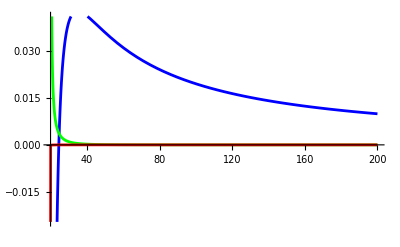

```mathematica
M=1;
b1=10M;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
ℓ=2M l;
L:=2M b1
U:=∞
A[r_]:=(2 r^3+7 M ℓ^2-3 r ℓ^2)/(r^4-r (-2 M+r) ℓ^2)
B[r_]:=ℓ^2/(r^4-r (-2 M+r) ℓ^2)
G[R_]:=-(3 M ℓ(√(R^2-ℓ^2+(2 M ℓ^2)/R)+M ℓ^2 (NIntegrate[1/(r^2 √(r^2-ℓ^2(1-(2M)/r))),{r,L,R}])))/(R^3 (R^3+(2 M-R) ℓ^2))
N[Limit[A[r],r->1.1L]]
N[Limit[B[r],r->1.1L]]
Plot[{A[r],B[r],G[r]},{r,L,10L},PlotStyle->{Blue,Green,Red,Black}]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

(d^2 Z^θ)/dr^2+(1/k^r dk^r/dr+2/r)dZ^θ/dr+(k^ϕ/k^r)^2 Z^θ=F^θ/((k^r)^2) 
(d^2 Z^θ)/dr^2+A dZ^θ/dr+B Z^θ=G
Z^θ=-1/B(d^2 Z^θ)/dr^2-A/B dZ^θ/dr+G/B

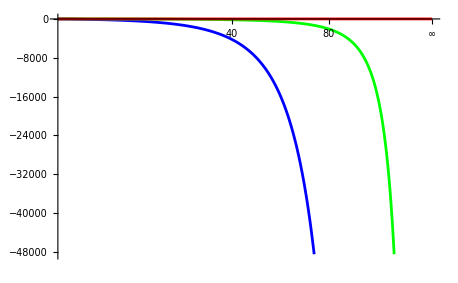

```mathematica
M=1;
b1=10M;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
ℓ=2M l;
L:=2M b1
U:=∞
A[r_]:=(2 r^3+7 M ℓ^2-3 r ℓ^2)/(r^4-r (-2 M+r) ℓ^2)
B[r_]:=ℓ^2/(r^4-r (-2 M+r) ℓ^2)
G[R_]:=-(3 M ℓ(√(R^2-ℓ^2+(2 M ℓ^2)/R)+M ℓ^2 (NIntegrate[1/(r^2 √(r^2-ℓ^2(1-(2M)/r))),{r,L,R}])))/(R^3 (R^3+(2 M-R) ℓ^2))
Plot[{-1/B[r],-A[r]/B[r],G[r]/B[r]},{r,L,U},PlotStyle->{Blue,Green,Red,Black}]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

## Approximate Solution

q'+2/r q=(F -(k^ϕ)^2 Z)/k^r                                  (1)
To analytically solve for Z we make use of the expansion Z∼ Z1 + Z2 where Z1 is the solution of
q1'+2/r q1=F/k^r                                  (2)
(2)can be solved analytecally and Z2 is the remaining part of Z.
Substituting  Z= Z1 + Z2 and q= q1 + q2 in (1)
(q1 + q2)'+2/r(q1 + q2)=(F -(k^ϕ)^2(Z1 + Z2))/k^r                                 (3)
Since (3) is a linear differential equation it can be expanded as
q1'+2/r q1+q2'+2/r q2=(F -(k^ϕ)^2(Z1 + Z2))/k^r                                 (4)
Substituting q1'+2/r q1=F/k^r in (4)
F/k^r+q2'+2/r q2=(F -(k^ϕ)^2(Z1 + Z2))/k^r
⇒ q2'+2/r q2=-((k^ϕ)^2(Z1 + Z2))/k^r                                 (5)
Asuming that Z2<< Z1 (5) can be approximated as
q2'+2/r q2=-((k^ϕ)^2 Z1)/k^r                                (6)
Since Z1 is known from (2),(6)can be solved analytecally

## Solutions for q1 and Z1

### Solution of q1'+2/r q1=F/k^r

From (2)
q1'+2/r q1=F/k^r

#### Homogeneous solution of q1'+2/r q1=0

```mathematica
DSolve[q1'[r]+2/r q1[r]==0,q1[r],r]
```

{{q1[r]→C[1]/r^2}}

#### Full General solution of q1'+2/r q1=F/k^r

Multiplying both sides with the integrating factor ρ = ⅇ^(∫2/r ⅆr) = r^2

r^2 q1'+2r q1=r^2 F/k^r
⇒   (r^2 q1)'=r^2 F/k^r
⇒   q1=1/r^2( C[11]+∫r^2 F/k^r ⅆr)      is the particular solution of the non-homogenous equation.

The full general solution for q1 is
q1=1/r^2( C[1]+C[11]+∫r^2 F/k^r ⅆr)

Absorbing  C[11]  into   C[1],   The full general solution for  q1  is
q1=1/r^2( C[1]+∫r^2 F/k^r ⅆr)
 q1=1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)                                (7)

```mathematica
DSolve[q1'[r]+2/r q1[r]==A[r],q1[r],r]
```

{{q1[r]→C[1]/r^2+(A[K[1]] K[1]^2K[1]1r)/r^2}}

### Z1

q1 = (d(Z1))/ds=k^r(d(Z1))/dr
⇒ Z1 =C[2]+∫q1/k^r ⅆr
=C[2]+∫1/(r^2 k^r)( C[1]+∫(r^2 F)/k^r ⅆr)ⅆr
=C[2]+∫1/(2M z^2 k^r)( C[1]+∫8 M^3(z^2 F)/k^r ⅆz)ⅆz                                (8)

## Solutions for q2 and Z2

### Solution of q2'+2/r q2=-((k^ϕ)^2 Z1)/k^r

From (6)
q2'+2/r q2=-((k^ϕ)^2 Z1)/k^r

#### Homogeneous solution of q2'+2/r q2=0

```mathematica
DSolve[q2'[r]+2/r q2[r]==0,q2[r],r]
```

{{q2[r]→C[1]/r^2}}

q2=C[A]/r^2

#### Full General solution of q2'+2/r q2=-((k^ϕ)^2 Z1)/k^r

Multiplying both sides with the integrating factor ρ = ⅇ^(∫2/r ⅆr) = r^2

r^2 q2'+2 r q2=-r^2((k^ϕ)^2 Z1)/k^r
⇒   (r^2 q2)'=-r^2((k^ϕ)^2 Z1)/k^r
⇒   q2=1/r^2( C[AA]-∫r^2((k^ϕ)^2 Z1)/k^r ⅆr)      is the particular solution of the non-homogenous equation.

The full general solution for q2 is
q2=1/r^2( C[A]+C[AA]-∫r^2((k^ϕ)^2 Z1)/k^r ⅆr)

Absorbing  C[AA]  into   C[A],   The full general solution for  q2  is
q2=1/r^2( C[A]-∫r^2((k^ϕ)^2 Z1)/k^r ⅆr)
 q2=1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 Z1)/k^r ⅆz)                                (9)

```mathematica
DSolve[q2'[r]+2/r q2[r]==-A[r],q2[r],r]
```

{{q2[r]→C[1]/r^2+(-A[K[1]] K[1]^2K[1]1r)/r^2}}

### Z2

q2 = (d(Z2))/ds=k^r(d(Z2))/dr
⇒ Z2 =C[B]+∫q2/k^r ⅆr
C[B]+∫1/(r^2 k^r)( C[A]-∫r^2((k^ϕ)^2 Z1)/k^r ⅆr)ⅆr 
⇒ Z2 = C[B]+∫1/(2M z^2 k^r)( C[A]-∫8 M^3 z^2((k^ϕ)^2 Z1)/k^r ⅆz)ⅆz                               (10)

# Outgoing ray from b1 to z

## a

a_(, r)=-α/k^r=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))  for outgoing rays
a=(l √(-b1^2+z^2))/(2 √2 b1^2 z)

Let A_(out) =a_(, r(out))
A_(out)=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))
⇒a_(out)==∫A_(out)ⅆr  = ∫(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))ⅆr       =∫(M ℓ)/(√2 r √(r(r^3-r ℓ^2+2M ℓ^2)))ⅆr

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
```

## Integration

a=∫l/(2 √2 z √(z (z^3+p z+q)))ⅆz     =∫l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))ⅆz

b3 Approximation

```mathematica
l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))/.{b2->-b1-b3}
```

l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z)))

```mathematica
FullSimplify[Series[l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z))),{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

l/(2 √2 z^2 √(-b1^2+z^2))+(b1 l b3)/(4 √2 z^3 (b1+z) √(-b1^2+z^2))+O[b3]^2

a=∫l/(2 √2 z^2 √(-b1^2+z^2))ⅆz          at the leading order in b3

```mathematica
FullSimplify[Integrate[l/(2 √2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>1,z>1}]
```

(l √(-b1^2+z^2))/(2 √2 b1^2 z)

From the boundary condition    a[b1](outgoing) = 0

```mathematica
aradiation:=(l √(-b1^2+z^2))/(2 √2 b1^2 z)
```

### Boundary Behaviour of ‘a’

z → b1

```mathematica
FullSimplify[Limit[aradiation,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[aradiation,z->∞],Assumptions->{M>0,b1>1,z>1}]
```

l/(2 √2 b1^2)

## b1 = l approximation

```mathematica
(l √(-b1^2+z^2))/(2 √2 b1^2 z)/.{b1->l}
```

(√(-l^2+z^2))/(2 √2 l z)

```mathematica
aaprox:=(√(-l^2+z^2))/(2 √2 l z)
```

### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[aaprox,z->l],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[aaprox,z->∞],Assumptions->{M>0,b1>1,z>1}]
```

1/(2 √2 l)

## Numeric Verification of a

### Setting up Numerics

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
aradiation:=(l √(-b1^2+z^2))/(2 √2 b1^2 z)
```

### a_radiation

```mathematica
b1:=10
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[aradiation,z->U]]
aprox==N[Limit[aaprox,z->U]]
numeric1==Simplify[NIntegrate[Subscript[Az, (out)],{z,L,U}]]
numeric2==Simplify[NIntegrate[Subscript[Ar, (out)]/.{f[r]->1-(2M)/r},{r,(2M )L,(2M) U}]]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==0.0372678

aprox==0.033541

numeric1==0.0380315

numeric2==0.0380315

## Plot of a

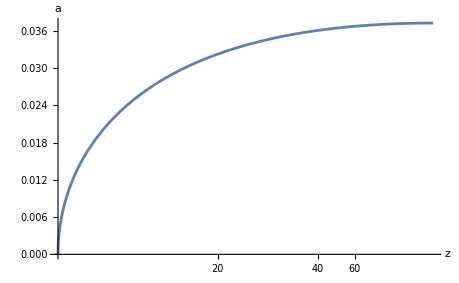

```mathematica
M=1/2;
b1=10;
l=b1^(3/2)/(√(b1-1));
aradiation:=(l √(-b1^2+z^2))/(2 √2 b1^2 z)
Plot[aradiation,{z,b1,∞},AxesLabel->{Style[z,Black],Style[a,Black]}]
Clear[M,b1,b2,b3,l]
```

## F^θ

F^θ=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)

### Setting up

```mathematica
<<GRQUICK.m
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

```mathematica
Metin["Schwar"]
```

Metric Success

```mathematica
Kout={1/f[r],√(1-(ℓ^2 f[r])/r^2),0,ℓ/r^2};
Nout={1/2,-(f[r] √(r^2-ℓ^2 f[r]))/(2 r),0,-(ℓ f[r])/(2 r^2)};
Mout={0,-(ℓ f[r])/(√2 r),ⅈ/(√2 r),(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Mcout={0,-(ℓ f[r])/(√2 r),-ⅈ/(√2 r),(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Ntout=FullSimplify[Nout+A[r] Mout+A[r] Mcout +A[r]^2 Kout];
Mtout=FullSimplify[Mout+A[r] Kout];
Mctout=FullSimplify[Mcout+A[r] Kout];
```

```mathematica
kout[a_]:=Kout[[a+1]]
nout[a_]:=Nout[[a+1]]
mout[a_]:=Mout[[a+1]]
mcout[a_]:=Mcout[[a+1]]
ntout[a_]:=Ntout[[a+1]]
mtout[a_]:=Mtout[[a+1]]
mctout[a_]:=Mctout[[a+1]]
```

## F^θ

```mathematica
FullSimplify[Simplify[
-(ⅈ σ)/ω{(Sum[Riemann[{{0},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{1},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{2},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{3},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}])}/.{θ->Pi/2,f[r]->1-(2M)/r}]/.{A[r]->a},Assumptions->{M>0,r>2M,ℓ>0}]
```

{0,0,(3 M ℓ (√2 a ℓ+√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω),0}

F^θ=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))

```mathematica
FullSimplify[(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))-((3 M ℓ (√2 a ℓ+√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω))/.{f[r]->1-(2M)/r},Assumptions->{M>0,r>2M,ℓ>0}]
```

0

## F^θ=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)

F^θ=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))
Going from r to z
F^θ=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z^3+p z+q)))/z^7)

```mathematica
FullSimplify[(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z^3+p z+q)))/z^7)-((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2)))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)    and 
F^θ=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)
Substituting    a=(l √(-b1^2+z^2))/(2 √2 b1^2 z)
F^θ=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(z(z-b1)(z-b2)(z-b3)))/z^7)

```mathematica
FullSimplify[(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(z(z-b1)(z-b2)(z-b3)))/z^7)-((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/.{a->(l √(-b1^2+z^2))/(2 √2 b1^2 z)}]
```

0

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^7/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z^6-((b1 √(-b1^2+z^2)) b3)/(2 (z^7 (b1+z)))+O[b3]^2

```mathematica
Fradiation:=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)
```

```mathematica
FullSimplify[Fradiation-((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(-b1^2+z^2))/z^6))/.{a->(l √(-b1^2+z^2))/(2 √2 b1^2 z)},Assumptions->{M>0,z>0}]
```

0

#### Boundary Behaviour of F^θ

z → b1

```mathematica
FullSimplify[Limit[Fradiation,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Fradiation,z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

## b1 = l approximation

aaprox:=(√(-l^2+z^2))/(2 √2 l z)
F^θ=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(-b1^2+z^2))/z^6)

```mathematica
(3 l σ)/(16 M^3 ω)(Expand[Simplify[((√2 ((√(-l^2+z^2))/(2 √2 l z)) l)/z^6+(√(-b1^2+z^2))/z^6)/.{b1->l},Assumptions->{l>1,z>l}]])
```

```mathematica
(3 l ((√(-l^2+z^2))/(2 z^7)+(√(-l^2+z^2))/z^6) σ)/(16 M^3 ω)
```

```mathematica
Faprox:=(3 l σ)/(16 M^3 ω)((√(-l^2+z^2))/(2 z^7)+(√(-l^2+z^2))/z^6)
```

### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[Faprox,z->l],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Faprox,z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

## Numeric Verification of F^θ

### Setting up Numerics

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Fradiation:=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)
Faprox:=(3 l σ)/(16 M^3 ω)((√(-l^2+z^2))/(2 z^7)+(√(-l^2+z^2))/z^6)
```

(F^θ)_(out)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))      =(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)

### F_radiation

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[Fradiation,z->U]]
aprox==N[Limit[Faprox,z->U]]
numeric1==N[Limit[(3 l σ)/(16 M^3 ω)((√2(NIntegrate[Subscript[Az, (out)],{z,L,U}]) l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7),z->U]]
numeric2==N[Limit[(3 M ℓ σ)/(r^5 ω)((√2 (NIntegrate[Subscript[Ar, (out)]/.{f[r]->1-(2M)/r},{r,(2M )L,(2M ) U}]) ℓ)/r+√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},r->(2M ) U]]
Clear[b1,b2,b3,l,ℓ,M,U,L]
```

analytic==0.

aprox==0.

numeric1==0.

numeric2==0.

## Plots of F^θ

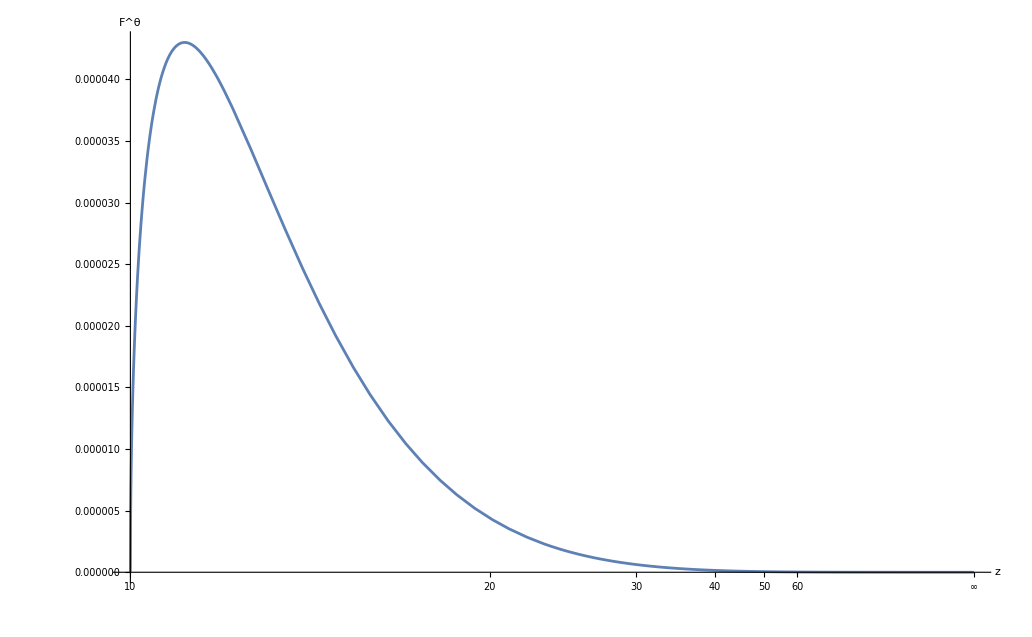

```mathematica
σ=1;
ω=1;
M=1/2;
b1=10;
l=b1^(3/2)/(√(b1-1));
Fradiation:=(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)
Plot[{Fradiation},{z,b1,∞},AxesLabel->{Style[z,Bold,Black],Style[F^θ,Bold,Black]}]
Clear[M,b1,b2,b3,l,σ,ω]
```

## q_0^θ

q^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)
g=(3 l σ)/(4 ω)((3 b1^3+l^2)/(3 b1^5)-1/z^2-l^2/(3 b1^2 z^3))
q^θ=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))

## k_(out)^r=(√(-b1^2+z^2))/z

```mathematica
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
```

k_(out)^r=√(1-(ℓ^2 f[r])/r^2)=√((z^3-l^2 z+l^2)/z^3)

```mathematica
FullSimplify[√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,z>0}]
```

√((l^2-l^2 z+z^3)/z^3)

Substituting   q  for l^2 ,     p  for -l^2
k_(out)^r=(√(z(z^3+p z+q)))/z^2
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)

```mathematica
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
```

Verification

```mathematica
FullSimplify[(√(z(z^3+p z+q)))/z^2-(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^2/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z-((b1 √(-b1^2+z^2)) b3)/(2 (z^2 (b1+z)))+O[b3]^2

```mathematica
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
```

#### Boundary Behaviour of k_(out)^r

z → b1

```mathematica
FullSimplify[Limit[Subscript[kr, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kr, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

1

### b1 = l approximation

```mathematica
Simplify[(√(-b1^2+z^2))/z/.{b1->l},Assumptions->{l>1,z>l}]
```

(√(-l^2+z^2))/z

```mathematica
Subscript[kaprox, (out)]:=(√(-l^2+z^2))/z
```

#### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[Subscript[kaprox, (out)],z->l],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kaprox, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

1

## g_(out)=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))

g_(out)=∫8 M^3(z^2 F^θ)/(k_(out)^r)ⅆz      =∫8 M^3(z^2((3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)))/(k_(out)^r)ⅆz  
Substituting    k_(out)^r=(√(-b1^2+z^2))/z
g_(out)= ∫(3 l σ)/(2 ω)(1/z^3+l^2/(2 b1^2 z^4))ⅆz

```mathematica
FullSimplify[(3 l σ)/(2 ω)(1/z^3+l^2/(2 b1^2 z^4))-(8 M^3(z^2 F^θ)/k^r)/.{k^-r->z/(√(-b1^2+z^2)),F^θ->(3 l σ)/(16 M^3 ω)((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6)},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(2 ω)(Expand[FullSimplify[Integrate[1/z^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[l^2/(2 b1^2 z^4),z],Assumptions->{M>0,b1>0,z>0}]])
```

(3 l (-l^2/(6 b1^2 z^3)-1/(2 z^2)) σ)/(2 ω)

From the boundary condition   g_(out)[b1]=0

```mathematica
gradiation:=(3 l σ)/(4 ω)((3 b1^3+l^2)/(3 b1^5)-1/z^2-l^2/(3 b1^2 z^3))
```

#### Boundary Behaviour of g_(out)

z → b1

```mathematica
FullSimplify[Limit[gradiation,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[gradiation,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l (3 b1^3+l^2) σ)/(4 b1^5 ω)

### b1 = l approximation

g_(out)=∫8 M^3(z^2 F^θ)/(k_(out)^r)ⅆz      =∫8 M^3(z^2((3 l σ)/(16 M^3 ω)((√(-l^2+z^2))/(2 z^7)+(√(-l^2+z^2))/z^6)))/((√(-l^2+z^2))/z)ⅆz 
g_(out)=∫(3 l σ)/(2 ω)(1/z^3+1/(2 z^4))ⅆz

```mathematica
(3 l σ)/(2 ω)(FullSimplify[Integrate[1/z^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[1/(2 z^4),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l (-1/(6 z^3)-1/(2 z^2)) σ)/(2 ω)

```mathematica
Subscript[gaprox, (out)]:=(3 l σ)/(2 ω)((1+3 l)/(6 l^3)-1/(2 z^2)-1/(6 z^3))
```

#### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[Subscript[gaprox, (out)],z->l],Assumptions->{l>1}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[gaprox, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

(σ+3 l σ)/(4 l^2 ω)

## q_(out)^θ=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))

q_(out)^θ   =   (g_(out))/(4 M^2 z^2)

```mathematica
qradiation:=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))
```

```mathematica
FullSimplify[ qradiation-(g/(4 M^2 z^2))/.{g->(3 l σ)/(4 ω)((3 b1^3+l^2)/(3 b1^5)-1/z^2-l^2/(3 b1^2 z^3))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[ qradiation,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[ qradiation,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

### b1 = l approximation

q_(out)^θ   =   (g_(out))/(4 M^2 z^2)

```mathematica
Subscript[qaprox, (out)]:=(3 l σ)/(8 M^2 ω)((1+3 l)/(6 l^3 z^2)-1/(2 z^4)-1/(6 z^5))
```

#### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[Subscript[qaprox, (out)],z->l],Assumptions->{l>1}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[qaprox, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

## Verification of k^r

### Setting up Numerics

```mathematica
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
Subscript[kaprox, (out)]:=(√(-l^2+z^2))/z
```

### (k^r)_(out)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[Subscript[kr, (out)],z->U]]
aprox==N[Limit[Subscript[kaprox, (out)],z->U]]
numericz==N[Limit[Subscript[krz, (out)],z->U]]
numericr==N[Limit[Subscript[krr, (out)]/.{f[r]->1-(2M)/r},r->(2M ) U]]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==1.

aprox==1.

numericz==1.

numericr==1.

## Numeric Verification of g

### Setting up Numerics

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gz_(out)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(out))      =8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/((√(z(z-b1)(z-b2)(z-b3)))/z^2)       =(3 l σ)/(2 z^3 ω)(1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z))))
Gr_(out)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2)))/(krr_(out))      =(3 M ℓ σ)/(r^3 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))/(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}      =(3 M ℓ σ)/(r^3 ω)(1+(√2 a ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r)))

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
gradiation:=(3 l σ)/(4 ω)((3 b1^3+l^2)/(3 b1^5)-1/z^2-l^2/(3 b1^2 z^3))
Subscript[gaprox, (out)]:=(3 l σ)/(2 ω)((1+3 l)/(6 l^3)-1/(2 z^2)-1/(6 z^3))
```

### g_radiation

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[gradiation,z->U]]
aprox==N[Limit[Subscript[gaprox, (out)],z->U]]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numeric1==NIntegrate[(3 l σ)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,U}]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numeric2==NIntegrate[(3 M ℓ σ)/(r^3 ω)(1+(√2 (intArout[r]) ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r))),{r,(2M ) L,(2M ) U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U,intAzout,intArout]
```

analytic==0.081985

aprox==0.0734012

numeric1==0.0821173

numeric2==0.0821173

## Numeric Verification of q^θ

### Setting up Numerics

q^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gz_(out)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(out))      =8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/((√(z(z-b1)(z-b2)(z-b3)))/z^2)       =(3 l σ)/(2 z^3 ω)(1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z))))
Gr_(out)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2)))/(krr_(out))      =(3 M ℓ σ)/(r^3 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))/(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}      =(3 M ℓ σ)/(r^3 ω)(1+(√2 a ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r)))

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
qradiation:=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))
Subscript[qaprox, (out)]:=(3 l σ)/(8 M^2 ω)((1+3 l)/(6 l^3 z^2)-1/(2 z^4)-1/(6 z^5))
```

### q_radiation

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[qradiation,z->U]]
aprox==N[Limit[Subscript[qaprox, (out)],z->U]]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numeric1==Limit[1/(4 M^2 z^2)(NIntegrate[(3 l σ)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,U}]),z->U]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numeric2==Limit[1/r^2(NIntegrate[(3 M ℓ σ)/(r^3 ω)(1+(√2 (intArout[r]) ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r))),{r,(2M ) L,(2M ) U}]),r->(2M ) U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U,intAzout,intArout]
```

analytic==0.

aprox==0.

numeric1==0.

numeric2==0.

## Plot of q^θ

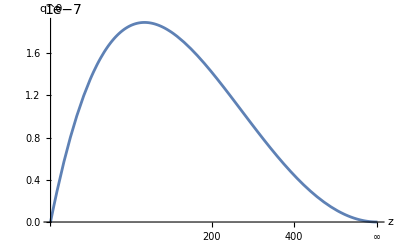

```mathematica
σ=1;
ω=1;
M:=1/2
b1=100;
l=b1^(3/2)/(√(b1-1));
qradiation:=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))
Plot[{qradiation,Subscript[qaprox, (out)]},{z,b1,∞},AxesLabel->{Style[z,Bold,Black],Style[q^θ,Bold,Black]}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ_0

θ=  C[2]+∫q^θ/k^r ⅆr       =  C[2]+∫(2 M q^θ)/k^r ⅆz
θ=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))

## θ_(out)=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))

θ_(out) = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz
= C[2]+∫(3 l σ)/(8 M ω)((3 b1^3+l^2)/(3 b1^5 z √(-b1^2+z^2))-1/(z^3 √(-b1^2+z^2))-l^2/(3 b1^2 z^4 √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l σ)/(8 M ω)((3 b1^3+l^2)/(3 b1^5 z √(-b1^2+z^2))-l^2/(3 b1^2 z^4 √(-b1^2+z^2))-1/(z^3 √(-b1^2+z^2)))-((2 M q^θ)/k^r)/.{k^-r->z/(√(-b1^2+z^2)),q^θ->(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(8 M ω)(FullSimplify[Integrate[(3 b1^3+l^2)/(3 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(3 b1^2 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ (-(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(9 b1^6 z^3)+((3 b1^3+l^2) ArcCot[b1/(√(-b1^2+z^2))])/(3 b1^6)-((b1 √(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^3)))/(8 M ω)

θ_(out) =(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))

From the boundary condition  θ_(out)[b1] = 0

```mathematica
θradiation :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))
```

#### Linear aprox

```mathematica
FullSimplify[Series[θradiation,{z,∞,1},Assumptions->{M>0,b1>0,z>0}]]
```

(l (9 b1^3 π+l^2 (-8+6 π)) σ)/(96 b1^6 M ω)-(l (3 b1^3+l^2) σ)/(8 (b1^5 M ω) z)+O[1/z]^2

```mathematica
θlinearradiation :=(3 l σ)/(24 M ω)((9 b1^3 π+l^2 (-8+6 π))/(12 b1^6)-(3 b1^3+l^2)/(b1^5 z))
```

#### Boundary Behaviour of θ_(in)

z → b1

```mathematica
FullSimplify[Limit[θradiation,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[θradiation,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l (9 b1^3 π+l^2 (-8+6 π)) σ)/(96 b1^6 M ω)

### b1 = l approximation

θ_(out) = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz
= C[2]+∫(3 l σ)/(8 M ω)((1+3 l)/(3 l^3 z √(-l^2+z^2))-1/(z^3 √(-l^2+z^2))-1/(3 z^4 √(-l^2+z^2)))ⅆz

```mathematica
FullSimplify[((3 l σ)/(8 M ω)((1+3 l)/(3 l^3 z √(-l^2+z^2))-1/(z^3 √(-l^2+z^2))-1/(3 z^4 √(-l^2+z^2))))-((2 M q^θ)/k^r)/.{k^-r->z/(√(-l^2+z^2)),q^θ->(3 l σ)/(8 M^2 ω)((1+3 l)/(6 l^3 z^2)-1/(2 z^4)-1/(6 z^5))},Assumptions->{M>0,l>1,z>l}]
```

0

```mathematica
(3 l σ)/(8 M ω)(FullSimplify[Integrate[(1+3 l)/(3 l^3 z √(-l^2+z^2)),z],Assumptions->{M>0,l>1,z>l}]+FullSimplify[Integrate[-1/(z^3 √(-l^2+z^2)),z],Assumptions->{M>0,l>1,z>l}]+FullSimplify[Integrate[-1/(3 z^4 √(-l^2+z^2)),z],Assumptions->{M>0,l>1,z>l}])
```

(3 l σ (-(√(-l^2+z^2) (l^2+2 z^2))/(9 l^4 z^3)+((1+3 l) ArcCot[l/(√(-l^2+z^2))])/(3 l^4)-((l √(-l^2+z^2))/z^2+ArcCot[l/(√(-l^2+z^2))])/(2 l^3)))/(8 M ω)

For z>>l

```mathematica
Simplify[Series[ArcCot[l/(√(-l^2+z^2))],{z,Infinity,1}],Assumptions->{M>0,l>1,z>l}]
```

π/2-l/z+O[1/z]^2

```mathematica
Expand[Simplify[-(l^2+2 z^2)/(9 l^4 z^2)+((1+3 l) (π/2-l/z))/(3 l^4)-(l/z+(π/2-l/z))/(2 l^3)]]
```

-2/(9 l^4)+π/(6 l^4)+π/(4 l^3)-1/(9 l^2 z^2)-1/(3 l^3 z)-1/(l^2 z)

```mathematica
Simplify[(-8+(6+9 l) π)/(36 l^4)-((2+3 l) (-4+π))/(12 l^4)]
```

(4+9 l)/(9 l^4)

```mathematica
Subscript[θaprox, (out)]:=(3 l σ)/(8 M ω)((4+9 l)/(9 l^4)-(1+3 l)/(3 l^3 z)-1/(9 l^2 z^2))
```

#### Boundary Behaviour

z → b1

```mathematica
FullSimplify[Limit[Subscript[θaprox, (out)],z->l],Assumptions->{l>1}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θaprox, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

((4+9 l) σ)/(24 l^3 M ω)

## Numeric Verification of θ

### Setting up Numerics

q^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

q^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gz_(out)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(out))      =8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7))/((√(z(z-b1)(z-b2)(z-b3)))/z^2)       =(3 l σ)/(2 z^3 ω)(1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z))))
Gr_(out)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2)))/(krr_(out))      =(3 M ℓ σ)/(r^3 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))/(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}      =(3 M ℓ σ)/(r^3 ω)(1+(√2 a ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r)))
θ_(r(out))=  C[2]+∫(q_(in)^θ)/(k_(in)^r)ⅆr
θ_(z(out))  = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
θradiation :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
Subscript[θaprox, (out)]:=(3 l σ)/(8 M ω)((4+9 l)/(9 l^4)-(1+3 l)/(3 l^3 z)-1/(9 l^2 z^2))
θlinearradiation :=(3 l σ)/(24 M ω)((9 b1^3 π+l^2 (-8+6 π))/(12 b1^6)-(3 b1^3+l^2)/(b1^5 z))
```

### θ_radiation

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[θradiation,z->U]]
aprox==N[Limit[Subscript[θaprox, (out)],z->U]]
linearaprox==N[Limit[θlinearradiation,z->U]]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numericgzout[Z_?NumericQ]:=numericgzout[Z]=NIntegrate[(3 l σ)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,Z}]
numericz ==Limit[NIntegrate[numericgzout[z]/(2 M  z^2 Subscript[krz, (out)]),{z,L,U}],z->U]

intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numericgrout[R_?NumericQ]:=numericgrout[R]=NIntegrate[(3 M ℓ σ)/(r^3 ω)(1+(√2 (intArout[r]) ℓ)/(√(r^2-ℓ^2+(2 M ℓ^2)/r))),{r,(2M ) L,R}]
numericr ==Limit[NIntegrate[numericgrout[r]/(r^2 Subscript[krr, (out)]),{r,(2M ) L,(2M ) U}],r->(2M )U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intAzout,numericgzout,intArout,numericgrout]
```

analytic==0.0288702

aprox==0.0259081

linearaprox==0.0288702

numericz==0.0297511

numericr==0.0297511

## Plot of θ

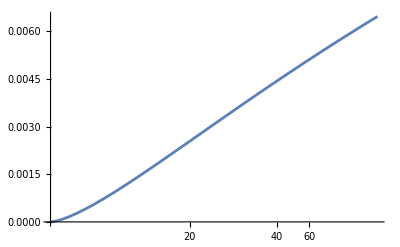

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
θradiation :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
Plot[{θradiation,Subscript[θaprox, (out)],θlinearradiation},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

### Plot of θLinear_(out)

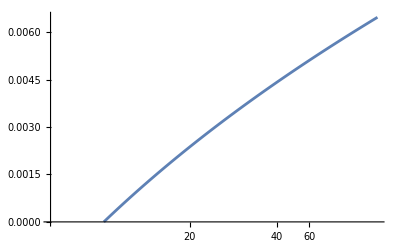

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[θlinearradiation,{z,b1,∞},PlotRange->{0,0.0065}]
Clear[b1,b2,b3,l,M,σ,ω]
```

### Comparison of θLinear_(out) and θ_(out)

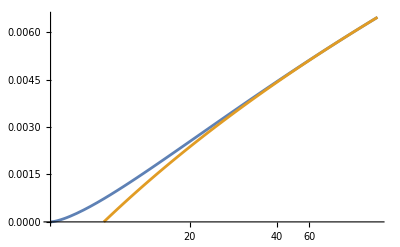

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[{θradiation,θlinearradiation},{z,b1,∞},PlotRange->{0,0.0065}]
Clear[b1,b2,b3,l,M,σ,ω]
```

θLinear_(out)    approaches    θ_(out)   for z as small as 3 b1

## q_1^θ

q1^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ_0)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]-h)
θ_0_(out) :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
kr_(out):=(√(-b1^2+z^2))/z 
k^ϕ=ℓ/r^2=(2M l)/(4 M^2 z^2)

### h_(out)

h_(out)=∫8 M^3(z^2(k^ϕ)^2 θ_0_(out))/(k_(out)^r)ⅆz
h_(out)=∫8 M^3(z^2((2M l)/(4 M^2 z^2))^2((3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) ))/((√(-b1^2+z^2))/z)ⅆz

h_(out)=∫(3 l^3 σ)/(4 ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^4 √(-b1^2+z^2))+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6 z √(-b1^2+z^2))) ⅆz

```mathematica
FullSimplify[(3 l^3 σ)/(4 ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^4 √(-b1^2+z^2))+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6 z √(-b1^2+z^2))) -(8 M^3(z^2(k^ϕ)^2 Subscript[Subscript[θ, 0], (out)])/Subscript[k, (out)]^r)/.{Subscript[k, (out)]^-r->z/(√(-b1^2+z^2)),k^ϕ->ℓ/r^2,k^(2ϕ)->ℓ^2/r^4,Subscript[Subscript[θ, 0], (out)]->(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))  }/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^3 σ)/(4 ω)(FullSimplify[Integrate[-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l^3 σ ((4 b1^2 l^2+27 b1^4 z+24 l^2 z^2)/(108 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7)))/(4 ω)

```mathematica
FullSimplify[(3 l^3 σ)/(4 ω) ((2 l^2)/(9 b1^6 z)+1/(4 b1^2 z^2)+l^2/(27 b1^4 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7))-((3 l^3 σ ((4 b1^2 l^2+27 b1^4 z+24 l^2 z^2)/(108 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7)))/(4 ω)),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   h_(out)[b1]=0

```mathematica
Subscript[h, (out)]:=(3 l^3 σ)/(4 ω) (-(27 b1^3+28 l^2)/(108 b1^7)+(2 l^2)/(9 b1^6 z)+1/(4 b1^2 z^2)+l^2/(27 b1^4 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7))
```

#### Boundary Behaviour of h_(out)

z → b1

```mathematica
Subscript[hatb1, (out)]=FullSimplify[Limit[ Subscript[h, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[h, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

((27 b1^3 l^3 (-4+π^2)+2 l^5 (-56+9 π^2)) σ)/(576 b1^7 ω)

### q_1_(out)^θ

q1_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]-h_(out)) =   -(h_(out))/(4 M^2 z^2)    ,since  h_(out)[b1] = 0 
q1_(out)^θ= -(h_(out))/(4 M^2 z^2)
= -((3 l^3 σ)/(4 ω) (-(27 b1^3+28 l^2)/(108 b1^7)+(2 l^2)/(9 b1^6 z)+1/(4 b1^2 z^2)+l^2/(27 b1^4 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7)))/(4 M^2 z^2)

```mathematica
Subscript[Subscript[q, 1], (out)]:=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
```

```mathematica
FullSimplify[Subscript[Subscript[q, 1], (out)]-(-Subscript[h, (out)]/(4 M^2 z^2))/.{Subscript[h, (out)]->(3 l^3 σ)/(4 ω) (-(27 b1^3+28 l^2)/(108 b1^7)+(2 l^2)/(9 b1^6 z)+1/(4 b1^2 z^2)+l^2/(27 b1^4 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q1atb1, (out)]=FullSimplify[Limit[Subscript[Subscript[q, 1], (out)],z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[Subscript[q, 1], (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of h

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ_0)/(k_(in)^r)
⇒h=∫Hⅆz 
H_(out)=8 M^3(z^2((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)))/(krz_(out))=(3 l (1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ, 0] :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
Subscript[h, (out)]:=(3 l^3 σ)/(4 ω) (-(27 b1^3+28 l^2)/(108 b1^7)+(2 l^2)/(9 b1^6 z)+1/(4 b1^2 z^2)+l^2/(27 b1^4 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7))
```

### h_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=100
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[Subscript[h, (out)],z->U]]
Numeric==NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ, 0])/Subscript[krz, (out)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==0.00280486

Numeric==0.0028063

## Verification of q1^θ

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ_0)/k^r
⇒h=∫Hⅆz 
H=8 M^3(z^2(kϕz)^2 θ_0)/krz
q1^θ    =-1/(4 M^2 z^2)(∫8 M^3(z^2(k^ϕ)^2 θ_0)/k^r ⅆz)   =-1/(4 M^2 z^2)( ∫8 M^3(z^2(kϕz)^2 θ_0)/krz ⅆz)

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ, 0] :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
Subscript[Subscript[q, 1], (out)]:=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
```

### q_1_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=100
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[Subscript[Subscript[q, 1], (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ, 0])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==0.

Numeric==0.

## Plots of q2^θ

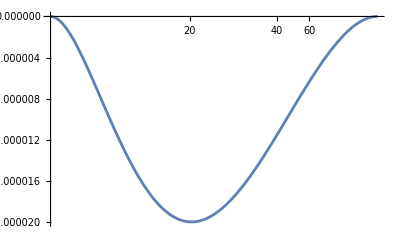

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[Subscript[q, 1], (out)]:=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
Plot[Subscript[Subscript[q, 1], (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ_1

θ1=  C[B]+∫q1/k^r ⅆr      =  C[B]+∫(2 M q1^θ)/k^r ⅆz
q_1_(out):=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
kr_(out):=(√(-b1^2+z^2))/z

## θ1_(out)

θ1_(out) = C[B]+∫(2 M q1_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫(2 M ((3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))))/((√(-b1^2+z^2))/z)ⅆz

θ1_(out) = C[B]+∫(3 l^3 σ)/(8 M ω) ((27 b1^3+28 l^2)/(108 b1^7 z √(-b1^2+z^2))-(2 l^2)/(9 b1^6 z^2 √(-b1^2+z^2))-1/(4 b1^2 z^3 √(-b1^2+z^2))-l^2/(27 b1^4 z^4 √(-b1^2+z^2))-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l^3 σ)/(8 M ω) ((27 b1^3+28 l^2)/(108 b1^7 z √(-b1^2+z^2))-(2 l^2)/(9 b1^6 z^2 √(-b1^2+z^2))-1/(4 b1^2 z^3 √(-b1^2+z^2))-l^2/(27 b1^4 z^4 √(-b1^2+z^2))-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z √(-b1^2+z^2)))-((2 M Subscript[Subscript[q, 1], (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[Subscript[q, 1], (out)]->(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l^3 σ)/(8 M ω) (FullSimplify[Integrate[(27 b1^3+28 l^2)/(108 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(9 b1^6 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(4 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(27 b1^4 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l^3 σ (-(2 l^2 √(-b1^2+z^2))/(9 b1^8 z)-(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^8 z^3)+((27 b1^3+28 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(108 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8)-((b1 √(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))])/(8 b1^5)))/(8 M ω)

From the boundary condition  θ1_(out)[b1] = 0

```mathematica
Subscript[θ1, (out)] :=(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
```

```mathematica
FullSimplify[(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))-((3 l^3 σ (-(2 l^2 √(-b1^2+z^2))/(9 b1^8 z)-(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^8 z^3)+((27 b1^3+28 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(108 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8)-((b1 √(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))])/(8 b1^5)))/(8 M ω)),Assumptions->{M>0,z>0}]
```

0

#### Boundary Behaviour of θ1_(out)

z → b1

```mathematica
Subscript[θ1atb1, (out)]=FullSimplify[Limit[Subscript[θ1, (out)] ,z->b1],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ1, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

-((27 b1^3 l^3 π (-6+π^2)+2 l^5 (320-168 π+9 π^3)) σ)/(6912 b1^8 M ω)

## Verification of θ1

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ0_(out))/(k_(out)^r)
⇒h=∫Hⅆz 
H_(out)=8 M^3(z^2(kϕz)^2 θ0_(out))/(krz_(out))
q1_(out)^θ    =-1/(4 M^2 z^2)(∫8 M^3(z^2(k^ϕ)^2 θ0_(out))/(k_(out)^r)ⅆz)   =-1/(4 M^2 z^2)( ∫8 M^3(z^2(kϕz)^2 θ0_(out))/(krz_(out))ⅆz)
θ1_(out) =∫(2 M q1_(out)^θ)/(k_(out)^r)ⅆz

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ0, (out)] :=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6)) 
Subscript[θ1, (out)] :=(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
```

### θ1_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=100
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ1, (out)],z->U]]
intHzout[Z_?NumericQ]:=intHzout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ0, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[NIntegrate[(2 M (intHzout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intHzout]
```

analytic==-4.842×10^-6

Numeric==-4.84837×10^-6-1.20722×10^-22 ⅈ

## Plots of θ1

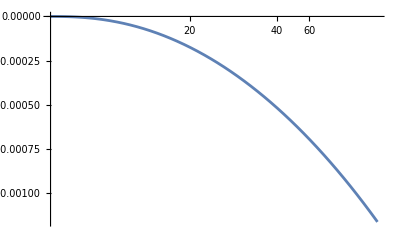

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[θ1, (out)] :=(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
Plot[Subscript[θ1, (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

### Plot of θ1Linear_(out)

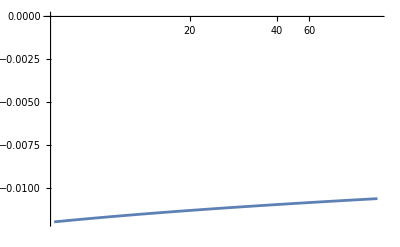

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[Subscript[θ1Linear, (out)],{z,b1,∞},PlotRange->{-0.012,0}]
Clear[b1,b2,b3,l,M,σ,ω]
```

### Comparison of θ1Linear_(out) and θ1_(out)

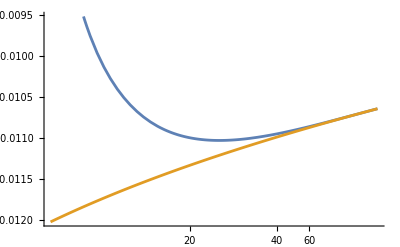

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[{Subscript[θ1, (out)],Subscript[θ1Linear, (out)]},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

θLinear_(out)    approaches    θ_(out)   for z as small as 4 b1

## q^θ=q_0^θ+q_1^θ

```mathematica
Clear[M,σ,ω,b1,l,U,z]
Subscript[q, 0]:=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))
Subscript[q, 1]:=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
q:=(3 l σ)/(16 M^2 ω)((108 b1^5+36 b1^2 l^2+27 b1^3 l^2+28 l^4)/(108 b1^7 z^2)-(2 l^4)/(9 b1^6 z^3)-(4 b1^2+l^2)/(4 b1^2 z^4)-(9 b1^2 l^2+l^4)/(27 b1^4 z^5)-((3 l^2 b1^3+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
```

```mathematica
FullSimplify[q-(Subscript[q, 0]+Subscript[q, 1])]
```

0

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=10000
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[q,z->b1]]
Clear[M,σ,ω,b1,l,U]
```

0.

### Boundary Behaviour of and q

z → b1

```mathematica
σ=1;
ω=1;
M:=1
b1=154;
l=b1^(3/2)/(√(b1-1));
qatb1=N[Limit[q ,z->b1]]
Clear[b1,l,M,σ,ω]
```

0.

z → ∞

```mathematica
σ=1;
ω=1;
M:=1
b1=154;
l=b1^(3/2)/(√(b1-1));
N[Limit[q ,z->∞]]
Clear[b1,l,M,σ,ω]
```

0.

## Plots of q

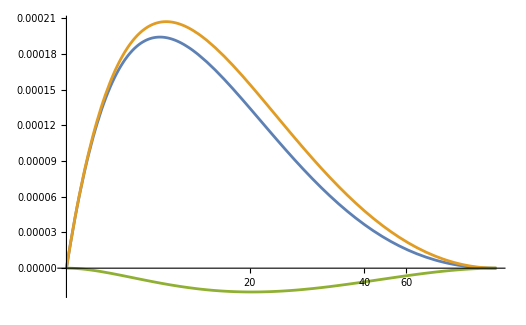

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[q, 0]:=(3 l σ)/(16 M^2 ω)((3 b1^3+l^2)/(3 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5))
Subscript[q, 1]:=(3 l^3 σ)/(16 M^2 ω) ((27 b1^3+28 l^2)/(108 b1^7 z^2)-(2 l^2)/(9 b1^6 z^3)-1/(4 b1^2 z^4)-l^2/(27 b1^4 z^5)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
q:=(3 l σ)/(16 M^2 ω)((108 b1^5+36 b1^2 l^2+27 b1^3 l^2+28 l^4)/(108 b1^7 z^2)-(2 l^4)/(9 b1^6 z^3)-(4 b1^2+l^2)/(4 b1^2 z^4)-(9 b1^2 l^2+l^4)/(27 b1^4 z^5)-((3 l^2 b1^3+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
Plot[{q,Subscript[q, 0],Subscript[q, 1]},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

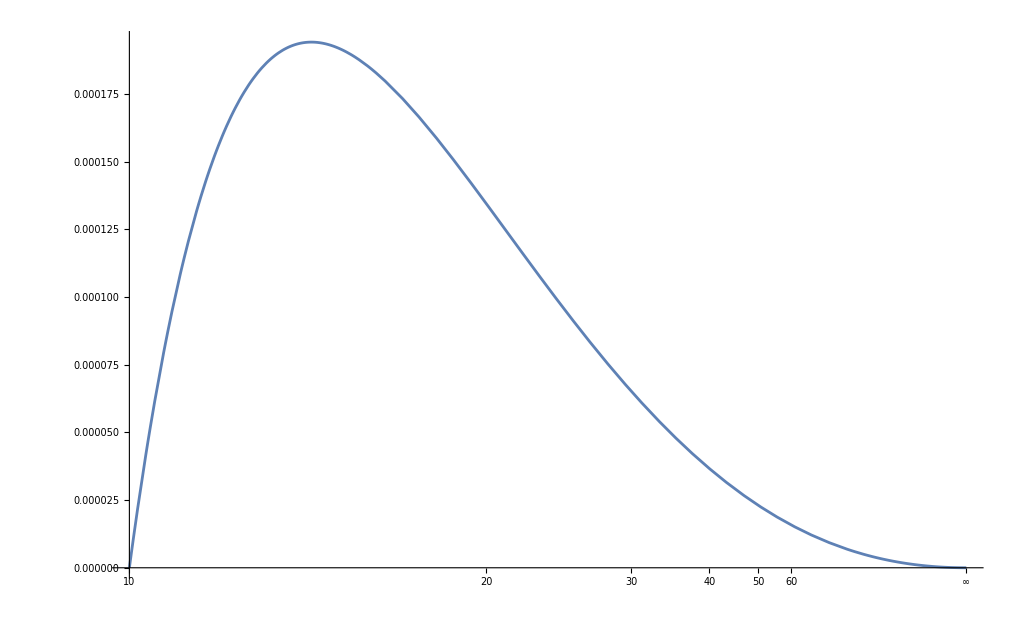

```mathematica
σ=1;
ω=1;
M:=1/2
b1:=10
l=b1^(3/2)/(√(b1-1));
q:=(3 l σ)/(16 M^2 ω)((108 b1^5+36 b1^2 l^2+27 b1^3 l^2+28 l^4)/(108 b1^7 z^2)-(2 l^4)/(9 b1^6 z^3)-(4 b1^2+l^2)/(4 b1^2 z^4)-(9 b1^2 l^2+l^4)/(27 b1^4 z^5)-((3 l^2 b1^3+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^2)/(12 b1^7 z^2))
Plot[q,{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ=θ_0+θ_1

```mathematica
Clear[M,σ,ω,b1,l,U,z]
Subscript[θ0, (out)]:=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))
Subscript[θ1, (out)] :=(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))

Subscript[θ, (out)]:=(3 l σ)/(8 M ω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
```

```mathematica
FullSimplify[Subscript[θ, (out)]-(Subscript[θ0, (out)]+Subscript[θ1, (out)])]
```

0

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ0, (out)],z->U]]
N[Limit[Subscript[θ0, (out)]+Subscript[θ1, (out)],z->U]]
Clear[M,σ,ω,b1,l,U]
```

0.000239875

0.00020037

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ0, (out)],z->U]]
N[Limit[Subscript[θ1, (out)],z->U]]
Clear[M,σ,ω,b1,l,U]
```

0.000239875

-0.0000395057

### Boundary Behaviour of θ_(out)

z → b1

```mathematica
θatb1=FullSimplify[Limit[Subscript[θ, (out)] ,z->b1],Assumptions->{M>0,b1>3M,z>b1}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ, (out)] ,z->∞],Assumptions->{M>0,b1>3M,z>b1}]
```

(l (648 b1^5 π+144 b1^2 l^2 (-4+3 π)-27 b1^3 l^2 π (-6+π^2)-2 l^4 (320-168 π+9 π^3)) σ)/(6912 b1^8 M ω)

```mathematica
FullSimplify[Series[(l (648 b1^5 π+144 b1^2 l^2 (-4+3 π)-27 b1^3 l^2 π (-6+π^2)-2 l^4 (320-168 π+9 π^3)) σ)/(6912 b1^8 M ω)/.{b1->l},{l,Infinity,100}],Assumptions->{M>0,b1>3M}]
```

-(π (-30+π^2) σ)/(256 (M ω) l^2)-((608-384 π+9 π^3) σ)/(3456 (M ω) l^3)+O[1/l]^101

as z->∞  θ_(out) aproaches
θ_(out)[∞]≈-(π (-30+π^2) σ)/(256 l^2 M ω)     =𝔸_(1)σ/(l^2 M ω),  where  𝔸_(1)=(π (30-π^2))/256 ≈0.247037

```mathematica
N[((π (30-π^2))/256)]
```

0.247037

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=1000
l:=b1^(3/2)/(√(b1-1))
N[(l (648 b1^5 π+144 b1^2 l^2 (-4+3 π)-27 b1^3 l^2 π (-6+π^2)-2 l^4 (320-168 π+9 π^3)) σ)/(6912 b1^8 M ω)]
N[(247 σ)/(l^2 M ω)×10^-3]
Clear[M,σ,ω,b1,l]
```

4.94411×10^-7

4.93506×10^-7

## Comparison with ϕ -Deflection

### Geometric Optic’s Deflection ϕ

k^ϕ=ℓ/r^2=(2M l)/(4 M^2 z^2)
kr_(out):=(√(-b1^2+z^2))/z 
ϕ= C +∫k^ϕ/k^r ⅆr       =  C+∫(2 M k^ϕ)/k^r ⅆz
ϕ=  C+∫(2 M ((2M l)/(4 M^2 z^2)))/((√(-b1^2+z^2))/z)ⅆz

ϕ=  C+∫l/(z √(-b1^2+z^2))ⅆz

```mathematica
FullSimplify[(l/(z √(-b1^2+z^2)))-((2 M kϕ)/k^r)/.{k^-r->z/(√(-b1^2+z^2)),kϕ->(2M l)/(4 M^2 z^2)},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
FullSimplify[Integrate[l/(z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]
```

(l ArcCot[b1/(√(-b1^2+z^2))])/b1

From the boundary condition  ϕ_(out) = 0

```mathematica
kϕ:=(2M l)/(4 M^2 z^2)
Subscript[ϕ, (out)] :=(l ArcCot[b1/(√(-b1^2+z^2))])/b1
```

#### Boundary Behaviour of k^ϕ

z → b1

```mathematica
θatb1=FullSimplify[Limit[kϕ ,z->b1],Assumptions->{M>0,b1>3M,z>b1}]
```

l/(2 b1^2 M)

z → ∞

```mathematica
FullSimplify[Limit[kϕ ,z->∞],Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Boundary Behaviour of ϕ

z → b1

```mathematica
θatb1=FullSimplify[Limit[Subscript[ϕ, (out)],z->b1],Assumptions->{M>0,b1>3M,z>b1}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[ϕ, (out)],z->∞],Assumptions->{M>0,b1>3M,z>b1}]
```

(l π)/(2 b1)

Deviation in ϕ is
(l π)/(2 b1)-π/2

```mathematica
FullSimplify[Series[(l π)/(2 b1)-π/2/.{b1->l-1/2},{l,Infinity,2}],Assumptions->{M>0,b1>3M}]
```

π/(4 l)+π/(8 l^2)+O[1/l]^3

### Comparison with θ -Deflection

θ_(out)[∞]≈(π (30-π^2) σ)/(256 l^2 M ω)     =𝔸_(1)σ/(l^2 M ω),  where  𝔸_(1)=(π (30-π^2))/256 ≈0.247037
ϕ_(out)[∞]≈π/(4 l)+π/(8 l^2)

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1/10
l:=(3 √3)/(2M)
N[σ/(l^2 M ω)((π (30-π^2))/256)]
N[π/(4 l)+π/(8 l^2)]
Clear[M,σ,ω,l]
```

0.18299

0.165694

For sufficiently small   M , l ,  ω   the deviations of   θ  and   ϕ   at   ∞  can be of the same magnitude
For example when  M=1/2,  l=3 √3,  ω=1/10

## Plots of θ_(out)

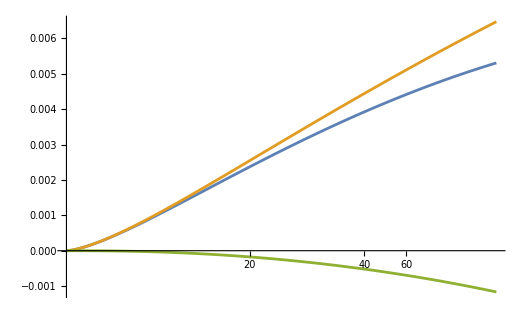

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[θ0, (out)]:=(3 l σ)/(8 M ω)(-(√(-b1^2+z^2) (2 b1^2 l^2+9 b1^4 z+4 l^2 z^2))/(18 b1^6 z^3)+((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(6 b1^6))
Subscript[θ1, (out)] :=(3 l^3 σ)/(8 M ω)(-(20 l^2 √(-b1^2+z^2))/(81 b1^8 z)-(√(-b1^2+z^2))/(8 b1^4 z^2)-(l^2 √(-b1^2+z^2))/(81 b1^6 z^3)+((27 b1^3+56 l^2) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3+2 l^2) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))

Subscript[θ, (out)]:=(3 l σ)/(8 M ω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
Plot[{Subscript[θ, (out)],Subscript[θ0, (out)],Subscript[θ1, (out)]},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

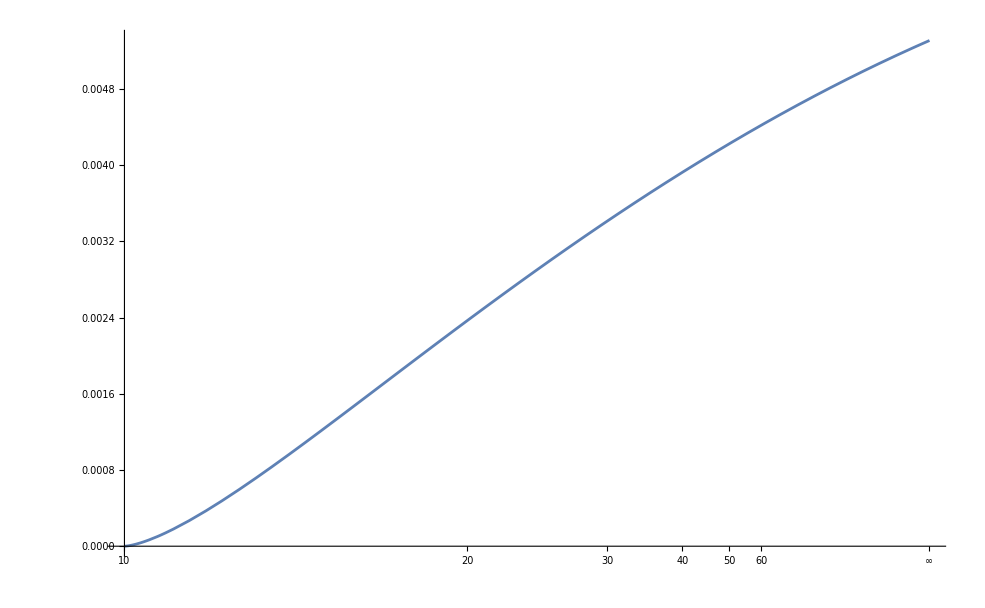

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[θ, (out)]:=(3 l σ)/(8 M ω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))
Plot[{Subscript[θ, (out)]},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## Deviations

c=299792458 m s^-1
G=6.6743×10^-11 m^3 kg^-1 s^-2
Light year =9.46×10^15 m

M from kg to  m   (M → G c^-2 M)
ω from s^-1 to  m^-1   (ω → c^-1 ω )

#### Angular Frequency ω

Frequency of visible light  ωred  =2π×400 THz       =8π×10^14 s^-1    ⇒in Geometrized units      Redω  = 8.38338×10^6 m^-1

Frequency of radio waves  ωradio  =2π×10 MHz   =2π×10^6 s^-1   ⇒in Geometrized units       Radioω  = 0.0209585 m^-1

```mathematica
c=299792458 m s^-1;
ωred= 8π×10^14 s^-1;
ωradio= 2π×10^6 s^-1;
Redω==N[c^-1 ωred]
Radioω==N[c^-1 ωradio]
Clear[c,ωred,ωradio]
```

Redω==(8.38338×10^6)/m

Radioω==0.0209585/m

## Sun

Mass of the sun   M=1.988×10^30 kg   in Geometrized units       M = 1476.32 m
Distance to Earth          z_(S-E) = 149597870700m     =5.06425×10^7 r_g
b1 =235515

```mathematica
M = 1476.32 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.020958450219516818 m^-1;
b1=235515;
l=b1^(3/2)/(√(b1-1));
z=5.0642474847664185*^7;
Subscript[θ, visible]==N[(3 l σ)/(8 M Redω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Subscript[θ, Radio]==N[(3 l σ)/(8 M Radioω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==3.58241×10^-22 σ

θ_Radio==1.43296×10^-13 σ

## Proxima Centauri

Mass of Proxima Centauri   M=2.42735×10^29 kg   in Geometrized units       M = 180.35 m
Distance to Earth          z_(PC-E) = 4.017499×10^16 m           =1.11381×10^14
b1= 297422

```mathematica
M = 180.35 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.020958450219516818 m^-1;
b1=297422;
l=b1^(3/2)/(√(b1-1));
z=1.1138062101469366*^14;
Subscript[θ, visible]==N[(3 l σ)/(8 M Redω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Subscript[θ, Radio]==N[(3 l σ)/(8 M Radioω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==1.84706×10^-21 σ

θ_Radio==7.38825×10^-13 σ

## RX J1856.5-3754

Mass of RX J1856.5-3754   M=1.7892×10^30 kg   in Geometrized units       M = 1329.3 m
Distance to Earth          z_(RX-E) = 3.784×10^18 m           =1.42331×10^15
b1= 10

```mathematica
M = 1329.3 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.020958450219516818 m^-1;
b1=10;
l=b1^(3/2)/(√(b1-1));
z=1.423305499134883*^15;
Subscript[θ, visible]==N[(3 l σ)/(8 M Redω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Subscript[θ, Radio]==N[(3 l σ)/(8 M Radioω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==2.38147×10^-13 σ

θ_Radio==0.0000952586 σ

## Gaia BH1

Mass of Gaia BH1   M=1.91246×10^31 kg   in Geometrized units       M = 14202.2 m
Distance to Earth          D_(GB-E) = 1.47576×10^19 m

```mathematica
c=299792458 m s^-1;
G=6.6743×10^-11 m^3 kg^-1 s^-2;
M=1.9124559999999999*^31 kg;
Mass==N[G c^-2 M]
Clear[c,G,M]
```

Mass==14202.2 m

## Sun to Solar Gravity

Mass of the sun   M=1.988×10^30 kg   in Geometrized units       M = 1476.32 m
Distance to Earth          z_(S-SG) = 542×149597870700m     =542×5.06425×10^7 r_g
b1 =235515

```mathematica
M = 1476.32 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.020958450219516818 m^-1;
b1=235515;
l=b1^(3/2)/(√(b1-1));
z=542×5.0642474847664185*^7;
Subscript[θ, visible]==N[(3 l σ)/(8 M Redω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Subscript[θ, Radio]==N[(3 l σ)/(8 M Radioω)(-(20 l^4 √(-b1^2+z^2))/(81 b1^8 z)-(l^2 √(-b1^2+z^2))/(8 b1^4 z^2)-((18 b1^2 l^2+2 l^4+81 b1^4 z+36 l^2 z^2)√(-b1^2+z^2))/(162 b1^6 z^3)+((108 b1^5+72 b1^2 l^2+27 b1^3 l^2+56 l^4) ArcCot[b1/(√(-b1^2+z^2))])/(216 b1^8)-((3 b1^3 l^2+2 l^4) ArcCot[b1/(√(-b1^2+z^2))]^3)/(36 b1^8))]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==3.59851×10^-22 σ

θ_Radio==1.43941×10^-13 σ

# Trajectory from ∞ to b1 and to z

## a

a_(, r)=-α/k^r=±(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))  for outgoing and ingoing rays

## Ingoing a_(in)=(l (z-√(-b1^2+z^2)))/(2 √2 b1^2 z)

Let A =a_(, r)
A_(in)=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))
⇒a_(in)==∫A_(in)ⅆr  ∫-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))ⅆr       =∫-(M ℓ)/(√2 r √(r(r^3-r ℓ^2+2M ℓ^2)))ⅆr

```mathematica
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
```

```mathematica
-(M ℓ)/(√2 r √(r(r^3-r ℓ^2+2M ℓ^2)))/.{ℓ->2M l,r->2M z}
```

-(l M)/(2 z √(M z (8 l^2 M^3-8 l^2 M^3 z+8 M^3 z^3)))

Substituting   q  for l^2 ,     p  for -l^2
a_(in)=∫-l/(2 √2 z √(z (z^3+p z+q)))ⅆz
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)
a_(in)=∫-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))ⅆz

```mathematica
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
```

Verification

```mathematica
FullSimplify[-l/(2 √2 z √(z (z^3+p z+q)))-(Subscript[Ar, (in)](D[2M z,z]))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

### Integration

```mathematica
FullSimplify[Integrate[-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3))),z],Assumptions->{M>0,b1>b3,b1>1,b3>0,b2<0,z>b1}]
```

-(l (b2-z) (b3-z) (-b1+z) (b1/(b1-z)-(√(((-b1+b2) b3 (b2-z) z (-b3+z))/(-b1+z)) EllipticE[ArcSin[√(((b1-b2) (b3-z))/((-b2+b3) (b1-z)))],(b1 (-b2+b3))/((b1-b2) b3)])/((b2-z) (-b3+z))+(b2 b3 z EllipticF[ArcSin[√(((b1-b2) (-b3+z))/((b2-b3) (b1-z)))],(b1 (-b2+b3))/((b1-b2) b3)])/(√((b1-b2) b3 (b1-z) (b2-z) z (-b3+z)))))/(√2 b1 b2 b3 √(z (-b1+z) (-b2+z) (-b3+z)))

a_(in)=(b1 l √((-b2+z) (-b3+z)))/(√(2z(-b1+z))b1 b2 b3)-l/(√2 b1 √((b1-b2) b3))EllipticF[ArcSin[√(((b1-b2) (-b3+z))/((b2-b3) (b1-z)))],(b1 (-b2+b3))/((b1-b2) b3)]-(l √(b1-b2))/(√(2 b3) b1 b2)EllipticE[ArcSin[√(((b1-b2) (b3-z))/((-b2+b3) (b1-z)))],(b1 (-b2+b3))/((b1-b2) b3)]

#### b3 Approximation

```mathematica
-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))/.{b2->-b1-b3}
```

-l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z)))

```mathematica
FullSimplify[Series[-l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z))),{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

-l/(2 (√2 z^2 √(-b1^2+z^2)))-((b1 l) b3)/(4 (√2 z^3 (b1+z) √(-b1^2+z^2)))+O[b3]^2

a_(in)=∫-l/(2 √2 z^2 √(-b1^2+z^2))ⅆz          at the leading order in b3

```mathematica
FullSimplify[Integrate[-l/(2 √2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>1,z>1}]
```

-(l √(-b1^2+z^2))/(2 √2 b1^2 z)

From the boundary condition a_(in)[∞] = 0

```mathematica
Subscript[a, (in)]:=(l (z-√(-b1^2+z^2)))/(2 √2 b1^2 z)
```

### Boundary Behaviour of a_(in)

#### z → ∞

```mathematica
FullSimplify[Limit[Subscript[a, (in)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

#### z → b1

```mathematica
Subscript[Subscript[aatb, 1], (in)]=FullSimplify[Limit[Subscript[a, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

l/(2 √2 b1^2)

## Outgoing a_(out)=(l (z+√(-b1^2+z^2)))/(2 √2 b1^2 z)

Let A_(out) =a_(, r(out))
A_(out)=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))
⇒a_(out)==∫A_(out)ⅆr  = ∫(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))ⅆr       =∫(M ℓ)/(√2 r √(r(r^3-r ℓ^2+2M ℓ^2)))ⅆr

```mathematica
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
```

Going from r to z
a_(out)=∫l/(2 √2 z √(z (z^3+p z+q)))ⅆz
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)
a_(out)=∫l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))ⅆz

```mathematica
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
```

Verification

```mathematica
FullSimplify[l/(2 √2 z √(z (z^3+p z+q)))-((M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))(D[2M z,z]))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))/.{b2->-b1-b3}
```

l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z)))

```mathematica
FullSimplify[Series[l/(2 √2 z √(z (-b1+z) (-b3+z) (b1+b3+z))),{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

l/(2 √2 z^2 √(-b1^2+z^2))+(b1 l b3)/(4 √2 z^3 (b1+z) √(-b1^2+z^2))+O[b3]^2

a_(out)=∫l/(2 √2 z^2 √(-b1^2+z^2))ⅆz          at the leading order in b3

```mathematica
FullSimplify[Integrate[l/(2 √2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>1,z>1}]
```

(l √(-b1^2+z^2))/(2 √2 b1^2 z)

From the boundary condition    a(b1)_(out) = a(b1)_(in)

```mathematica
Subscript[a, (out)]:=(l (z+√(-b1^2+z^2)))/(2 √2 b1^2 z)
```

### Boundary Behaviour of a_(out)

#### z → b1

```mathematica
Subscript[Subscript[aatb, 1], (out)]=FullSimplify[Limit[Subscript[a, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

l/(2 √2 b1^2)

```mathematica
Subscript[Subscript[aatb, 1], (out)]-Subscript[Subscript[aatb, 1], (in)]
```

0

#### z → ∞

```mathematica
FullSimplify[Limit[Subscript[a, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

l/(√2 b1^2)

## Numeric Verification of a

### Setting up Numerics

```mathematica
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[a, (in)]:=(l (z-√(-b1^2+z^2)))/(2 √2 b1^2 z)
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[a, (out)]:=(l (z+√(-b1^2+z^2)))/(2 √2 b1^2 z)
```

### a_(in)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Subscript[a, (in)]/.{z->U}]
numericz==NIntegrate[Subscript[Az, (in)],{z,L,U}]
numericr==NIntegrate[Subscript[Ar, (in)]/.{f[r]->1-(2M)/r},{r,(2M ) L,(2M ) U}]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==0.0790569

numericz==0.0828746

numericr==0.0828746

### a_(out)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[a, (out)],z->U]]
numeric1==Simplify[NIntegrate[Subscript[Az, (in)],{z,Lin,L}]+NIntegrate[Subscript[Az, (out)],{z,L,U}]]
numeric2==Simplify[NIntegrate[Subscript[Ar, (in)]/.{f[r]->1-(2M)/r},{r,(2M )Lin,(2M) L}]+NIntegrate[Subscript[Ar, (out)]/.{f[r]->1-(2M)/r},{r,(2M )L,(2M) U}]]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==0.158114

numeric1==0.165749

numeric2==0.165749

## Plots of a

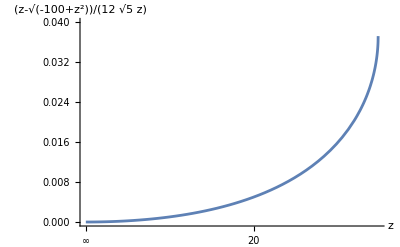

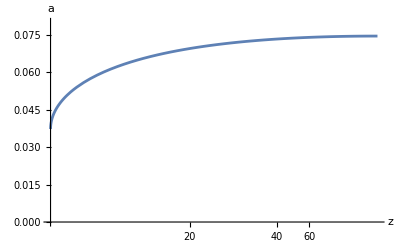

```mathematica
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[a, (in)]:=(l (z-√(-b1^2+z^2)))/(2 √2 b1^2 z)
Subscript[a, (out)]:=(l (z+√(-b1^2+z^2)))/(2 √2 b1^2 z)
Plot[Subscript[a, (in)],{z,b1,∞},PlotRange->{0,0.04},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{Style[z,Bold,Black],Style[Subscript[a, (in)],Bold,Black]}]
Plot[Subscript[a, (out)],{z,b1,∞},PlotRange->{0,0.08},AxesLabel->{Style[z,Bold,Black],Style[a,Bold,Black]}]
Clear[M,b1,b2,b3,l]
```

## F^θ

## Ingoing (F^θ)_(in)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))

### Setting up

```mathematica
<<GRQUICK.m
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

```mathematica
Metin["Schwar"]
```

Metric Success

```mathematica
Kin={1/f[r],-√(1-(ℓ^2 f[r])/r^2),0,ℓ/r^2};
Nin={1/2,(f[r] √(r^2-ℓ^2 f[r]))/(2 r),0,-(ℓ f[r])/(2 r^2)};
M1in={0,-(ℓ f[r])/(√2 r),ⅈ/(√2 r),-(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Mcin={0,-(ℓ f[r])/(√2 r),-ⅈ/(√2 r),-(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Ntin=FullSimplify[Nin+A[r] M1in+A[r] Mcin +A[r]^2 Kin];
Mtin=FullSimplify[M1in+A[r] Kin];
Mctin=FullSimplify[Mcin+A[r] Kin];
```

```mathematica
kin[a_]:=Kin[[a+1]]
nin[a_]:=Nin[[a+1]]
min[a_]:=M1in[[a+1]]
mcin[a_]:=Mcin[[a+1]]
ntin[a_]:=Ntin[[a+1]]
mtin[a_]:=Mtin[[a+1]]
mctin[a_]:=Mctin[[a+1]]
```

#### (F^θ)_(in)

```mathematica
FullSimplify[Simplify[
-(ⅈ σ)/ω{(Sum[Riemann[{{0},{b,c,d}}]kin[b]mtin[c]mctin[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{1},{b,c,d}}]kin[b]mtin[c]mctin[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{2},{b,c,d}}]kin[b]mtin[c]mctin[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{3},{b,c,d}}]kin[b]mtin[c]mctin[d],{b,0,3},{c,0,3},{d,0,3}])}/.{θ->Pi/2,f[r]->1-(2M)/r}]/.{A[r]->a},Assumptions->{M>0,r>2M,ℓ>0}]
```

{0,0,(3 M ℓ (√2 a ℓ-√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω),0}

(F^θ)_(in)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2))

#### Verification

```mathematica
Subscript[F^θ, (in)]==  FullSimplify[FullSimplify[-(ⅈ σ)/ω(Subscript[ℛ^θ, ttθ](k^t m^t(m̄)^θ+a k^t k^t(m̄)^θ+SuperStar[a] k^t m^t k^θ)+Subscript[ℛ^θ, tθt](k^t m^θ(m̄)^t+a k^t k^θ(m̄)^t+SuperStar[a] k^t m^θ k^t)+Subscript[ℛ^θ, rrθ](k^r m^r(m̄)^θ+a k^r k^r(m̄)^θ+SuperStar[a] k^r m^r k^θ)+Subscript[ℛ^θ, rθr](k^r m^θ(m̄)^r+a k^r k^θ(m̄)^r+SuperStar[a] k^r m^θ k^r)+Subscript[ℛ^θ, ϕθϕ](k^ϕ m^θ(m̄)^ϕ+a k^ϕ k^θ(m̄)^ϕ+SuperStar[a] k^ϕ m^θ k^ϕ)+Subscript[ℛ^θ, ϕϕθ](k^ϕ m^ϕ(m̄)^θ+a k^ϕ k^ϕ(m̄)^θ+SuperStar[a] k^ϕ m^ϕ k^θ))/.{k^θ->0,k^(t+θ)->0,k^(r+θ)->0,k^(θ+ϕ)->0,m^t->0,(m̄)^t->0,k^t->1/f[r],k^(2t)->1/f[r]^2,k^r->-√(1-ℓ^2/r^2 f[r]),k^(2r)->1-(ℓ^2 f[r])/r^2,k^ϕ->ℓ/r^2,k^(2ϕ)->ℓ^2/r^4,m^r->-(ℓ f[r])/(√2 r),m^θ->ⅈ/(√2 r),m^ϕ->-(√(r^2-ℓ^2 f[r]))/(√2 r^2),(m̄)^r->-(ℓ f[r])/(√2 r),(m̄)^θ->-ⅈ/(√2 r),(m̄)^ϕ->-(√(r^2-ℓ^2 f[r]))/(√2 r^2)}/.{Subscript[ℛ^θ, ttθ]->(2 M^2-M r)/r^4,Subscript[ℛ^θ, tθt]->-(2 M^2-M r)/r^4,Subscript[ℛ^θ, rrθ]->M/(r(r^2-2 M r)),Subscript[ℛ^θ, rθr]->-M/(r(r^2-2 M r)),Subscript[ℛ^θ, ϕθϕ]->(2 M Sin[θ]^2)/r,Subscript[ℛ^θ, ϕϕθ]->-(2 M Sin[θ]^2)/r,f[r]->1-(2M)/r},Assumptions->{M>0,r>2M,ℓ>0}]/.{θ->Pi/2,SuperStar[a]->a},Assumptions->{M>0,r>2M,ℓ>0}]
```

(F^θ)_in==(3 M ℓ (√2 a ℓ-√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω)

```mathematica
FullSimplify[(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2))-((3 M ℓ (√2 a ℓ-√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω))/.{f[r]->(1-(2M)/r)},Assumptions->{M>0,r>2M,ℓ>0}]
```

0

### (F^θ)_(in)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))

(F^θ)_(in)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2))
Going from r to z
(F^θ)_(in)=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z^3+p z+q)))/z^7)

```mathematica
FullSimplify[(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z^3+p z+q)))/z^7)-((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2)))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)
(F^θ)_(in)=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7)
Substituting    a_(in)=(l (z-√(-b1^2+z^2)))/(2 √2 b1^2 z)
(F^θ)_(in)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(z(z-b1)(z-b2)(z-b3)))/z^7))

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^7/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z^6-((b1 √(-b1^2+z^2)) b3)/(2 (z^7 (b1+z)))+O[b3]^2

From the boundary condition (F^θ)_(in)[∞] = 0

```mathematica
Subscript[F, (in)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
```

### Boundary Behaviour of (F^θ)_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[F, (in)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

z → b1

```mathematica
Subscript[Subscript[Fatb, 1], (in)]=FullSimplify[Limit[Subscript[F, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(3 l^3 σ)/(32 b1^8 M^3 ω)

## Outgoing (F^θ)_(out)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))

### Setting up

```mathematica
Kout={1/f[r],√(1-(ℓ^2 f[r])/r^2),0,ℓ/r^2};
Nout={1/2,-(f[r] √(r^2-ℓ^2 f[r]))/(2 r),0,-(ℓ f[r])/(2 r^2)};
Mout={0,-(ℓ f[r])/(√2 r),ⅈ/(√2 r),(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Mcout={0,-(ℓ f[r])/(√2 r),-ⅈ/(√2 r),(√(r^2-ℓ^2 f[r]))/(√2 r^2)};
Ntout=FullSimplify[Nout+A[r] Mout+A[r] Mcout +A[r]^2 Kout];
Mtout=FullSimplify[Mout+A[r] Kout];
Mctout=FullSimplify[Mcout+A[r] Kout];
```

```mathematica
kout[a_]:=Kout[[a+1]]
nout[a_]:=Nout[[a+1]]
mout[a_]:=Mout[[a+1]]
mcout[a_]:=Mcout[[a+1]]
ntout[a_]:=Ntout[[a+1]]
mtout[a_]:=Mtout[[a+1]]
mctout[a_]:=Mctout[[a+1]]
```

#### F^θ

```mathematica
FullSimplify[Simplify[
-(ⅈ σ)/ω{(Sum[Riemann[{{0},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{1},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{2},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}]),(Sum[Riemann[{{3},{b,c,d}}]kout[b]mtout[c]mctout[d],{b,0,3},{c,0,3},{d,0,3}])}/.{θ->Pi/2,f[r]->1-(2M)/r}]/.{A[r]->a},Assumptions->{M>0,r>2M,ℓ>0}]
```

{0,0,(3 M ℓ (√2 a ℓ+√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω),0}

F^θ=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))

#### Verification

```mathematica
F^θ==  FullSimplify[FullSimplify[-(ⅈ σ)/ω(Subscript[ℛ^θ, ttθ](k^t m^t(m̄)^θ+a k^t k^t(m̄)^θ+SuperStar[a] k^t m^t k^θ)+Subscript[ℛ^θ, tθt](k^t m^θ(m̄)^t+a k^t k^θ(m̄)^t+SuperStar[a] k^t m^θ k^t)+Subscript[ℛ^θ, rrθ](k^r m^r(m̄)^θ+a k^r k^r(m̄)^θ+SuperStar[a] k^r m^r k^θ)+Subscript[ℛ^θ, rθr](k^r m^θ(m̄)^r+a k^r k^θ(m̄)^r+SuperStar[a] k^r m^θ k^r)+Subscript[ℛ^θ, ϕθϕ](k^ϕ m^θ(m̄)^ϕ+a k^ϕ k^θ(m̄)^ϕ+SuperStar[a] k^ϕ m^θ k^ϕ)+Subscript[ℛ^θ, ϕϕθ](k^ϕ m^ϕ(m̄)^θ+a k^ϕ k^ϕ(m̄)^θ+SuperStar[a] k^ϕ m^ϕ k^θ))/.{k^θ->0,k^(t+θ)->0,k^(r+θ)->0,k^(θ+ϕ)->0,m^t->0,(m̄)^t->0,k^t->1/f[r],k^(2t)->1/f[r]^2,k^r->√(1-ℓ^2/r^2 f[r]),k^(2r)->1-(ℓ^2 f[r])/r^2,k^ϕ->ℓ/r^2,k^(2ϕ)->ℓ^2/r^4,m^r->-(ℓ f[r])/(√2 r),m^θ->ⅈ/(√2 r),m^ϕ->(√(r^2-ℓ^2 f[r]))/(√2 r^2),(m̄)^r->-(ℓ f[r])/(√2 r),(m̄)^θ->-ⅈ/(√2 r),(m̄)^ϕ->(√(r^2-ℓ^2 f[r]))/(√2 r^2)}/.{Subscript[ℛ^θ, ttθ]->(2 M^2-M r)/r^4,Subscript[ℛ^θ, tθt]->-(2 M^2-M r)/r^4,Subscript[ℛ^θ, rrθ]->M/(r(r^2-2 M r)),Subscript[ℛ^θ, rθr]->-M/(r(r^2-2 M r)),Subscript[ℛ^θ, ϕθϕ]->(2 M Sin[θ]^2)/r,Subscript[ℛ^θ, ϕϕθ]->-(2 M Sin[θ]^2)/r,f[r]->1-(2M)/r},Assumptions->{M>0,r>2M,ℓ>0}]/.{θ->Pi/2,SuperStar[a]->a},Assumptions->{M>0,r>2M,ℓ>0}]
```

F^θ==(3 M ℓ (√2 a ℓ+√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω)

```mathematica
FullSimplify[(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))-((3 M ℓ (√2 a ℓ+√(r^2-ℓ^2+(2 M ℓ^2)/r)) σ)/(r^6 ω))/.{f[r]->(1-(2M)/r)},Assumptions->{M>0,r>2M,ℓ>0}]
```

0

### (F^θ)_(out)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))

(F^θ)_(out)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))
Going from r to z
(F^θ)_(out)=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z^3+p z+q)))/z^7)

```mathematica
FullSimplify[(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z^3+p z+q)))/z^7)-((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2)))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)    and 
(F^θ)_(out)=(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)
Substituting    a_(out)=(l (z+√(-b1^2+z^2)))/(2 √2 b1^2 z)
(F^θ)_(out)=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(z(z-b1)(z-b2)(z-b3)))/z^7))

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^7/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^7,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z^6-((b1 √(-b1^2+z^2)) b3)/(2 (z^7 (b1+z)))+O[b3]^2

From the boundary condition (F^θ)_(out)[b1] =(F^θ)_(in)[b1]

```mathematica
Subscript[F, (out)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
```

### Boundary Behaviour of (F^θ)_(out)

z → b1

```mathematica
Subscript[Subscript[Fatb, 1], (out)]=FullSimplify[Limit[Subscript[F, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(3 l^3 σ)/(32 b1^8 M^3 ω)

```mathematica
Subscript[Subscript[Fatb, 1], (out)]-Subscript[Subscript[Fatb, 1], (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[F, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

0

## Numeric Verification of F^θ

### Setting up Numerics

```mathematica
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[F, (in)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
Subscript[F, (out)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
```

(F^θ)_(in)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r-√(1-(ℓ^2 f[r])/r^2))     = (3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7)
(F^θ)_(out)=(3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))      =(3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)

### (F^θ)_(in)

```mathematica
M:=1/2
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[F, (in)],z->U]]
numeric1==N[Limit[(3 l σ)/(16 M^3 ω)((√2 NIntegrate[Subscript[Az, (in)],{z,L,U}]l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7),z->U]]
numeric2==N[Limit[(3 M ℓ σ)/(r^5 ω)((√2 NIntegrate[Subscript[Ar, (in)]/.{f[r]->1-(2M)/r},{r,(2M ) L,(2M ) U}] ℓ)/r-√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},r->(2M ) U]]
Clear[M,b1,b2,b3,l,ℓ,L,U]
```

analytic==(0.00033541 σ)/ω

numeric1==(0.000351607 σ)/ω

numeric2==(0.000351607 σ)/ω

### (F^θ)_(out)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
U:=∞
analytic==N[Limit[Subscript[F, (out)],z->U]]
numeric1==N[Limit[(3 l σ)/(16 M^3 ω)((√2(NIntegrate[Subscript[Az, (in)],{z,Lin,b1}]+NIntegrate[Subscript[Az, (out)],{z,b1,U}]) l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7),z->U]]
numeric2==N[Limit[(3 M ℓ σ)/(r^5 ω)((√2 (NIntegrate[Subscript[Ar, (in)]/.{f[r]->1-(2M)/r},{r,(2M ) Lin,(2M ) b1}]+NIntegrate[Subscript[Ar, (out)]/.{f[r]->1-(2M)/r},{r,(2M ) b1,(2M ) U}]) ℓ)/r+√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},r->(2M ) U]]
Clear[b1,b2,b3,l,ℓ,M,U]
```

analytic==0.

numeric1==0.

numeric2==0.

## Plots of F^θ

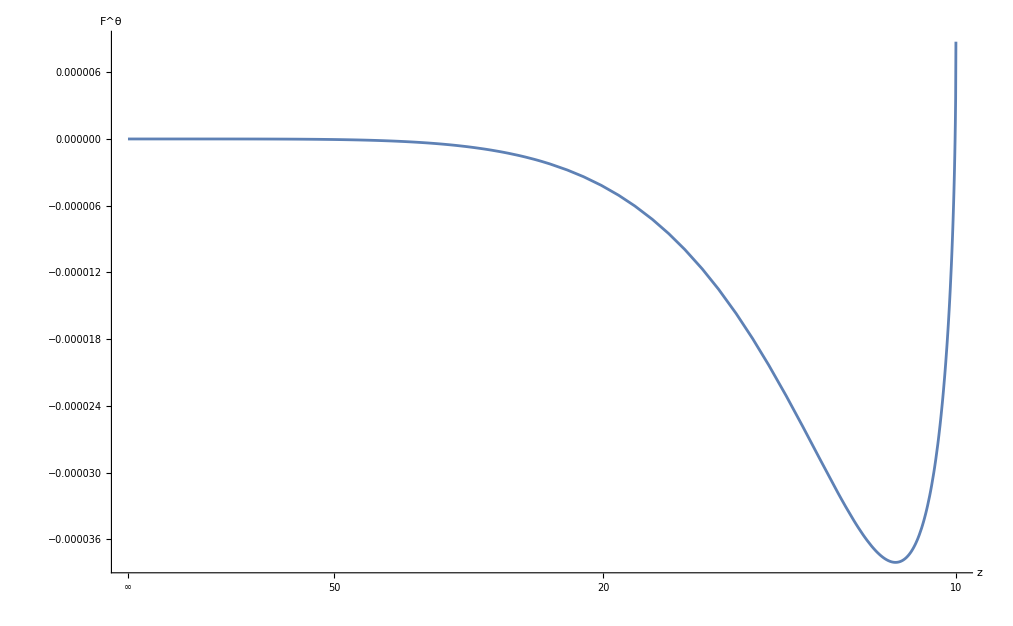

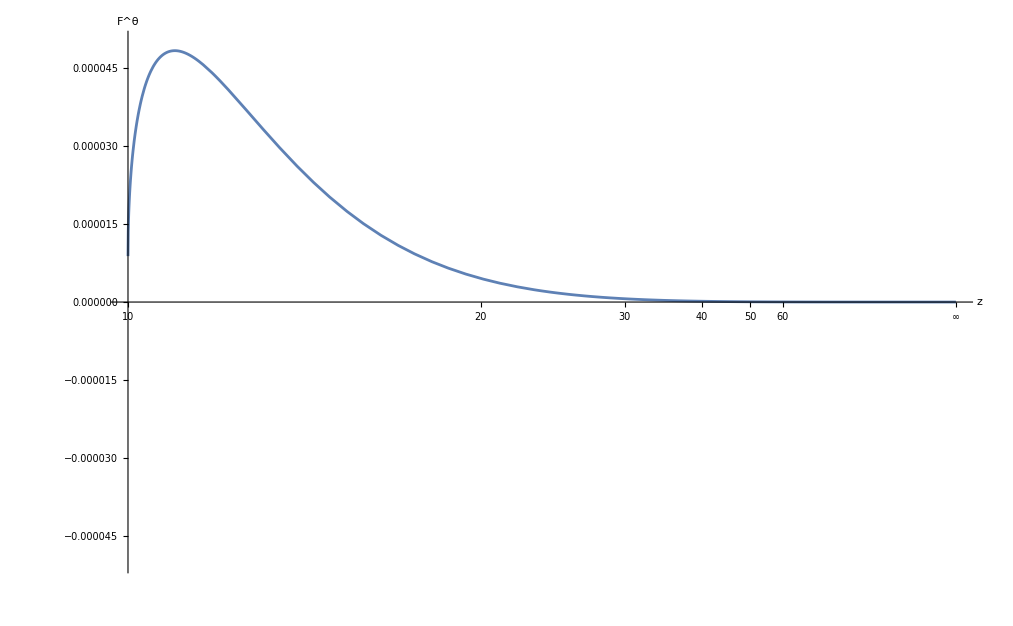

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[F, (in)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
Subscript[F, (out)]:=(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))
Plot[Subscript[F, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{Style[z,Bold,Black],Style[F^θ,Bold,Black]}]
Plot[Subscript[F, (out)],{z,b1,∞},PlotRange->{-0.00005,0.00005},AxesLabel->{Style[z,Bold,Black],Style[F^θ,Bold,Black]}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## q_0^θ

q1^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

## Ingoing

q1_(in)^θ=   1/r^2(C[1(in)]+∫(r^2(F^θ)_(in))/(k_(in)^r)ⅆr)   =     1/(4 M^2 z^2)( C[1(in)]+∫8 M^3(z^2(F^θ)_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[1(in)]+g_(in))

### k_(in)^r=-(√(-b1^2+z^2))/z

```mathematica
Subscript[krr, (in)]:=-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
```

k_(in)^r=-√(1-(ℓ^2 f[r])/r^2)=-√((l^2-l^2 z+z^3)/z^3)

```mathematica
FullSimplify[-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,z>0}]
```

-√((l^2-l^2 z+z^3)/z^3)

Substituting   q  for l^2 ,     p  for -l^2
k_(in)^r=-(√(z(z^3+p z+q)))/z^2
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)

```mathematica
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
```

Verification

```mathematica
FullSimplify[-(√(z(z^3+p z+q)))/z^2-(-√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
-(√(z(z-b1)(z-b2)(z-b3)))/z^2/.{b2->-b1-b3}
```

-(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2

```mathematica
FullSimplify[Series[-(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

-(√(-b1^2+z^2))/z+(b1 √(-b1^2+z^2) b3)/(2 z^2 (b1+z))+O[b3]^2

```mathematica
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
```

#### Boundary Behaviour of k_(in)^r

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kr, (in)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

-1

z → b1

```mathematica
Subscript[Subscript[kratb, 1], (in)]=FullSimplify[Limit[Subscript[kr, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

0

### g_(in)=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))

g_(in)=∫8 M^3(z^2(F^θ)_(in))/(k_(in)^r)ⅆz      =      ∫(3 l σ)/(2 ω)(l^2/(2 b1^2 z^4)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^5)+(√(-b1^2+z^2))/z^4))/k^r ⅆz 
Substituting    k_(in)^r=-(√(-b1^2+z^2))/z
g_(in)= ∫(3 l σ)/(2 ω)(1/z^3+l^2/(2 b1^2 z^4)-l^2/(2 b1^2 z^3 √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l σ)/(2 ω)(1/z^3+l^2/(2 b1^2 z^4)-l^2/(2 b1^2 z^3 √(-b1^2+z^2)))-(8 M^3(z^2 F^θ)/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),F^θ->(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)-((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(2 ω)(FullSimplify[Integrate[-l^2/(2 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[1/z^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[l^2/(2 b1^2 z^4),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ (-l^2/(6 b1^2 z^3)-1/(2 z^2)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1^5 z^2)))/(2 ω)

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g, (in)]:=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))
```

#### Boundary Behaviour of g_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[gatb1, (in)]=FullSimplify[Limit[Subscript[g, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

-((12 b1^3 l+l^3 (4-3 π)) σ)/(16 b1^5 ω)

### q1_(in)^θ=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))

q1_(in)^θ   =   1/(4 M^2 z^2)( C[1(in)]+g_(in)) =   (g_(in))/(4 M^2 z^2)    ,since  g_(in)[∞] = 0

```mathematica
Subscript[q1, (in)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
```

```mathematica
FullSimplify[Subscript[q1, (in)]-(g/(4 M^2 z^2))/.{g->(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q1, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q1atb1, (in)]=FullSimplify[Limit[Subscript[q1, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l (-12 b1^3+l^2 (-4+3 π)) σ)/(64 b1^7 M^2 ω)

```mathematica
FullSimplify[(l σ)/ω((-12 b1^3+l^2 (-4+3 π))/(64 b1^7 M^2))-(Subscript[q1atb1, (in)])]
```

0

## Outgoing

q1_(out)^θ=   1/r^2(C[1(out)]+∫(r^2(F^θ)_(out))/(k_(out)^r)ⅆr)   =      1/(4 M^2 z^2)( C[1(out)]+∫8 M^3(z^2 F^θ)/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[1(out)]+g_(out))

### k_(out)^r=(√(-b1^2+z^2))/z

```mathematica
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
```

k_(out)^r=√(1-(ℓ^2 f[r])/r^2)=√((z^3-l^2 z+l^2)/z^3)

```mathematica
FullSimplify[√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,z>0}]
```

√((l^2-l^2 z+z^3)/z^3)

Substituting   q  for l^2 ,     p  for -l^2
k_(out)^r=(√(z(z^3+p z+q)))/z^2
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)

```mathematica
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
```

Verification

```mathematica
FullSimplify[(√(z(z^3+p z+q)))/z^2-(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^2/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z-((b1 √(-b1^2+z^2)) b3)/(2 (z^2 (b1+z)))+O[b3]^2

```mathematica
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
```

#### Boundary Behaviour of k_(out)^r

z → b1

```mathematica
Subscript[Subscript[kratb, 1], (out)]=FullSimplify[Limit[Subscript[kr, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

0

```mathematica
Subscript[Subscript[kratb, 1], (out)]-Subscript[Subscript[kratb, 1], (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kr, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

1

### g_(out)=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))

g_(out)=∫8 M^3(z^2 F^θ)/(k_(out)^r)ⅆz      =∫8 M^3(z^2((3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))))/(k_(out)^r)ⅆz  
Substituting    k_(out)^r=(√(-b1^2+z^2))/z
g_(out)= ∫(3 l σ)/(2 ω)(l^2/(2 b1^2 z^3 √(-b1^2+z^2))+1/z^3+l^2/(2 b1^2 z^4))ⅆz

```mathematica
FullSimplify[(3 l σ)/(2 ω)(l^2/(2 b1^2 z^3 √(-b1^2+z^2))+1/z^3+l^2/(2 b1^2 z^4))-(8 M^3(z^2 F^θ)/k^r)/.{k^-r->z/(√(-b1^2+z^2)),F^θ->(3 l σ)/(16 M^3 ω)(l^2/(2 b1^2 z^6)+((l^2 √(-b1^2+z^2))/(2 b1^2 z^7)+(√(-b1^2+z^2))/z^6))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(2 ω)(FullSimplify[Integrate[l^2/(2 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[1/z^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[l^2/(2 b1^2 z^4),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ (-l^2/(6 b1^2 z^3)-1/(2 z^2)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1^5 z^2)))/(2 ω)

From the boundary condition   g_(out)[b1]=g_(in)[b1]

```mathematica
Subscript[g, (out)]:=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))
```

```mathematica
FullSimplify[(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))-((3 l σ)/(4 ω)((l^2 π)/(4 b1^5)+(l^2 √(-b1^2+z^2))/(2 b1^4 z^2)-l^2/(3 b1^2 z^3)-1/z^2+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))]
```

0

#### Boundary Behaviour of g_(out)

z → b1

```mathematica
Subscript[gatb1, (out)]=FullSimplify[Limit[Subscript[g, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

-((12 b1^3 l+l^3 (4-3 π)) σ)/(16 b1^5 ω)

```mathematica
Subscript[gatb1, (out)]-Subscript[gatb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(3 l^3 π σ)/(8 b1^5 ω)

### q1_(out)^θ=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))

q1_(out)^θ   =   1/(4 M^2 z^2)( C[1]+g_(out)) =   (g_(out))/(4 M^2 z^2)    ,since  g_(out)[b1] = g_(in)[b1]

```mathematica
Subscript[q1, (out)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
```

```mathematica
FullSimplify[ Subscript[q1, (out)]-(g/(4 M^2 z^2))/.{g->(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q1atb1, (out)]=FullSimplify[Limit[Subscript[q1, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l (-12 b1^3+l^2 (-4+3 π)) σ)/(64 b1^7 M^2 ω)

```mathematica
Subscript[q1atb1, (out)]-Subscript[q1atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q1, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of k^r

### Setting up Numerics

```mathematica
Subscript[krr, (in)]:=-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
```

### (k^r)_(in)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=1.1b1
analytic==N[Subscript[kr, (in)]/.{z->U}]
numericz==N[Subscript[krz, (in)]/.{z->U}]
numericr==N[Subscript[krr, (in)]/.{f[r]->1-(2M)/r}/.{r->(2M ) U}]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==-0.416598

numericz==-0.393409-5.99698×10^-18 ⅈ

numericr==-0.393409

### (k^r)_(out)

```mathematica
b1:=5
M:=1/2
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=b1
U:=∞
analytic==Limit[Subscript[kr, (out)],z->U]
numericz==Limit[Subscript[krz, (out)],z->U]
numericr==Limit[Subscript[krr, (out)]/.{f[r]->1-(2M)/r},r->(2M ) U]
Clear[b1,b2,b3,l,ℓ,M,L,U]
```

analytic==1

numericz==1

numericr==1

## Numeric Verification of g

### Setting up Numerics

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gr_(in)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a_(in) ℓ)/r-√(1-(ℓ^2 f[r])/r^2)))/(krr_(in))=(3 M ℓ σ (-√2 a_(in)ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))
Gz_(in)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(in))=(3 l (1-(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
Gz_(out)=8 M^3(z^2((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)))/(krz_(out))=(3 l (1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
Gr_(out)=(r^2((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))))/(krr_(out))=(3 M ℓ σ)/(r^3 ω)(1+(√2 a ℓ)/(r √(1-((-2 M+r) ℓ^2)/r^3)))

```mathematica
Clear[M,σ,ω,b1,l,U,z]
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[g, (in)]:=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))
Subscript[g, (out)]:=(3 l σ)/(4 ω)((l^2 π)/(4 b1^5)-1/z^2-l^2/(3 b1^2 z^3)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5)))
```

### g_(in)

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=10000
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g, (in)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,L,Z}]
numeric1==NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,U}]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M)L,R}]
numeric2==NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) L,(2M ) U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intAzin,intArin]
```

analytic==-0.0000750004

numeric1==-0.0000750004+2.63258×10^-25 ⅈ

numeric2==-0.0000750004

### g_(out)

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=10000
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g, (out)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,Z}]
Subscript[gz, (in)]:=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,L}]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,L}]+NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numeric1==N[Subscript[gz, (in)]+NIntegrate[(3 l)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ,{z,L,U}]]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M)Lin,R}]
Subscript[gr, (in)]:=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) Lin,(2M ) L}]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,(2M )L}]+NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numeric2==N[Subscript[gr, (in)]+NIntegrate[(3 M ℓ σ)/(r^3 ω)(1+(√2(intArout[r]) ℓ)/(r √(1-((-2 M+r) ℓ^2)/r^3))),{r,(2M ) L,(2M ) U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U,intAzin,intArin,intAzout,intArout]
```

analytic==1.17827×10^-8

numeric1==1.17785×10^-8+2.63258×10^-25 ⅈ

numeric2==1.17785×10^-8

## Numeric Verification of q_0^θ

### Setting up Numerics

q1^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gr_(in)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a_(in) ℓ)/r-√(1-(ℓ^2 f[r])/r^2)))/(krr_(in))=(3 M ℓ σ (-√2 a_(in)ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))
Gz_(in)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(in))=(3 l (1-(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
Gz_(out)=8 M^3(z^2((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)))/(krz_(out))=(3 l (1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
Gr_(out)=(r^2((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))))/(krr_(out))=(3 M ℓ σ (√2 a ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))

```mathematica
Clear[M,σ,ω,b1,l,U,z]
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[q1, (in)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
Subscript[q1, (out)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
```

### (q1^θ)_(in)

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q1, (in)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,L,Z}]
zq1InNumeric==Limit[1/(4 M^2 z^2)(NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,U}]),z-> U]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M)L,R}]
rq1InNumeric==Limit[1/r^2(NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) L,(2M ) U}]),r->(2M ) U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intAzin,intArin]
```

analytic==-6.005×10^-6

zq1InNumeric==-6.00458×10^-6+1.03828×10^-24 ⅈ

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

rq1InNumeric==-6.00458×10^-6

### (q1^θ)_(out)

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q1, (out)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,Z}]
Subscript[gz, (in)]:=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,L}]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,L}]+NIntegrate[Subscript[Az, (out)],{z,L,Z}]
zq1OutNumeric==Limit[1/(4 M^2 z^2)(Subscript[gz, (in)]+NIntegrate[(3 l)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ,{z,L,U}]),z->U]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M)Lin,R}]
Subscript[gr, (in)]:=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) Lin,(2M ) L}]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,(2M )L}]+NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
rq1OutNumeric==Limit[1/r^2(Subscript[gr, (in)]+NIntegrate[(3 M ℓ σ (√2 (intArout[r]) ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) L,(2M ) U}]),r->(2M ) U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U,intAzin,intArin,intAzout,intArout]
```

analytic==0.

zq1OutNumeric==0.+0. ⅈ

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

rq1OutNumeric==0.

## Plots of q_0^θ

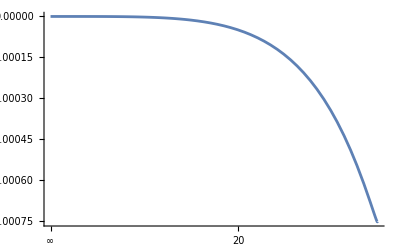

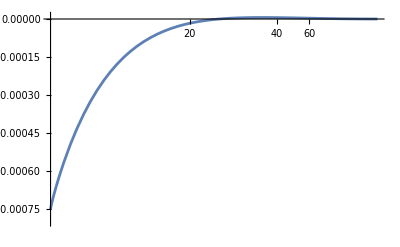

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[q1, (in)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
Subscript[q1, (out)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
Plot[Subscript[q1, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[q1, (out)],{z,b1,∞},PlotRange->{-0.0008,0.00001}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ_0

θ1=  C[2]+∫q1^θ/k^r ⅆr       =  C[2]+∫(2 M q1^θ)/k^r ⅆz

## Ingoing

θ1_(in) = C[2]+∫(2 M q1_(in)^θ)/(k_(in)^r)ⅆz

### θ1_(in)=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))

θ1_(in) = C[2]+∫(2 M q_(in)^θ)/(k_(in)^r)ⅆz
= C[2]+∫(3 l σ)/(8M ω)(l^2/(2 b1^4 z^3)+l^2/(3 b1^2 z^4 √(-b1^2+z^2))+1/(z^3 √(-b1^2+z^2))-(l^2 π)/(4 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l σ)/(8M ω)(l^2/(2 b1^4 z^3)+l^2/(3 b1^2 z^4 √(-b1^2+z^2))+1/(z^3 √(-b1^2+z^2))-(l^2 π)/(4 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)))-((2 M q^θ)/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),q^θ->(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(8M ω)(FullSimplify[Integrate[l^2/(2 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(3 b1^2 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 π)/(4 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ (-l^2/(4 b1^4 z^2)+(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(9 b1^6 z^3)-(l^2 π ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^3 z^2)))/(8 M ω)

=(3 l σ)/(8 M ω)(-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))

From the boundary condition  θ1_(in)[∞] = 0

```mathematica
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))
```

```mathematica
FullSimplify[Subscript[θ1, (in)]-((3 l σ (-l^2/(4 b1^4 z^2)+(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(9 b1^6 z^3)-(l^2 π ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^3 z^2)-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)))/(8 M ω)),Assumptions->{M>0,z>0}]
```

0

#### Boundary Behaviour of θ1_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ1, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ1atb1, (in)]=FullSimplify[Limit[Subscript[θ1, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l (-36 b1^3 π+l^2 (-68+9 π^2)) σ)/(384 b1^6 M ω)

## Outgoing

θ1_(out) = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz

### θ1_(out)=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))

θ1_(out) = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz
= C[2]+∫(3 l σ)/(8 M ω)(l^2/(2 b1^4 z^3)-l^2/(3 b1^2 z^4 √(-b1^2+z^2))-1/(z^3 √(-b1^2+z^2))+(l^2 π)/(4 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l σ)/(8 M ω)(l^2/(2 b1^4 z^3)-l^2/(3 b1^2 z^4 √(-b1^2+z^2))-1/(z^3 √(-b1^2+z^2))+(l^2 π)/(4 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)))-((2 M q^θ)/k^r)/.{k^-r->z/(√(-b1^2+z^2)),q^θ->(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(8 M ω)(FullSimplify[Integrate[l^2/(2 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(3 b1^2 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 π)/(4 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ (-l^2/(4 b1^4 z^2)-(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(9 b1^6 z^3)+(l^2 π ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((b1 √(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^3)))/(8 M ω)

=(3 l σ)/(8 M ω)(-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))

```mathematica
FullSimplify[(3 l σ)/(8 M ω)(-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))-((3 l σ (-l^2/(4 b1^4 z^2)-(l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(9 b1^6 z^3)+(l^2 π ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((b1 √(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^3)))/(8 M ω)),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition  θ1_(out)[b1] = θ1_(in)[b1]

```mathematica
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))
```

#### Boundary Behaviour of θ1_(out)

z → b1

```mathematica
Subscript[θ1atb1, (out)]=FullSimplify[Limit[Subscript[θ1, (out)] ,z->b1],Assumptions->{z>0,b1>0}]
```

(l (-36 b1^3 π+l^2 (-68+9 π^2)) σ)/(384 b1^6 M ω)

```mathematica
Subscript[θ1atb1, (out)]-Subscript[θ1atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ1, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l (-18 b1^3 π+l^2 (-16+9 π^2)) σ)/(96 b1^6 M ω)

#### linear approximation

```mathematica
FullSimplify[Series[Subscript[θ1, (out)],{z,∞,2}],Assumptions->{M>0,b1>0,z>0}]
```

(l (-18 b1^3 π+l^2 (-16+9 π^2)) σ)/(96 b1^6 M ω)-(3 (l^3 π σ))/(16 (b1^5 M ω) z)+O[1/z]^3

```mathematica
Subscript[θ1Linear, (out)]:=(l (-18 b1^3 π+l^2 (-16+9 π^2)) σ)/(96 b1^6 M ω)-(3 (l^3 π σ))/(16 (b1^5 M ω) z)
```

## Numeric Verification of θ_0

### Setting up Numerics

q1^θ=  1/r^2( C[1]+∫(r^2 F^θ)/k^r ⅆr)   =   1/(4 M^2 z^2)( C[1]+∫8 M^3(z^2 F^θ)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[1]+g)

Let G =g_(, r)
G=(r^2 F^θ)/k^r = 8 M^3(z^2 F^θ)/k^r
⇒g=∫Gⅆz 
Gr_(in)=(r^2(3 M ℓ σ)/(r^5 ω)((√2 a_(in) ℓ)/r-√(1-(ℓ^2 f[r])/r^2)))/(krr_(in))=(3 M ℓ σ (-√2 a_(in)ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))
Gz_(in)=8 M^3(z^2(3 l σ)/(16 M^3 ω)((√2 a l)/z^6-(√(z(z-b1)(z-b2)(z-b3)))/z^7))/(krz_(in))=(3 l (1-(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
Gr_(out)=(r^2((3 M ℓ σ)/(r^5 ω)((√2 a ℓ)/r+√(1-(ℓ^2 f[r])/r^2))))/(krr_(out))=(3 M ℓ σ (√2 a ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))
Gz_(out)=8 M^3(z^2((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)))/(krz_(out))=(3 l (1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)
θ1_(r(in))=  ∫(q_(in)^θ)/(k_(in)^r)ⅆr
θ1_(z(in)) =∫(2 M q_(in)^θ)/(k_(in)^r)ⅆz
θ1_(r(out))=  C[2]+∫(q_(in)^θ)/(k_(in)^r)ⅆr
θ1_(z(out))  = C[2]+∫(2 M q_(out)^θ)/(k_(out)^r)ⅆz

```mathematica
Subscript[Ar, (in)]:=-(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (in)]:=-l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[Ar, (out)]:=(M ℓ)/(√2 r^2 √(r^2-ℓ^2 f[r]))/.{f[r]->1-(2M)/r}
Subscript[Az, (out)]:=l/(2 √2 z √(z(z-b1)(z-b2)(z-b3)))
Subscript[krr, (in)]:=-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ1Linear, (out)]:=(l (-18 b1^3 π+l^2 (-16+9 π^2)) σ)/(96 b1^6 M ω)-(3 (l^3 π σ))/(16 (b1^5 M ω) z)
```

### θ1_(in)

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ1, (in)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,L,Z}]
zgInNumeric[Z_?NumericQ]:=zgInNumeric[Z]=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,L,Z}]
zθ1InNumeric ==NIntegrate[-(zgInNumeric[z])/(2 M √(z(z-b1)(z-b2)(z-b3))),{z,L,U}]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )L,R}]
rgInNumeric[R_?NumericQ]:=rgInNumeric[R]=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M )L,R}]
rθ1InNumeric ==NIntegrate[-(rgInNumeric[r])/(r √(r^2-((-2 M+r) ℓ^2)/r)),{r,(2M ) L,(2M ) U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-0.0251303

numericz==-0.0263576+3.44762×10^-19 ⅈ

numericr==-0.0263576

### θ1_(out)

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=300000
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ1, (out)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,Z}]
Subscript[gz, (in)]:=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,L}]
numericgzin[Z_?NumericQ]:=numericgzin[Z]=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,Z}]
θ1zin :=NIntegrate[-(numericgzin[z])/(2 M √(z(z-b1)(z-b2)(z-b3))),{z,Lin,L}]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,L}]+NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numericgzout[Z_?NumericQ]:=numericgzout[Z]=NIntegrate[(3 l)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ,{z,L,Z}]
zθ1OutNumeric ==N[θ1zin+NIntegrate[(Subscript[gz, (in)]+numericgzout[z])/(2 M  z^2 Subscript[krz, (out)]),{z,L,U}]]
intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,R}]
Subscript[gr, (in)]:=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M )Lin,(2M )L}]
numericgrin[R_?NumericQ]:=numericgrin[R]=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M )Lin,R}]
θ1rin :=NIntegrate[-(numericgrin[r])/(r √(r^2-((-2 M+r) ℓ^2)/r)),{r,(2M )Lin,(2M )L}]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,(2M )L}]+NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numericgrout[R_?NumericQ]:=numericgrout[R]=NIntegrate[(3 M ℓ σ (√2 (intArout[r]) ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M )L,R}]
rθ1OutNumeric  ==N[θ1rin+NIntegrate[(Subscript[gr, (in)]+numericgrout[r])/(r^2 Subscript[krr, (out)]),{r,(2M ) L,(2M ) U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intAzin,numericgzin,θzin,intAzout,numericgzout,intArin,numericgrin,θrin,intArout,numericgrout]
```

analytic==-1.30899×10^-11

zθ1OutNumeric==-1.30899×10^-11-1.11928×10^-27 ⅈ

rθ1OutNumeric==-1.30899×10^-11

```mathematica
N[100-(100)(-1.3089935013106253*^-11/-1.308994463189541*^-11)]
```

0.0000734823

### Accuracy of linear approximation

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=2b1
θ1linear==N[Limit[Subscript[θ1Linear, (out)],z->U]]
analytic==N[Limit[Subscript[θ1, (out)],z->U]]
intAzin[Z_?NumericQ]:=intAzin[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,Z}]
Subscript[gz, (in)]:=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,L}]
numericgzin[Z_?NumericQ]:=numericgzin[Z]=NIntegrate[(3 l σ)/(2 z^3 ω)(1-(√2 (intAzin[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))),{z,Lin,Z}]
θ1zin :=NIntegrate[-(numericgzin[z])/(2 M √(z(z-b1)(z-b2)(z-b3))),{z,Lin,L}]
intAzout[Z_?NumericQ]:=intAzout[Z]=NIntegrate[Subscript[Az, (in)],{z,Lin,L}]+NIntegrate[Subscript[Az, (out)],{z,L,Z}]
numericgzout[Z_?NumericQ]:=numericgzout[Z]=NIntegrate[(3 l)/(2 z^3 ω)(1+(√2 (intAzout[z]) l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ,{z,L,Z}]
numericz ==N[θ1zin+NIntegrate[(Subscript[gz, (in)]+numericgzout[z])/(2 M  z^2 Subscript[krz, (out)]),{z,L,U}]]

intArin[R_?NumericQ]:=intArin[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,R}]
Subscript[gr, (in)]:=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) Lin,(2M ) L}]
numericgrin[R_?NumericQ]:=numericgrin[R]=NIntegrate[(3 M ℓ σ (-√2 (intArin[r])ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) Lin,R}]
θ1rin :=NIntegrate[-(numericgrin[r])/(r √(r^2-((-2 M+r) ℓ^2)/r)),{r,(2M ) Lin,(2M ) L}]
intArout[R_?NumericQ]:=intArout[R]=NIntegrate[Subscript[Ar, (in)],{r,(2M )Lin,(2M )L}]+NIntegrate[Subscript[Ar, (out)],{r,(2M )L,R}]
numericgrout[R_?NumericQ]:=numericgrout[R]=NIntegrate[(3 M ℓ σ (√2 (intArout[r]) ℓ+r √(1-(ℓ^2 f[r])/r^2)))/(r^4 ω √(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r},{r,(2M ) L,R}]
numericr ==N[θ1rin+NIntegrate[(Subscript[gr, (in)]+numericgrout[r])/(r^2 Subscript[krr, (out)]),{r,(2M ) L,(2M ) U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intAzin,numericgzin,θzin,intAzout,numericgzout,intArin,numericgrin,θrin,intArout,numericgrout]
```

θlinear==-0.0113312

analytic==-0.0109953

numericz==-0.0112054+0. ⅈ

numericr==-0.0112054

The linear approximation is accurate for detections as near as 2b1 for b1 = 10
This is sufficient for almost all astronomically relevant cases (with b1 > 10) excluding Black holes

## Plots of θ_0

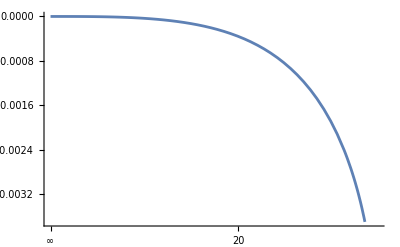

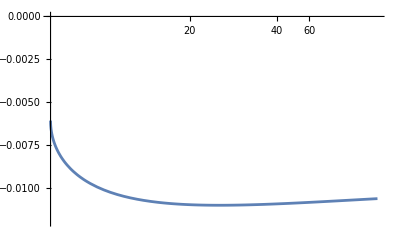

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Plot[Subscript[θ1, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[θ1, (out)],{z,b1,∞},PlotRange->{-0.012,0}]
Clear[b1,b2,b3,l,M,σ,ω]
```

### Plot of θ1Linear_(out)

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[Subscript[θ1Linear, (out)],{z,b1,∞},PlotRange->{-0.012,0}]
Clear[b1,b2,b3,l,M,σ,ω]
```

-Graphics-

### Comparison of θ1Linear_(out) and θ1_(out)

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[{Subscript[θ1, (out)],Subscript[θ1Linear, (out)]},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

-Graphics-

θLinear_(out)    approaches    θ_(out)   for z as small as 4 b1

## q_1^θ

q2^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ1)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]-h)

## Ingoing

q2_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]-h_(in))

### k_(in)^r=-(√(-b1^2+z^2))/z

```mathematica
Subscript[krr, (in)]:=-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
```

k_(in)^r=-√(1-(ℓ^2 f[r])/r^2)=-√((l^2-l^2 z+z^3)/z^3)

```mathematica
FullSimplify[-√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,z>0}]
```

-√((l^2-l^2 z+z^3)/z^3)

Substituting   q  for l^2 ,     p  for -l^2
k_(in)^r=-(√(z(z^3+p z+q)))/z^2
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)

```mathematica
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
```

Verification

```mathematica
FullSimplify[-(√(z(z^3+p z+q)))/z^2-(-√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
-(√(z(z-b1)(z-b2)(z-b3)))/z^2/.{b2->-b1-b3}
```

-(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2

```mathematica
FullSimplify[Series[-(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

-(√(-b1^2+z^2))/z+(b1 √(-b1^2+z^2) b3)/(2 z^2 (b1+z))+O[b3]^2

```mathematica
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
```

#### Boundary Behaviour of k_(in)^r

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kr, (in)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

-1

z → b1

```mathematica
Subscript[Subscript[kratb, 1], (in)]=FullSimplify[Limit[Subscript[kr, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

0

### h_(in)

h_(in)=∫8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)ⅆz
Substituting    θ1_(in) =(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
h_(in)=    ∫8 M^3(z^2(k^ϕ)^2(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))))/(k_(in)^r)ⅆz
Substituting    k_(in)^r=-(√(-b1^2+z^2))/z             ,k^ϕ=ℓ/r^2=ℓ/(4 M^2 z^2)
h_(in)== ∫(3 l σ)/(8 b1^6 ω)(-(4 l^4)/(9 z^2)-(b1^4 l^2)/z^3-(2 b1^2 l^4)/(9 z^4)+(36 b1^3 l^2 π+l^4 (32-9 π^2))/(72 z √(-b1^2+z^2))+(b1^2 l^4)/(2 z^3 √(-b1^2+z^2))+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2))-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[(3 l σ)/(8 b1^6 ω)(-(4 l^4)/(9 z^2)-(b1^4 l^2)/z^3-(2 b1^2 l^4)/(9 z^4)+(36 b1^3 l^2 π+l^4 (32-9 π^2))/(72 z √(-b1^2+z^2))+(b1^2 l^4)/(2 z^3 √(-b1^2+z^2))+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2))-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)))-(8 M^3(z^2(k^ϕ)^2 Subscript[θ1, (in)])/Subscript[k, (in)]^r)/.{Subscript[k, (in)]^-r->-z/(√(-b1^2+z^2)),k^ϕ->ℓ/r^2,k^(2ϕ)->ℓ^2/r^4,Subscript[θ1, (in)] ->(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3)))}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l σ)/(8 b1^6 ω)(FullSimplify[Integrate[-(4 l^4)/(9 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(b1^4 l^2)/z^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 b1^2 l^4)/(9 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(36 b1^3 l^2 π+l^4 (32-9 π^2))/(72 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(b1^2 l^4)/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l σ ((2 b1^2 l^4)/(27 z^3)+(b1^4 l^2)/(2 z^2)+(4 l^4)/(9 z)+((36 b1^3 l^2 π+l^4 (32-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1)+(l^4 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1 z^2)))/(8 b1^6 ω)

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[h, (in)]:=(3 l σ)/(8 b1^6 ω)(-(l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1)+(4 l^4)/(9 z)+(b1^4 l^2)/(2 z^2)+(2 b1^2 l^4)/(27 z^3)+(l^4 √(-b1^2+z^2))/(4 z^2)+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))
```

#### Boundary Behaviour of h_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[h, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[hatb1, (in)]=FullSimplify[Limit[ Subscript[h, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (-54 b1^3 (-4+π^2)+l^2 (224-150 π+9 π^3)) σ)/(1152 b1^7 ω)

### q2_(in)^θ

q2_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]-h_(in)) =   -(h_(in))/(4 M^2 z^2)    ,since  h_(in)[∞] = 0

```mathematica
Subscript[q2, (in)]:=(3 l σ)/(32 M^2 b1^6 ω)((l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1 z^2)-(4 l^4)/(9 z^3)-(b1^4 l^2)/(2 z^4)-(2 b1^2 l^4)/(27 z^5)-(l^4 √(-b1^2+z^2))/(4 z^4)-((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)+(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
```

```mathematica
FullSimplify[Subscript[q2, (in)]-(-Subscript[h, (in)]/(4 M^2 z^2))/.{Subscript[h, (in)]->(3 l σ)/(8 b1^6 ω)(-(l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1)+(4 l^4)/(9 z)+(b1^4 l^2)/(2 z^2)+(2 b1^2 l^4)/(27 z^3)+(l^4 √(-b1^2+z^2))/(4 z^2)+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q2, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q2atb1, (in)]=FullSimplify[Limit[Subscript[q2, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (54 b1^3 (-4+π^2)+l^2 (-224+150 π-9 π^3)) σ)/(4608 b1^9 M^2 ω)

## Outgoing

q2_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ1_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]-h_(out))

### k_(out)^r=(√(-b1^2+z^2))/z

```mathematica
Subscript[krr, (out)]:=√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}
```

k_(out)^r=√(1-(ℓ^2 f[r])/r^2)=√((z^3-l^2 z+l^2)/z^3)

```mathematica
FullSimplify[√(1-(ℓ^2 f[r])/r^2)/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z},Assumptions->{M>0,z>0}]
```

√((l^2-l^2 z+z^3)/z^3)

Substituting   q  for l^2 ,     p  for -l^2
k_(out)^r=(√(z(z^3+p z+q)))/z^2
Substituting       z(z-b1)(z-b2)(z-b3)      for       z (z^3+p z+q)

```mathematica
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
```

Verification

```mathematica
FullSimplify[(√(z(z^3+p z+q)))/z^2-(√(1-(ℓ^2 f[r])/r^2))/.{f[r]->1-(2M)/r}/.{ℓ->2M l,r->2M z,q->l^2,p->-l^2},Assumptions->{M>0,z>0}]
```

0

#### b3 Approximation

```mathematica
(√(z(z-b1)(z-b2)(z-b3)))/z^2/.{b2->-b1-b3}
```

(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2

```mathematica
FullSimplify[Series[(√(z (-b1+z) (-b3+z) (b1+b3+z)))/z^2,{b3,0,1}],Assumptions->{z>0,b1>0,b3>0}]
```

(√(-b1^2+z^2))/z-((b1 √(-b1^2+z^2)) b3)/(2 (z^2 (b1+z)))+O[b3]^2

```mathematica
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
```

#### Boundary Behaviour of k_(out)^r

z → b1

```mathematica
Subscript[Subscript[kratb, 1], (out)]=FullSimplify[Limit[Subscript[kr, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

0

```mathematica
Subscript[Subscript[kratb, 1], (out)]-Subscript[Subscript[kratb, 1], (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[kr, (out)],z->∞],Assumptions->{M>0,b1>1,z>1}]
```

1

### h_(out)

h_(out)=∫8 M^3(z^2(k^ϕ)^2 θ1_(out))/(k_(out)^r)ⅆz
Substituting    θ1_(out) :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
h_(out)=    ∫8 M^3(z^2(k^ϕ)^2(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))))/(k_(out)^r)ⅆz
Substituting    kr_(out):=(√(-b1^2+z^2))/z             ,k^ϕ=ℓ/r^2=(2M l)/(4 M^2 z^2)
h_(out)==    ∫(3 l^3 σ)/(8 b1^6 ω)(-(2 b1^2 l^2+9 b1^4 z+4 l^2 z^2)/(9 z^4)+(-36 b1^3 π+l^2 (-32+9 π^2))/(72z √(-b1^2+z^2))-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)) )ⅆz

```mathematica
FullSimplify[(3 l^3 σ)/(8 b1^6 ω)(-(2 b1^2 l^2+9 b1^4 z+4 l^2 z^2)/(9 z^4)+(-36 b1^3 π+l^2 (-32+9 π^2))/(72z √(-b1^2+z^2))-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)) )-(8 M^3(z^2(k^ϕ)^2 Subscript[θ1, (out)])/Subscript[k, (out)]^r)/.{Subscript[k, (out)]^-r->z/(√(-b1^2+z^2)),k^ϕ->ℓ/r^2,k^(2ϕ)->ℓ^2/r^4,Subscript[θ1, (out)]->(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) }/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^3 σ)/(8 b1^6 ω)(FullSimplify[Integrate[-(2 b1^2 l^2+9 b1^4 z+4 l^2 z^2)/(9 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(-36 b1^3 π+l^2 (-32+9 π^2))/(72z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(2z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(2z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l^3 σ ((4 b1^2 l^2+27 b1^4 z+24 l^2 z^2)/(54 z^3)+((-36 b1^3 π+l^2 (-32+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1 z^2)))/(8 b1^6 ω)

```mathematica
FullSimplify[(3 l^3 σ)/(8 b1^6 ω)((4 l^2)/(9 z)+b1^4/(2 z^2)+(2 b1^2 l^2)/(27 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))-((3 l^3 σ ((4 b1^2 l^2+27 b1^4 z+24 l^2 z^2)/(54 z^3)+((-36 b1^3 π+l^2 (-32+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1 z^2)))/(8 b1^6 ω)),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   h_(out)[b1]=h_(out)[b1]

```mathematica
Subscript[h, (out)]:=(3 l^3 σ)/(8 b1^6 ω)((π (l^2 (3 π^2-50)-18 b1^3 π))/(144b1)+(4 l^2)/(9 z)+b1^4/(2 z^2)+(2 b1^2 l^2)/(27 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))
```

#### Boundary Behaviour of g_(out)

z → b1

```mathematica
Subscript[hatb1, (out)]=FullSimplify[Limit[Subscript[h, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (-54 b1^3 (-4+π^2)+l^2 (224-150 π+9 π^3)) σ)/(1152 b1^7 ω)

```mathematica
FullSimplify[Subscript[hatb1, (out)]-Subscript[hatb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[h, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^3 π (-18 b1^3 π+l^2 (-25+6 π^2)) σ)/(96 b1^7 ω)

### q2_(out)^θ

q2_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]-h_(out)) =   -(h_(out))/(4 M^2 z^2)    ,since  h_(out)[b1] = h_(in)[b1]

```mathematica
Subscript[q2, (out)]:=(3 l^3 σ)/(32 M^2 b1^6 ω)((π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z^2)-(4 l^2)/(9 z^3)-b1^4/(2 z^4)-(2 b1^2 l^2)/(27 z^5)+(l^2 √(-b1^2+z^2))/(4 z^4)-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
```

```mathematica
FullSimplify[Subscript[q2, (out)]-(-Subscript[h, (out)]/(4 M^2 z^2))/.{Subscript[h, (out)]->(3 l^3 σ)/(8 b1^6 ω)((π (l^2 (3 π^2-50)-18 b1^3 π))/(144b1)+(4 l^2)/(9 z)+b1^4/(2 z^2)+(2 b1^2 l^2)/(27 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q2atb1, (out)]=FullSimplify[Limit[Subscript[q2, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (54 b1^3 (-4+π^2)+l^2 (-224+150 π-9 π^3)) σ)/(4608 b1^9 M^2 ω)

```mathematica
Subscript[q2atb1, (out)]-Subscript[q2atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q2, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of h

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)
⇒h=∫Hⅆz 
H_(in)=8 M^3(z^2(kϕz)^2 θ1_(in))/(krz_(in))
H_(out)=8 M^3(z^2((3 l σ)/(16 M^3 ω)((√2 a l)/z^6+(√(z(z-b1)(z-b2)(z-b3)))/z^7)))/(krz_(out))=(3 l (1+(√2 a l z)/(√(z (-b1+z) (-b2+z) (-b3+z)))) σ)/(2 z^3 ω)

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[h, (in)]:=(3 l σ)/(8 b1^6 ω)(-(l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1)+(4 l^4)/(9 z)+(b1^4 l^2)/(2 z^2)+(2 b1^2 l^4)/(27 z^3)+(l^4 √(-b1^2+z^2))/(4 z^2)+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[h, (out)]:=(3 l^3 σ)/(8 b1^6 ω)((π (l^2 (3 π^2-50)-18 b1^3 π))/(144b1)+(4 l^2)/(9 z)+b1^4/(2 z^2)+(2 b1^2 l^2)/(27 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1))
```

### h_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[h, (in)],z->U]]
Numeric==NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-0.0749734

Numeric==-0.0794228+0. ⅈ

### h_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=5
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[h, (out)],z->U]]
Numeric==N[NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==-0.438998

Numeric==-0.456232+0. ⅈ

## Verification of q_1^θ

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)
⇒h=∫Hⅆz 
H_(in)=8 M^3(z^2(kϕz)^2 θ1_(in))/(krz_(in))
q2_(in)^θ    =-1/(4 M^2 z^2)(∫8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)ⅆz)   =-1/(4 M^2 z^2)( ∫8 M^3(z^2(kϕz)^2 θ1_(in))/(krz_(in))ⅆz)

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[q2, (in)]:=(3 l σ)/(32 M^2 b1^6 ω)((l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1 z^2)-(4 l^4)/(9 z^3)-(b1^4 l^2)/(2 z^4)-(2 b1^2 l^4)/(27 z^5)-(l^4 √(-b1^2+z^2))/(4 z^4)-((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)+(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[q2, (out)]:=(3 l^3 σ)/(32 M^2 b1^6 ω)((π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z^2)-(4 l^2)/(9 z^3)-b1^4/(2 z^4)-(2 b1^2 l^2)/(27 z^5)+(l^2 √(-b1^2+z^2))/(4 z^4)-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
```

### (q2^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q2, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==0.0000796627

Numeric==0.0000816622-4.96193×10^-22 ⅈ

### (q2^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q2, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ1, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.+0. ⅈ

### Comparison with Danny’s

```mathematica
M:=1
rg:=2M
σ:=1
sig:=σ
ω:=1
om:=ω
b1:=10
l:=b1
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
U:=b1
qinRama==N[(l^3 (54 b1^3 (-4+π^2)+l^2 (-224+150 π-9 π^3)) σ)/(4608 b1^9 M^2 ω)]
qinDanny==N[(3 (-4+π^2) sig)/(64 b1^3 om rg^2)]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,sig,om,rg,z]
```

qinRama==0.0000680939

qinDanny==0.0000687844

## Plots of q_1^θ

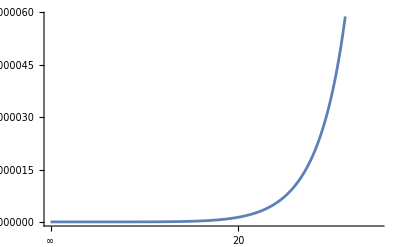

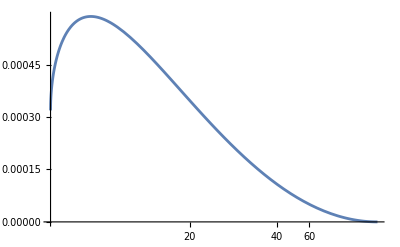

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[q2, (in)]:=(3 l σ)/(32 M^2 b1^6 ω)((l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1 z^2)-(4 l^4)/(9 z^3)-(b1^4 l^2)/(2 z^4)-(2 b1^2 l^4)/(27 z^5)-(l^4 √(-b1^2+z^2))/(4 z^4)-((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)+(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
Subscript[q2, (out)]:=(3 l^3 σ)/(32 M^2 b1^6 ω)((π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z^2)-(4 l^2)/(9 z^3)-b1^4/(2 z^4)-(2 b1^2 l^2)/(27 z^5)+(l^2 √(-b1^2+z^2))/(4 z^4)-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
Plot[Subscript[q2, (in)],{z,b1,∞},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[q2, (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ_1

θ2=  C[B]+∫q2/k^r ⅆr      =  C[B]+∫(2 M q2^θ)/k^r ⅆz

## θ_1_(in)

θ2_(in) = C[B]+∫(2 M q2_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫(3 l σ)/(16 M b1^6 ω)((l^2 π (l^2 (3 π^2-50)-18 b1^3 π))/(144 b1 z √(-b1^2+z^2))+l^4/(4 z^3)+(4 l^4)/(9 z^2 √(-b1^2+z^2))+(b1^4 l^2)/(2 z^3 √(-b1^2+z^2))+(2 b1^2 l^4)/(27 z^4 √(-b1^2+z^2))+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2))-(l^2 (2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2))-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[((3 l σ)/(16 M b1^6 ω)((l^2 π (l^2 (3 π^2-50)-18 b1^3 π))/(144 b1 z √(-b1^2+z^2))+l^4/(4 z^3)+(4 l^4)/(9 z^2 √(-b1^2+z^2))+(b1^4 l^2)/(2 z^3 √(-b1^2+z^2))+(2 b1^2 l^4)/(27 z^4 √(-b1^2+z^2))+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2))-(l^2 (2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2))-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2))))-((2 M Subscript[q2, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q2, (in)]->(3 l σ)/(32 M^2 b1^6 ω)((l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1 z^2)-(4 l^4)/(9 z^3)-(b1^4 l^2)/(2 z^4)-(2 b1^2 l^4)/(27 z^5)-(l^4 √(-b1^2+z^2))/(4 z^4)-((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)+(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l σ)/(16 M b1^6 ω)(FullSimplify[Integrate[(l^2 π (l^2 (3 π^2-50)-18 b1^3 π))/(144 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^4/(4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(4 l^4)/(9 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(b1^4 l^2)/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 b1^2 l^4)/(27 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 (2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l σ (-l^4/(8 z^2)+(4 l^4 √(-b1^2+z^2))/(9 b1^2 z)+(2 l^4 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^2 z^3)+(l^2 π (-18 b1^3 π+l^2 (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)+(b1 l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2))

From the boundary condition  θ2_(in)[∞] = 0

```mathematica
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
```

```mathematica
FullSimplify[((3 l σ)/(16 b1^6 M ω) (-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)))-(1/(16 b1^6 M ω)3 l σ (-l^4/(8 z^2)+(4 l^4 √(-b1^2+z^2))/(9 b1^2 z)+(2 l^4 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^2 z^3)+(l^2 π (-18 b1^3 π+l^2 (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)+(b1 l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2))),Assumptions->{M>0,z>0}]
```

0

#### Boundary Behaviour of θ2_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ2, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ2atb1, (in)]=FullSimplify[Limit[Subscript[θ2, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (216 b1^3 π (-6+π^2)+l^2 (-6416+900 π^2-27 π^4)) σ)/(55296 b1^8 M ω)

## θ_1_(out)

θ2_(out) = C[B]+∫(2 M q2_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫(3 l^3 σ)/(16M b1^6 ω)(l^2/(4 z^3)+(π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z √(-b1^2+z^2))-(4 l^2)/(9 z^2 √(-b1^2+z^2))-b1^4/(2 z^3 √(-b1^2+z^2))-(2 b1^2 l^2)/(27 z^4 √(-b1^2+z^2))-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2)))ⅆz

```mathematica
FullSimplify[((3 l^3 σ)/(16M b1^6 ω)(l^2/(4 z^3)+(π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z √(-b1^2+z^2))-(4 l^2)/(9 z^2 √(-b1^2+z^2))-b1^4/(2 z^3 √(-b1^2+z^2))-(2 b1^2 l^2)/(27 z^4 √(-b1^2+z^2))-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2))))-((2 M Subscript[q2, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q2, (out)]->(3 l^3 σ)/(32 M^2 b1^6 ω)((π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z^2)-(4 l^2)/(9 z^3)-b1^4/(2 z^4)-(2 b1^2 l^2)/(27 z^5)+(l^2 √(-b1^2+z^2))/(4 z^4)-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))},Assumptions->{M>0,z>0}]
```

0

#### Integration

```mathematica
(3 l^3 σ)/(16M b1^6 ω)(FullSimplify[Integrate[l^2/(4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(4 l^2)/(9 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-b1^4/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 b1^2 l^2)/(27 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

(3 l^3 σ (-l^2/(8 z^2)-(4 l^2 √(-b1^2+z^2))/(9 b1^2 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^2 z^3)+(π (18 b1^3 π+l^2 (50-3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)-(b1 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2)))/(16 b1^6 M ω)

From the boundary condition  θ2_(out)[b1] = θ2_(in)[b1]

```mathematica
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
```

```mathematica
FullSimplify[((3 l^3 σ)/(16 b1^6 M ω) (-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)))-(1/(16 b1^6 M ω)3 l^3 σ (-l^2/(8 z^2)-(4 l^2 √(-b1^2+z^2))/(9 b1^2 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(81 b1^2 z^3)+(π (18 b1^3 π+l^2 (50-3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)-(b1 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2))),Assumptions->{M>0,z>0}]
```

0

#### Boundary Behaviour of θ2_(out)

z → b1

```mathematica
Subscript[θ2atb1, (out)]=FullSimplify[Limit[Subscript[θ2, (out)] ,z->b1],Assumptions->{z>0,b1>0}]
```

(l^3 (216 b1^3 π (-6+π^2)+l^2 (-6416+900 π^2-27 π^4)) σ)/(55296 b1^8 M ω)

```mathematica
Subscript[θ2atb1, (out)]-Subscript[θ2atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ2, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^3 (54 b1^3 π (-3+2 π^2)+l^2 (-640+225 π^2-27 π^4)) σ)/(3456 b1^8 M ω)

## Verification of θ_1

### Setting up Numerics

Let H =h_(, r)
H=8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)
⇒h=∫Hⅆz 
H_(in)=8 M^3(z^2(kϕz)^2 θ1_(in))/(krz_(in))
q2_(in)^θ    =-1/(4 M^2 z^2)(∫8 M^3(z^2(k^ϕ)^2 θ1_(in))/(k_(in)^r)ⅆz)   =-1/(4 M^2 z^2)( ∫8 M^3(z^2(kϕz)^2 θ1_(in))/(krz_(in))ⅆz)
θ2_(in) =∫(2 M q_(in)^θ)/(k_(in)^r)ⅆz

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
```

### θ2_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ2, (in)],z->U]]
intHzin[Z_?NumericQ]:=intHzin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intHzin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intHzin]
```

analytic==0.000552331

Numeric==0.000578987

### θ2_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ2, (out)],z->U]]
intHzin[Z_?NumericQ]:=intHzin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intHzin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intHzout[Z_?NumericQ]:=intHzout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ1, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ1, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intHzout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intHzin,θIn,intHzout]
```

analytic==0.00922853

Numeric==0.0095415

### Comparison with Danny’s

```mathematica
M:=1
rg:=2M
σ:=1
sig:=σ
ω:=1
om:=ω
b1:=10
l:=b1
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
U:=b1
θ2inRama==N[(l^3 (216 b1^3 π (-6+π^2)+l^2 (-6416+900 π^2-27 π^4)) σ)/(55296 b1^8 M ω)]
θ2inDanny==N[(π (-6+π^2) sig)/(128 b1^2 om rg)]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,sig,om,rg,z]
```

θ2inRama==0.000471917

θ2inDanny==0.000474872

## Plots of θ_1

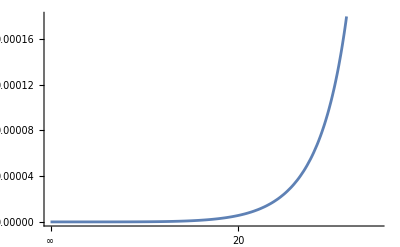

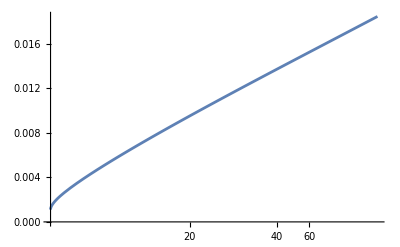

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Plot[Subscript[θ2, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[θ2, (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## q_2^θ

q3^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ2)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g3)

k^ϕ:=l/(2M z^2)


θ2_(in) :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))


θ2_(out) :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))


kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## Ingoing

q3_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ2_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g3_(in))

### g3_(in)

g3_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ2_(in))/(k_(in)^r)ⅆz
g3_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2 ⅆz((-3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)))ⅆz

g3_(in)=∫(3 l^5 σ)/(32 b1^8 ω)((b1^3 π (-6+π^2))/(12z √(-b1^2+z^2))+(l^2 (900 π^2-5120-27 π^4))/(2592z √(-b1^2+z^2))-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2))+((8 b1^2 l^2+81 b1^4 z+160 l^2 z^2)√(-b1^2+z^2))/(81 z^4 √(-b1^2+z^2))+((-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(36z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(36z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(3z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(6z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ2, (in)]:=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^5 σ)/(32 b1^8 ω)((b1^3 π (-6+π^2))/(12z √(-b1^2+z^2))+(l^2 (900 π^2-5120-27 π^4))/(2592z √(-b1^2+z^2))-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2))+((8 b1^2 l^2+81 b1^4 z+160 l^2 z^2)√(-b1^2+z^2))/(81 z^4 √(-b1^2+z^2))+((-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(36z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(36z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(3z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(6z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ2, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^5 σ)/(32 b1^8 ω)(FullSimplify[Integrate[(b1^3 π (-6+π^2))/(12z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[(l^2 (900 π^2-5120-27 π^4))/(2592z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(b1^2 l^2)/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((8 b1^2 l^2+81 b1^4 z+160 l^2 z^2)√(-b1^2+z^2))/(81 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(36z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(36z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(3z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(6z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^5 σ (-(16 b1^2 l^2+243 b1^4 z+960 l^2 z^2)/(486 z^3)+1/12 b1^2 π (-6+π^2) ArcCot[b1/(√(-b1^2+z^2))]-(l^2 (5120-900 π^2+27 π^4) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1 z^2))

From the boundary condition g_(in)[∞] = 0

```mathematica
FullSimplify[((3 l^5 σ)/(32 b1^8 ω) (-(160 l^2)/(81 z)-b1^4/(2 z^2)-(8 b1^2 l^2)/(243 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1)))-(1/(32 b1^8 ω)3 l^5 σ (-(16 b1^2 l^2+243 b1^4 z+960 l^2 z^2)/(486 z^3)+1/12 b1^2 π (-6+π^2) ArcCot[b1/(√(-b1^2+z^2))]-(l^2 (5120-900 π^2+27 π^4) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 b1 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

```mathematica
Subscript[g3, (in)]:=(3 l^5 σ)/(32 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1)-(160 l^2)/(81 z)-b1^4/(2 z^2)-(8 b1^2 l^2)/(243 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1))
```

#### Boundary Behaviour of g3_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g3, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g3atb1, (in)]=FullSimplify[Limit[Subscript[g3, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^5 (-810 b1^3 (48-12 π^2+π^4)+l^2 (-156160+86520 π-4500 π^3+81 π^5)) σ)/(829440 b1^9 ω)

### q3_(in)^θ

q3_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g3_(in)) =   (g3_(in))/(4 M^2 z^2)    ,since  g3_(in)[∞] = 0

```mathematica
Subscript[q3, (in)]:=(3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2))
```

```mathematica
FullSimplify[Subscript[q3, (in)]-(Subscript[g3, (in)]/(4 M^2 z^2))/.{Subscript[g3, (in)]->(3 l^5 σ)/(32 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1)-(160 l^2)/(81 z)-b1^4/(2 z^2)-(8 b1^2 l^2)/(243 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q3, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q3atb1, (in)]=FullSimplify[Limit[Subscript[q3, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^5 (-810 b1^3 (48-12 π^2+π^4)+l^2 (-156160+86520 π-4500 π^3+81 π^5)) σ)/(3317760 b1^11 M^2 ω)

## Outgoing

q3_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ2_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g3_(out))

### g3_(out)

g3_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ2_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2)))ⅆz

g3_(out)=∫(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))ⅆz

```mathematica
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^5 σ)/(8 b1^6 ω) ((40 l^2)/(81 b1^2 z^2)+b1^2/(4 z^3)+(2 l^2)/(81 z^4)+(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2 z √(-b1^2+z^2))+l^2/(8 z^3 √(-b1^2+z^2))+((l^2 π (3 π^2-50)+18 b1^3 (2-π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2 z √(-b1^2+z^2))+((π l^2-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ2, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^5 σ)/(8 b1^6 ω) (FullSimplify[Integrate[(40 l^2)/(81 b1^2 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+b1^2/(4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2)/(81 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (3 π^2-50)+18 b1^3 (2-π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((π l^2-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^5 σ (-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+((-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16 b1^3 z^2))

g3_(out)=(3 l^5 σ)/(8 b1^6 ω)(-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3))

```mathematica
FullSimplify[(3 l^5 σ)/(8 b1^6 ω)(-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3))-(1/(8 b1^6 ω)3 l^5 σ (-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+((-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16 b1^3 z^2))),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   h_(out)[b1]=h_(out)[b1]

```mathematica
Subscript[g3, (out)]:=(3 l^5 σ)/(8 b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3)-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3))
```

#### Boundary Behaviour of g3_(out)

z → b1

```mathematica
Subscript[g3atb1, (out)]=FullSimplify[Limit[Subscript[g3, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g3atb1, (in)]
```

(l^5 (-810 b1^3 (48-12 π^2+π^4)+l^2 (-156160+86520 π-4500 π^3+81 π^5)) σ)/(829440 b1^9 ω)

(l^5 (-810 b1^3 (48-12 π^2+π^4)+l^2 (-156160+86520 π-4500 π^3+81 π^5)) σ)/(829440 b1^9 ω)

```mathematica
FullSimplify[Subscript[g3atb1, (out)]-Subscript[g3atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g3, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^5 π (-270 b1^3 π (-3+π^2)+l^2 (3605-750 π^2+54 π^4)) σ)/(17280 b1^9 ω)

### q3_(out)^θ

q3_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g3_(out)) =   (g3_(out))/(4 M^2 z^2)    ,since  g3_(out)[b1] = g3_(in)[b1]

```mathematica
Subscript[q3, (out)]:= (3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2))
```

```mathematica
FullSimplify[Subscript[q3, (out)]-(Subscript[g3, (out)]/(4 M^2 z^2))/.{Subscript[g3, (out)]->(3 l^5 σ)/(8 b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3)-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q3atb1, (out)]=FullSimplify[Limit[Subscript[q3, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^5 (-810 b1^3 (48-12 π^2+π^4)+l^2 (-156160+86520 π-4500 π^3+81 π^5)) σ)/(3317760 b1^11 M^2 ω)

```mathematica
Subscript[q3atb1, (out)]-Subscript[q3atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q3, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g3

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[g3, (in)]:=(3 l^5 σ)/(32 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1)-(160 l^2)/(81 z)-b1^4/(2 z^2)-(8 b1^2 l^2)/(243 z^3)-(l^2 √(-b1^2+z^2))/(4 z^2)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1))
Subscript[g3, (out)]:=(3 l^5 σ)/(8 b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3)-(2 l^2)/(243 z^3)-b1^2/(8 z^2)-(40 l^2)/(81 b1^2 z)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3))
```

### g3_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g3, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-0.0034121

Numeric==-0.00350421+2.28228×10^-20 ⅈ

### g3_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g3, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==-0.134017

Numeric==-0.135282+3.11816×10^-19 ⅈ

## Verification of q3^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[q3, (in)]:=(3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2))
Subscript[q3, (out)]:= (3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2))
```

### (q3^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q3, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-8.53026×10^-6

Numeric==-8.76054×10^-6

### (q3^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q3, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ2, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.

## θ_2

θ3=  C[B]+∫q3/k^r ⅆr      =  C[B]+∫(2 M q3^θ)/k^r ⅆz
q3_(in):=(3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2))
q3_(out):= (3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ3_(in)

θ3_(in) = C[B]+∫(2 M q3_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2)))ⅆz

```mathematica
FullSimplify[((3 l^5 σ)/(64M b1^8 ω) (l^2/(4 z^3)+(π (270 b1^3 π (π^2-12)+l^2 (1500 π^2-28840-27 π^4)))/(25920 b1 z √(-b1^2+z^2))+(160 l^2)/(81 z^2 √(-b1^2+z^2))+b1^4/(2 z^3 √(-b1^2+z^2))+(8 b1^2 l^2)/(243 z^4 √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z √(-b1^2+z^2))-((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z √(-b1^2+z^2))-((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z √(-b1^2+z^2))-((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z √(-b1^2+z^2))))-((2 M Subscript[q3, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q3, (in)]->(3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2))},Assumptions->{M>0,z>0}]
```

0

θ3_(in) =C[B]+∫(3 l^5 σ)/(64M b1^8 ω) (l^2/(4 z^3)+(π (270 b1^3 π (π^2-12)+l^2 (1500 π^2-28840-27 π^4)))/(25920 b1 z √(-b1^2+z^2))+(160 l^2)/(81 z^2 √(-b1^2+z^2))+b1^4/(2 z^3 √(-b1^2+z^2))+(8 b1^2 l^2)/(243 z^4 √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z √(-b1^2+z^2))-((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z √(-b1^2+z^2))-((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z √(-b1^2+z^2))-((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^5 σ)/(64M b1^8 ω) (FullSimplify[Integrate[l^2/(4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (270 b1^3 π (π^2-12)+l^2 (1500 π^2-28840-27 π^4)))/(25920 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(160 l^2)/(81 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+b1^4/(2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 b1^2 l^2)/(243 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^5 σ (-l^2/(8 z^2)+(160 l^2 √(-b1^2+z^2))/(81 b1^2 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(729 b1^2 z^3)+(π (270 b1^3 π (-12+π^2)+l^2 (-28840+1500 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2)+(b1 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2))

```mathematica
FullSimplify[((3 l^5 σ)/(64 b1^8 M ω)(-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2)))-(1/(64 b1^8 M ω)3 l^5 σ (-l^2/(8 z^2)+(160 l^2 √(-b1^2+z^2))/(81 b1^2 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(729 b1^2 z^3)+(π (270 b1^3 π (-12+π^2)+l^2 (-28840+1500 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2)+(b1 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4 z^2))),Assumptions->{M>0,z>0}]
```

0

θ3_(in) =(3 l^5 σ)/(64 b1^8 M ω)(-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))

0

From the boundary condition  θ3_(in)[∞] = 0

```mathematica
Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
```

#### Boundary Behaviour of θ3_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ3, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ3atb1, (in)]=FullSimplify[Limit[Subscript[θ3, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^5 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1980320+9 π^2 (28840-750 π^2+9 π^4))) σ)/(19906560 b1^10 M ω)

## θ3_(out)

θ3_(out) = C[B]+∫(2 M q3_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2)))ⅆz

```mathematica
FullSimplify[((3 l^5 σ)/(16 M b1^6 ω)(l^2/(16 b1^2 z^3)+(π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z √(-b1^2+z^2))-(40 l^2)/(81 b1^2 z^2 √(-b1^2+z^2))-b1^2/(8 z^3 √(-b1^2+z^2))-(2 l^2)/(243 z^4 √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z √(-b1^2+z^2))))-((2 M Subscript[q3, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q3, (out)]->(3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2))},Assumptions->{M>0,z>0}]
```

0

θ3_(out) =C[B]+∫(3 l^5 σ)/(16 M b1^6 ω)(l^2/(16 b1^2 z^3)+(π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z √(-b1^2+z^2))-(40 l^2)/(81 b1^2 z^2 √(-b1^2+z^2))-b1^2/(8 z^3 √(-b1^2+z^2))-(2 l^2)/(243 z^4 √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^5 σ)/(16 M b1^6 ω)(FullSimplify[Integrate[l^2/(16 b1^2 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(40 l^2)/(81 b1^2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-b1^2/(8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(243 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^5 σ (-l^2/(32 b1^2 z^2)-(40 l^2 √(-b1^2+z^2))/(81 b1^4 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(729 b1^4 z^3)+(π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4)+1/16 (-(√(-b1^2+z^2))/z^2-ArcCot[b1/(√(-b1^2+z^2))]/b1))

```mathematica
FullSimplify[((3 l^5 σ)/(16 b1^6 M ω) (-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4)))-(1/(16 b1^6 M ω)3 l^5 σ (-l^2/(32 b1^2 z^2)-(40 l^2 √(-b1^2+z^2))/(81 b1^4 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(729 b1^4 z^3)+(π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4)+1/16 (-(√(-b1^2+z^2))/z^2-ArcCot[b1/(√(-b1^2+z^2))]/b1))),Assumptions->{M>0,z>0}]
```

0

θ3_(out) =(3 l^5 σ)/(16 b1^6 M ω) (-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))

From the boundary condition  θ3_(out)[b1] = θ3_(in)[b1]

```mathematica
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))
```

#### Boundary Behaviour of θ3_(out)

z → b1

```mathematica
Subscript[θ3atb1, (out)]=FullSimplify[Limit[Subscript[θ3, (out)] ,z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ3atb1, (in)]
```

(l^5 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1980320+9 π^2 (28840-750 π^2+9 π^4))) σ)/(19906560 b1^10 M ω)

(l^5 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1980320+9 π^2 (28840-750 π^2+9 π^4))) σ)/(19906560 b1^10 M ω)

```mathematica
Subscript[θ3atb1, (out)]-Subscript[θ3atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ3, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^5 (-486 b1^3 π (15+2 π^2 (-5+π^2))+l^2 (-116480+9 π^2 (3605-375 π^2+18 π^4))) σ)/(622080 b1^10 M ω)

## Verification of θ3

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2

Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))


Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))
```

### θ3_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ3, (in)],z->U]]
intg3zin[Z_?NumericQ]:=intg3zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg3zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg3zin]
```

analytic==-0.0000398284

Numeric==-0.0000419261+2.50443×10^-22 ⅈ

### θ3_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ3, (out)],z->U]]
intg3zin[Z_?NumericQ]:=intg3zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg3zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg3zout[Z_?NumericQ]:=intg3zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ2, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg3zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg3zin,θIn,intg3zout]
```

analytic==-0.00347781

Numeric==-0.00356293+1.44361×10^-20 ⅈ

## q_3^θ

q4^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ3)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g4)

k^ϕ:=l/(2M z^2)
kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z


θ3_(in) :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
θ3_(out) :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))

## Ingoing

q4_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ3_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g4_(in))

### g4_(in)

g4_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ3_(in))/(k_(in)^r)ⅆz
g4_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2)))ⅆz

g4_(in)=∫(3 l^7 σ)/(32 b1^8 ω)((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2 z √(-b1^2+z^2))-l^2/(8 z^3 √(-b1^2+z^2))+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z^2 √(-b1^2+z^2))+(b1^2 √(-b1^2+z^2))/(4 z^3 √(-b1^2+z^2))+(8 l^2 √(-b1^2+z^2))/(729 z^4 √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2 z √(-b1^2+z^2))+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[((3 l^7 σ)/(32 b1^8 ω)((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2 z √(-b1^2+z^2))-l^2/(8 z^3 √(-b1^2+z^2))+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z^2 √(-b1^2+z^2))+(b1^2 √(-b1^2+z^2))/(4 z^3 √(-b1^2+z^2))+(8 l^2 √(-b1^2+z^2))/(729 z^4 √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2 z √(-b1^2+z^2))+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2 z √(-b1^2+z^2))))-(-8 M^3(z^2(kϕ)^2 Subscript[θ3, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^7 σ)/(32 b1^8 ω)(FullSimplify[Integrate[(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(b1^2 √(-b1^2+z^2))/(4 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2 √(-b1^2+z^2))/(729 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^7 σ (-(8 l^2)/(2187 z^3)-b1^2/(8 z^2)-(1456 l^2)/(729 b1^2 z)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16 b1^3 z^2))

```mathematica
FullSimplify[((3 l^7 σ)/(32 b1^8 ω) (-(1456 l^2)/(729 b1^2 z)-b1^2/(8 z^2)-(8 l^2)/(2187 z^3)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3)))-(1/(32 b1^8 ω)3 l^7 σ (-(8 l^2)/(2187 z^3)-b1^2/(8 z^2)-(1456 l^2)/(729 b1^2 z)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16 b1^3 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g4, (in)]:=(3 l^7 σ)/(32 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3)-(1456 l^2)/(729 b1^2 z)-b1^2/(8 z^2)-(8 l^2)/(2187 z^3)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3))
```

#### Boundary Behaviour of g4_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g4, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g4atb1, (in)]=FullSimplify[Limit[Subscript[g4, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^7 (3402 b1^3 (-1440+360 π^2-30 π^4+π^6)+l^2 (-78417920+3 π (13454000-605640 π^2+9450 π^4-81 π^6))) σ)/(418037760 b1^11 ω)

### q4_(in)^θ

q4_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g4_(in)) =   (g4_(in))/(4 M^2 z^2)    ,since  g4_(in)[∞] = 0

```mathematica
Subscript[q4, (in)]:=(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))
```

```mathematica
FullSimplify[Subscript[q4, (in)]-(Subscript[g4, (in)]/(4 M^2 z^2))/.{Subscript[g4, (in)]->(3 l^7 σ)/(32 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3)-(1456 l^2)/(729 b1^2 z)-b1^2/(8 z^2)-(8 l^2)/(2187 z^3)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q4, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q4atb1, (in)]=FullSimplify[Limit[Subscript[q4, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^7 (3402 b1^3 (-1440+360 π^2-30 π^4+π^6)+l^2 (-78417920+3 π (13454000-605640 π^2+9450 π^4-81 π^6))) σ)/(1672151040 b1^13 M^2 ω)

## Outgoing

q4_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ3_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g4_(out))

### g4_(out)

g4_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ3_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4)))ⅆz

g4_(out)=∫(3 l^7 σ)/(8 b1^6 ω) ((364 l^2)/(729 b1^4 z^2)+1/(16 z^3)+(2 l^2)/(729 b1^2 z^4)-(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4 z √(-b1^2+z^2))+l^2/(32 b1^2 z^3 √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^7 σ)/(8 b1^6 ω) ((364 l^2)/(729 b1^4 z^2)+1/(16 z^3)+(2 l^2)/(729 b1^2 z^4)-(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4 z √(-b1^2+z^2))+l^2/(32 b1^2 z^3 √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ3, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^7 σ)/(8 b1^6 ω) (FullSimplify[Integrate[(364 l^2)/(729 b1^4 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(16 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2)/(729 b1^2 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(32 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^7 σ (-(2 l^2)/(2187 b1^2 z^3)-1/(32 z^2)-(364 l^2)/(729 b1^4 z)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(64 b1^5 z^2))

g4_(out)=(3 l^7 σ)/(8 b1^6 ω) (-(364 l^2)/(729 b1^4 z)-1/(32 z^2)-(2 l^2)/(2187 b1^2 z^3)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5))

```mathematica
Simplify[((972 b1^3 π (120-20 π^2+π^4)+l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(64 b1^5)]
```

((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)

```mathematica
FullSimplify[((3 l^7 σ)/(8 b1^6 ω) (-(364 l^2)/(729 b1^4 z)-1/(32 z^2)-(2 l^2)/(2187 b1^2 z^3)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5)))-(1/(8 b1^6 ω)3 l^7 σ (-(2 l^2)/(2187 b1^2 z^3)-1/(32 z^2)-(364 l^2)/(729 b1^4 z)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(64 b1^5 z^2))),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   g4_(out)[b1]=g4_(out)[b1]

```mathematica
Subscript[g4, (out)]:=(3 l^7 σ)/(8 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5)-(364 l^2)/(729 b1^4 z)-1/(32 z^2)-(2 l^2)/(2187 b1^2 z^3)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5))
```

#### Boundary Behaviour of g4_(out)

z → b1

```mathematica
Subscript[g4atb1, (out)]=FullSimplify[Limit[Subscript[g4, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g4atb1, (in)]
```

(l^7 (3402 b1^3 (-1440+360 π^2-30 π^4+π^6)+l^2 (-78417920+3 π (13454000-605640 π^2+9450 π^4-81 π^6))) σ)/(418037760 b1^11 ω)

(l^7 (3402 b1^3 (-1440+360 π^2-30 π^4+π^6)+l^2 (-78417920+3 π (13454000-605640 π^2+9450 π^4-81 π^6))) σ)/(418037760 b1^11 ω)

```mathematica
FullSimplify[Subscript[g4atb1, (out)]-Subscript[g4atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g4, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^7 π (1134 b1^3 π (45-15 π^2+2 π^4)+l^2 (840875-151410 π^2+9450 π^4-324 π^6)) σ)/(4354560 b1^11 ω)

### q4_(out)^θ

q4_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g4_(out)) =   (g4_(out))/(4 M^2 z^2)    ,since  g4_(out)[b1] = g4_(in)[b1]

```mathematica
Subscript[q4, (out)]:= (3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))
```

```mathematica
FullSimplify[Subscript[q4, (out)]-(Subscript[g4, (out)]/(4 M^2 z^2))/.{Subscript[g4, (out)]->(3 l^7 σ)/(8 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5)-(364 l^2)/(729 b1^4 z)-1/(32 z^2)-(2 l^2)/(2187 b1^2 z^3)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q4atb1, (out)]=FullSimplify[Limit[Subscript[q4, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^7 (3402 b1^3 (-1440+360 π^2-30 π^4+π^6)+l^2 (-78417920+3 π (13454000-605640 π^2+9450 π^4-81 π^6))) σ)/(1672151040 b1^13 M^2 ω)

```mathematica
Subscript[q4atb1, (out)]-Subscript[q4atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q4, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g4

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))


Subscript[g4, (in)]:=(3 l^7 σ)/(32 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3)-(1456 l^2)/(729 b1^2 z)-b1^2/(8 z^2)-(8 l^2)/(2187 z^3)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3))
Subscript[g4, (out)]:=(3 l^7 σ)/(8 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5)-(364 l^2)/(729 b1^4 z)-1/(32 z^2)-(2 l^2)/(2187 b1^2 z^3)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5))
```

### g4_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g4, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==0.000178636

Numeric==0.000183595

### g4_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g4, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.0335914

Numeric==0.0338076

## Verification of q4^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))


Subscript[q4, (in)]:=(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))
Subscript[q4, (out)]:= (3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))
```

### (q4^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q4, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==4.46591×10^-7

Numeric==4.58988×10^-7-3.06469×10^-24 ⅈ

### (q4^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q4, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ3, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.+0. ⅈ

## θ_3

θ4=  C[B]+∫q4/k^r ⅆr      =  C[B]+∫(2 M q4^θ)/k^r ⅆz
q4_(in):=(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))
q4_(out):= (3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ4_(in)

θ4_(in) = C[B]+∫(2 M q4_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^7 σ)/(64 M b1^8 ω) (l^2/(16 b1^2 z^3)-(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z √(-b1^2+z^2))+(1456 l^2)/(729 b1^2 z^2 √(-b1^2+z^2))+b1^2/(8 z^3 √(-b1^2+z^2))+(8 l^2)/(2187 z^4 √(-b1^2+z^2))-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z √(-b1^2+z^2))-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z √(-b1^2+z^2)))-((2 M Subscript[q4, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q4, (in)]->(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))},Assumptions->{M>0,z>0}]
```

0

θ4_(in) =C[B]+∫(3 l^7 σ)/(64 M b1^8 ω) (l^2/(16 b1^2 z^3)-(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z √(-b1^2+z^2))+(1456 l^2)/(729 b1^2 z^2 √(-b1^2+z^2))+b1^2/(8 z^3 √(-b1^2+z^2))+(8 l^2)/(2187 z^4 √(-b1^2+z^2))-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z √(-b1^2+z^2))-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^7 σ)/(64 M b1^8 ω) (FullSimplify[Integrate[l^2/(16 b1^2 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(1456 l^2)/(729 b1^2 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+b1^2/(8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(2187 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(933120 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^7 σ (-l^2/(32 b1^2 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^4 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^4 z^3)+(π (-1134 b1^3 π (360-30 π^2+π^4)+l^2 (-13454000+605640 π^2-9450 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4)+1/16 ((√(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))]/b1))

```mathematica
FullSimplify[(3 l^7 σ)/(64 b1^8 M ω) (-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))-(1/(64 b1^8 M ω)3 l^7 σ (-l^2/(32 b1^2 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^4 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^4 z^3)+(π (-1134 b1^3 π (360-30 π^2+π^4)+l^2 (-13454000+605640 π^2-9450 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4)+1/16 ((√(-b1^2+z^2))/z^2+ArcCot[b1/(√(-b1^2+z^2))]/b1))),Assumptions->{M>0,z>0}]
```

0

θ4_(in) =(3 l^7 σ)/(64 b1^8 M ω) (-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))

0

From the boundary condition  θ4_(in)[∞] = 0

```mathematica
Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
```

#### Boundary Behaviour of θ4_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ4, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ4atb1, (in)]=FullSimplify[Limit[Subscript[θ4, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^7 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3820552960-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) σ)/(40131624960 b1^12 M ω)

## θ4_(out)

θ4_(out) = C[B]+∫(2 M q4_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2)))ⅆz

```mathematica
FullSimplify[((3 l^7 σ)/(16 M b1^6 ω) (l^2/(64 b1^4 z^3)+(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z √(-b1^2+z^2))-(364 l^2)/(729 b1^4 z^2 √(-b1^2+z^2))-1/(32 z^3 √(-b1^2+z^2))-(2 l^2)/(2187 b1^2 z^4 √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z √(-b1^2+z^2))))-((2 M Subscript[q4, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q4, (out)]->(3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))},Assumptions->{M>0,z>0}]
```

0

θ4_(out) =C[B]+∫(3 l^7 σ)/(16 M b1^6 ω) (l^2/(64 b1^4 z^3)+(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z √(-b1^2+z^2))-(364 l^2)/(729 b1^4 z^2 √(-b1^2+z^2))-1/(32 z^3 √(-b1^2+z^2))-(2 l^2)/(2187 b1^2 z^4 √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^7 σ)/(16 M b1^6 ω) (FullSimplify[Integrate[l^2/(64 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(364 l^2)/(729 b1^4 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(32 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(2187 b1^2 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^7 σ (-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(64 b1^3 z^2))

```mathematica
FullSimplify[((3 l^7 σ)/(16 b1^6 M ω) (-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6)))-(1/(16 b1^6 M ω)3 l^7 σ (-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+(π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(64 b1^3 z^2))),Assumptions->{M>0,z>0}]
```

0

θ4_(out) =(3 l^7 σ)/(16 b1^6 M ω) (-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))

From the boundary condition  θ4_(out)[b1] = θ4_(in)[b1]

```mathematica
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))
```

#### Boundary Behaviour of θ4_(out)

z → b1

```mathematica
Subscript[θ4atb1, (out)]=FullSimplify[Limit[Subscript[θ4, (out)] ,z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ4atb1, (in)]
```

(l^7 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3820552960-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) σ)/(40131624960 b1^12 M ω)

(l^7 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3820552960-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) σ)/(40131624960 b1^12 M ω)

```mathematica
Subscript[θ4atb1, (out)]-Subscript[θ4atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ4, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^7 (1458 b1^3 π (-315+210 π^2-42 π^4+4 π^6)+l^2 (-29388800-9 π^2 (-840875+75705 π^2-3150 π^4+81 π^6))) σ)/(156764160 b1^12 M ω)

## Verification of θ4

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))
Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))
```

### θ4_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ4, (in)],z->U]]
intg4zin[Z_?NumericQ]:=intg4zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg4zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg4zin]
```

analytic==1.59035×10^-6

Numeric==1.67745×10^-6

### θ4_(out)

```mathematica
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ4, (out)],z->U]]
intg4zin[Z_?NumericQ]:=intg4zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg4zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg4zout[Z_?NumericQ]:=intg4zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ3, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg4zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg4zin,θIn,intg4zout]
```

analytic==0.0000378509

Numeric==0.000037975

## q_4^θ

q5^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ4)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g5)

k^ϕ:=l/(2M z^2)
kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z


θ4_(in) :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
θ4_(out) :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))

## Ingoing

q5_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ4_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g5_(in))

### g5_(in)

g5_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ4_(in))/(k_(in)^r)ⅆz
g5_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4)))ⅆz

g5_(in)=∫(3 l^9 σ)/(32 b1^8 ω) ((13120 l^2)/(6561 b1^4 z^2)+1/(16 z^3)+(8 l^2)/(6561 b1^2 z^4)+(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4 z √(-b1^2+z^2))-l^2/(32 b1^2 z^3 √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[((3 l^9 σ)/(32 b1^8 ω) ((13120 l^2)/(6561 b1^4 z^2)+1/(16 z^3)+(8 l^2)/(6561 b1^2 z^4)+(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4 z √(-b1^2+z^2))-l^2/(32 b1^2 z^3 √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4 z √(-b1^2+z^2))))-(-8 M^3(z^2(kϕ)^2 Subscript[θ4, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^9 σ)/(32 b1^8 ω) (FullSimplify[Integrate[(13120 l^2)/(6561 b1^4 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(16 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(6561 b1^2 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(32 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^9 σ (-(8 l^2)/(19683 b1^2 z^3)-1/(32 z^2)-(13120 l^2)/(6561 b1^4 z)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(64 b1^5 z^2))

```mathematica
FullSimplify[((3 l^9 σ)/(32 b1^8 ω) (-(13120 l^2)/(6561 b1^4 z)-1/(32 z^2)-(8 l^2)/(19683 b1^2 z^3)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5)))-(1/(32 b1^8 ω)3 l^9 σ (-(8 l^2)/(19683 b1^2 z^3)-1/(32 z^2)-(13120 l^2)/(6561 b1^4 z)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(64 b1^5 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g5, (in)]:=(3 l^9 σ)/(32 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5)-(13120 l^2)/(6561 b1^4 z)-1/(32 z^2)-(8 l^2)/(19683 b1^2 z^3)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5))
```

#### Boundary Behaviour of g5_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g5, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g5atb1, (in)]=FullSimplify[Limit[Subscript[g5, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^9 (85120 l^2 (-265216+133617 π)-9 (486 b1^3 (80640-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π^3 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) σ)/(120394874880 b1^13 ω)

### q5_(in)^θ

q5_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g5_(in)) =   (g5_(in))/(4 M^2 z^2)    ,since  g5_(in)[∞] = 0

```mathematica
Subscript[q5, (in)]:=(3 l^9 σ)/(128 M^2 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z^2)-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))
```

```mathematica
FullSimplify[Subscript[q5, (in)]-(Subscript[g5, (in)]/(4 M^2 z^2))/.{Subscript[g5, (in)]->(3 l^9 σ)/(32 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5)-(13120 l^2)/(6561 b1^4 z)-1/(32 z^2)-(8 l^2)/(19683 b1^2 z^3)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q5, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q5atb1, (in)]=FullSimplify[Limit[Subscript[q5, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^9 (85120 l^2 (-265216+133617 π)-9 (486 b1^3 (80640-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π^3 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) σ)/(481579499520 b1^15 M^2 ω)

## Outgoing

q5_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ4_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g5_(out))

### g5_(out)

g5_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ4_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6)))ⅆz

g5_(out)=∫(3 l^9 σ)/(8 b1^6 ω) (-(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6 z √(-b1^2+z^2))+l^2/(128 b1^4 z^3 √(-b1^2+z^2))+(364 l^2 √(-b1^2+z^2))/(729 b1^6 z^2 √(-b1^2+z^2))+(√(-b1^2+z^2))/(64 b1^2 z^3 √(-b1^2+z^2))+(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^4 √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^9 σ)/(8 b1^6 ω) (-(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6 z √(-b1^2+z^2))+l^2/(128 b1^4 z^3 √(-b1^2+z^2))+(364 l^2 √(-b1^2+z^2))/(729 b1^6 z^2 √(-b1^2+z^2))+(√(-b1^2+z^2))/(64 b1^2 z^3 √(-b1^2+z^2))+(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^4 √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ4, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^9 σ)/(8 b1^6 ω) (FullSimplify[Integrate[-(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(128 b1^4 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(364 l^2 √(-b1^2+z^2))/(729 b1^6 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(√(-b1^2+z^2))/(64 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^9 σ (-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(256 b1^7 z^2))

g5_(out)=(3 l^9 σ)/(8 b1^6 ω) (-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7))

```mathematica
FullSimplify[(3 l^9 σ)/(8 b1^6 ω) (-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7))-1/(8 b1^6 ω)3 l^9 σ (-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(256 b1^7 z^2)),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   g5_(out)[b1]=g5_(out)[b1]

```mathematica
Subscript[g5, (out)]:=(3 l^9 σ)/(8 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7)-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7))
```

#### Boundary Behaviour of g5_(out)

z → b1

```mathematica
Subscript[g5atb1, (out)]=FullSimplify[Limit[Subscript[g5, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g5atb1, (in)]
```

(l^9 (85120 l^2 (-265216+133617 π)-9 (486 b1^3 (80640-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π^3 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) σ)/(120394874880 b1^13 ω)

(l^9 (85120 l^2 (-265216+133617 π)-9 (486 b1^3 (80640-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π^3 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) σ)/(120394874880 b1^13 ω)

```mathematica
FullSimplify[Subscript[g5atb1, (out)]-Subscript[g5atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g5, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^9 π (-1458 b1^3 π (-315+105 π^2-14 π^4+π^6)+l^2 (29618435+6 π^2 (-840875+9 π^2 (5047+3 π^2 (-50+π^2))))) σ)/(156764160 b1^13 ω)

### q5_(out)^θ

q5_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g5_(out)) =   (g5_(out))/(4 M^2 z^2)    ,since  g5_(out)[b1] = g5_(in)[b1]

```mathematica
Subscript[q5, (out)]:= (3 l^9 σ)/(32 M^2 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z^2)-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))
```

```mathematica
FullSimplify[Subscript[q5, (out)]-(Subscript[g5, (out)]/(4 M^2 z^2))/.{Subscript[g5, (out)]->(3 l^9 σ)/(8 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7)-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q5atb1, (out)]=FullSimplify[Limit[Subscript[q5, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^9 (85120 l^2 (-265216+133617 π)-9 (486 b1^3 (80640-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π^3 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) σ)/(481579499520 b1^15 M^2 ω)

```mathematica
Subscript[q5atb1, (out)]-Subscript[q5atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q5, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g5

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))


Subscript[g5, (in)]:=(3 l^9 σ)/(32 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5)-(13120 l^2)/(6561 b1^4 z)-1/(32 z^2)-(8 l^2)/(19683 b1^2 z^3)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^2)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5))
Subscript[g5, (out)]:=(3 l^9 σ)/(8 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7)-1/(128 b1^2 z^2)-(364 l^2)/(729 b1^6 z)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7))
```

### g5_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g5, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-5.63507×10^-6

Numeric==-5.79372×10^-6+3.9114×10^-23 ⅈ

### g5_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g5, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==-0.0046606

Numeric==-0.00468263+5.38887×10^-21 ⅈ

## Verification of q5^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))


Subscript[q5, (in)]:=(3 l^9 σ)/(128 M^2 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z^2)-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))
Subscript[q5, (out)]:= (3 l^9 σ)/(32 M^2 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z^2)-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))
```

### (q5^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q5, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-1.40877×10^-8

Numeric==-1.44843×10^-8

### (q5^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q5, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ4, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.

## θ_4

θ5=  C[B]+∫q5/k^r ⅆr      =  C[B]+∫(2 M q5^θ)/k^r ⅆz
q5_(in):=(3 l^9 σ)/(128 M^2 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z^2)-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))
q5_(out):= (3 l^9 σ)/(32 M^2 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z^2)-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ5_(in)

θ5_(in) = C[B]+∫(2 M q5_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^9 σ)/(128 M^2 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z^2)-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^9 σ)/(64M b1^8 ω) (l^2/(64 b1^4 z^3)+(π (1458 b1^3 π (1680 π^2-20160-56 π^4+π^6)+l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z √(-b1^2+z^2))+(13120 l^2)/(6561 b1^4 z^2 √(-b1^2+z^2))+1/(32 z^3 √(-b1^2+z^2))+(8 l^2)/(19683 b1^2 z^4 √(-b1^2+z^2))-((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z √(-b1^2+z^2)))-((2 M Subscript[q5, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q5, (in)]->(3 l^9 σ)/(128 M^2 b1^8 ω) ((π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z^2)-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))},Assumptions->{M>0,z>0}]
```

0

θ5_(in) =C[B]+∫(3 l^9 σ)/(64M b1^8 ω) (l^2/(64 b1^4 z^3)+(π (1458 b1^3 π (1680 π^2-20160-56 π^4+π^6)+l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z √(-b1^2+z^2))+(13120 l^2)/(6561 b1^4 z^2 √(-b1^2+z^2))+1/(32 z^3 √(-b1^2+z^2))+(8 l^2)/(19683 b1^2 z^4 √(-b1^2+z^2))-((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^9 σ)/(64M b1^8 ω) (FullSimplify[Integrate[l^2/(64 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (1458 b1^3 π (1680 π^2-20160-56 π^4+π^6)+l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))))/(3762339840 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(13120 l^2)/(6561 b1^4 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(32 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(19683 b1^2 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(1881169920 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(26127360 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^9 σ (-l^2/(128 b1^4 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^6 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(59049 b1^6 z^3)+(π (1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(64 b1^3 z^2))

```mathematica
FullSimplify[(3 l^9 σ)/(64 b1^8 M ω)(-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))-(1/(64 b1^8 M ω)3 l^9 σ (-l^2/(128 b1^4 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^6 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(59049 b1^6 z^3)+(π (1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(64 b1^3 z^2))),Assumptions->{M>0,z>0}]
```

0

θ5_(in) =(3 l^9 σ)/(64 b1^8 M ω)(-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))

0

From the boundary condition  θ5_(in)[∞] = 0

```mathematica
Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)((14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(677221171200 b1^6)-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
```

#### Boundary Behaviour of θ5_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ5, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ5atb1, (in)]=FullSimplify[Limit[Subscript[θ5, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^9 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1359710195200+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) σ)/(14447384985600 b1^14 M ω)

## θ5_(out)

θ5_(out) = C[B]+∫(2 M q5_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^9 σ)/(32 M^2 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z^2)-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^9 σ)/(16 M b1^6 ω) (l^2/(256 b1^6 z^3)+(π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z √(-b1^2+z^2))-(364 l^2)/(729 b1^6 z^2 √(-b1^2+z^2))-1/(128 b1^2 z^3 √(-b1^2+z^2))-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^4 √(-b1^2+z^2))+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z √(-b1^2+z^2)))-((2 M Subscript[q5, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q5, (out)]->(3 l^9 σ)/(32 M^2 b1^6 ω) ((π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z^2)-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))},Assumptions->{M>0,z>0}]
```

0

θ5_(out) =C[B]+∫(3 l^9 σ)/(16 M b1^6 ω) (l^2/(256 b1^6 z^3)+(π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z √(-b1^2+z^2))-(364 l^2)/(729 b1^6 z^2 √(-b1^2+z^2))-1/(128 b1^2 z^3 √(-b1^2+z^2))-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^4 √(-b1^2+z^2))+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^9 σ)/(16 M b1^6 ω) (FullSimplify[Integrate[l^2/(256 b1^6 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))))/(15049359360 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(364 l^2)/(729 b1^6 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(128 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(7524679680 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(104509440 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^9 σ (-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)+(π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(256 b1^5 z^2))

```mathematica
FullSimplify[(3 l^9 σ)/(16 b1^6 M ω)(-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))-(1/(16 b1^6 M ω)3 l^9 σ (-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)+(π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(256 b1^5 z^2))),Assumptions->{M>0,z>0}]
```

0

θ5_(out) =(3 l^9 σ)/(16 b1^6 M ω)(-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))

From the boundary condition  θ5_(out)[b1] = θ5_(in)[b1]

```mathematica
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(2708884684800 b1^8)-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))
```

#### Boundary Behaviour of θ5_(out)

z → b1

```mathematica
Subscript[θ5atb1, (out)]=FullSimplify[Limit[Subscript[θ5, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ5atb1, (in)]
```

(l^9 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1359710195200+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) σ)/(14447384985600 b1^14 M ω)

(l^9 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1359710195200+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) σ)/(14447384985600 b1^14 M ω)

```mathematica
Subscript[θ5atb1, (out)]-Subscript[θ5atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ5, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^9 (-7290 b1^3 π (2835+2 π^2 (-945+189 π^2-18 π^4+π^6))+l^2 (-5290700800+9 π^2 (148092175+3 π^2 (-4204375+151410 π^2-3375 π^4+54 π^6)))) σ)/(28217548800 b1^14 M ω)

## Verification of θ5

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(1881169920 b1^4)-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(13063680 b1^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) ((11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))/(7524679680 b1^6)-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(52254720 b1^6)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))


Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)((14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(677221171200 b1^6)-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(2708884684800 b1^8)-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))
```

### θ5_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ5, (in)],z->U]]
intg5zin[Z_?NumericQ]:=intg5zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg5zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg5zin]
```

analytic==-4.07×10^-8

Numeric==-4.29772×10^-8+2.81457×10^-25 ⅈ

### θ5_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ5, (out)],z->U]]
intg5zin[Z_?NumericQ]:=intg5zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg5zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg5zout[Z_?NumericQ]:=intg5zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ4, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg5zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg5zin,θIn,intg5zout]
```

analytic==-0.0000694914

Numeric==-0.0000704831+1.73287×10^-22 ⅈ

## q_5^θ

q6^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ5)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g6)

k^ϕ:=l/(2M z^2)
kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z


θ5_(in) :=(3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
θ5_(out) :=(3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))

## Ingoing

q6_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ5_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g6_(in))

### g6_(in)

g6_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ5_(in))/(k_(in)^r)ⅆz
g6_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6)))ⅆz

g6_(in)=∫(3 l^11 σ)/(32 b1^8 ω)((118096 l^2)/(59049 b1^6 z^2)+1/(64 b1^2 z^3)+(8 l^2)/(59049 b1^4 z^4)+1/(677221171200 b1^6 z √(-b1^2+z^2))(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^3 √(-b1^2+z^2))+1/(3762339840 b1^6 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6 z √(-b1^2+z^2))+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^11 σ)/(32 b1^8 ω)((118096 l^2)/(59049 b1^6 z^2)+1/(64 b1^2 z^3)+(8 l^2)/(59049 b1^4 z^4)+1/(677221171200 b1^6 z √(-b1^2+z^2))(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^3 √(-b1^2+z^2))+1/(3762339840 b1^6 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6 z √(-b1^2+z^2))+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ5, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^11 σ)/(32 b1^8 ω)(FullSimplify[Integrate[(118096 l^2)/(59049 b1^6 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(64 b1^2 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(59049 b1^4 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(677221171200 b1^6 z √(-b1^2+z^2))(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(128 b1^4 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(3762339840 b1^6 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(3762339840 b1^6 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^11 σ (-(8 l^2)/(177147 b1^4 z^3)-1/(128 b1^2 z^2)-(118096 l^2)/(59049 b1^6 z)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(256 b1^7 z^2))

```mathematica
FullSimplify[((3 l^11 σ)/(32 b1^8 ω)(-(118096 l^2)/(59049 b1^6 z)-1/(128 b1^2 z^2)-(8 l^2)/(177147 b1^4 z^3)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7)))-(1/(32 b1^8 ω)3 l^11 σ (-(8 l^2)/(177147 b1^4 z^3)-1/(128 b1^2 z^2)-(118096 l^2)/(59049 b1^6 z)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(256 b1^7 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g6, (in)]:=(3 l^11 σ)/(32 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7)-(118096 l^2)/(59049 b1^6 z)-1/(128 b1^2 z^2)-(8 l^2)/(177147 b1^4 z^3)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7))
```

#### Boundary Behaviour of g6_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g6, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g6atb1, (in)]=FullSimplify[Limit[Subscript[g6, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^11 (492800 l^2 (-181399552+90874875 π)+48114 b1^3 (-7257600+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+9 l^2 π^3 (-208513782400-9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))) σ)/(476763704524800 b1^15 ω)

### q6_(in)^θ

q6_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g6_(in)) =   (g6_(in))/(4 M^2 z^2)    ,since  g6_(in)[∞] = 0

```mathematica
Subscript[q6, (in)]:=(3 l^11 σ)/(128 M^2 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z^2)-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))
```

```mathematica
FullSimplify[Subscript[q6, (in)]-(Subscript[g6, (in)]/(4 M^2 z^2))/.{Subscript[g6, (in)]->(3 l^11 σ)/(32 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7)-(118096 l^2)/(59049 b1^6 z)-1/(128 b1^2 z^2)-(8 l^2)/(177147 b1^4 z^3)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q6, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q6atb1, (in)]=FullSimplify[Limit[Subscript[q6, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^11 (492800 l^2 (-181399552+90874875 π)+48114 b1^3 (-7257600+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+9 l^2 π^3 (-208513782400-9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))) σ)/(1907054818099200 b1^17 M^2 ω)

## Outgoing

q6_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ5_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g6_(out))

### g6_(out)

g6_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ5_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8)))ⅆz

g6_(out)=∫(3 l^11 σ)/(8 b1^6 ω)((29524 l^2)/(59049 b1^8 z^2)+1/(256 b1^4 z^3)+(2 l^2)/(59049 b1^6 z^4)+1/(2708884684800 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+l^2/(512 b1^6 z^3 √(-b1^2+z^2))+1/(15049359360 b1^8 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(15049359360 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^11 σ)/(8 b1^6 ω)((29524 l^2)/(59049 b1^8 z^2)+1/(256 b1^4 z^3)+(2 l^2)/(59049 b1^6 z^4)+1/(2708884684800 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+l^2/(512 b1^6 z^3 √(-b1^2+z^2))+1/(15049359360 b1^8 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(15049359360 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ5, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^11 σ)/(8 b1^6 ω)(FullSimplify[Integrate[(29524 l^2)/(59049 b1^8 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(256 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2)/(59049 b1^6 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(2708884684800 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(512 b1^6 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(15049359360 b1^8 z √(-b1^2+z^2))(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(15049359360 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^11 σ (-(2 l^2)/(177147 b1^6 z^3)-1/(512 b1^4 z^2)-(29524 l^2)/(59049 b1^8 z)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(1024 b1^9 z^2))

g6_(out)=(3 l^11 σ)/(8 b1^6 ω) (-(29524 l^2)/(59049 b1^8 z)-1/(512 b1^4 z^2)-(2 l^2)/(177147 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9))

```mathematica
FullSimplify[(3 l^11 σ)/(8 b1^6 ω) (-(29524 l^2)/(59049 b1^8 z)-1/(512 b1^4 z^2)-(2 l^2)/(177147 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9))-(1/(8 b1^6 ω)3 l^11 σ (-(2 l^2)/(177147 b1^6 z^3)-1/(512 b1^4 z^2)-(29524 l^2)/(59049 b1^8 z)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(1024 b1^9 z^2))),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   g6_(out)[b1]=g6_(out)[b1]

```mathematica
Subscript[g6, (out)]:=(3 l^11 σ)/(8 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9)-(29524 l^2)/(59049 b1^8 z)-1/(512 b1^4 z^2)-(2 l^2)/(177147 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9))
```

#### Boundary Behaviour of g6_(out)

z → b1

```mathematica
Subscript[g6atb1, (out)]=FullSimplify[Limit[Subscript[g6, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g6atb1, (in)]
```

(l^11 (492800 l^2 (-181399552+90874875 π)+48114 b1^3 (-7257600+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+9 l^2 π^3 (-208513782400-9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))) σ)/(476763704524800 b1^15 ω)

(l^11 (492800 l^2 (-181399552+90874875 π)+48114 b1^3 (-7257600+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+9 l^2 π^3 (-208513782400-9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))) σ)/(476763704524800 b1^15 ω)

```mathematica
FullSimplify[Subscript[g6atb1, (out)]-Subscript[g6atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g6, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^11 π (16038 b1^3 π (14175-4725 π^2+630 π^4-45 π^6+2 π^8)+l^2 (58311378125-6 π^2 (1629013925+9 π^2 (-9249625+237930 π^2-4125 π^4+54 π^6)))) σ)/(310393036800 b1^15 ω)

### q6_(out)^θ

q6_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g6_(out)) =   (g6_(out))/(4 M^2 z^2)    ,since  g6_(out)[b1] = g6_(in)[b1]

```mathematica
Subscript[q6, (out)]:= (3 l^11 σ)/(32 M^2 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z^2)-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))
```

```mathematica
FullSimplify[Subscript[q6, (out)]-(Subscript[g6, (out)]/(4 M^2 z^2))/.{Subscript[g6, (out)]->(3 l^11 σ)/(8 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9)-(29524 l^2)/(59049 b1^8 z)-1/(512 b1^4 z^2)-(2 l^2)/(177147 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q6atb1, (out)]=FullSimplify[Limit[Subscript[q6, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^11 (492800 l^2 (-181399552+90874875 π)+48114 b1^3 (-7257600+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+9 l^2 π^3 (-208513782400-9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))) σ)/(1907054818099200 b1^17 M^2 ω)

```mathematica
Subscript[q6atb1, (out)]-Subscript[q6atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q6, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g6

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))


Subscript[g6, (in)]:=(3 l^11 σ)/(32 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7)-(118096 l^2)/(59049 b1^6 z)-1/(128 b1^2 z^2)-(8 l^2)/(177147 b1^4 z^3)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^2)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7))
Subscript[g6, (out)]:=(3 l^11 σ)/(8 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9)-(29524 l^2)/(59049 b1^8 z)-1/(512 b1^4 z^2)-(2 l^2)/(177147 b1^6 z^3)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9))
```

### g6_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g6, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==1.19467×10^-7

Numeric==1.22858×10^-7

### g6_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g6, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.000418329

Numeric==0.000419853

## Verification of q6^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))


Subscript[q6, (in)]:=(3 l^11 σ)/(128 M^2 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z^2)-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))
Subscript[q6, (out)]:= (3 l^11 σ)/(32 M^2 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z^2)-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))
```

### (q6^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q6, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==2.98667×10^-10

Numeric==3.07145×10^-10-2.0842×10^-27 ⅈ

### (q6^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q6, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ5, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.+0. ⅈ

## θ_5

θ6=  C[B]+∫q6/k^r ⅆr      =  C[B]+∫(2 M q6^θ)/k^r ⅆz
q6_(in):=(3 l^11 σ)/(128 M^2 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z^2)-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))
q6_(out):= (3 l^11 σ)/(32 M^2 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z^2)-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ6_(in)

θ6_(in) = C[B]+∫(2 M q6_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^11 σ)/(128 M^2 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z^2)-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+1/(677221171200 b1^7 z^2)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^11 σ)/(64 M b1^8 ω)(l^2/(256 b1^6 z^3)+(π (16038 b1^3 π (-1814400+151200 π^2-5040 π^4+90 π^6-π^8)+l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z √(-b1^2+z^2))+(118096 l^2)/(59049 b1^6 z^2 √(-b1^2+z^2))+1/(128 b1^2 z^3 √(-b1^2+z^2))+(8 l^2)/(177147 b1^4 z^4 √(-b1^2+z^2))-1/(677221171200 b1^7 z √(-b1^2+z^2))(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z √(-b1^2+z^2))-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z √(-b1^2+z^2)))-((2 M Subscript[q6, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q6, (in)]->(3 l^11 σ)/(128 M^2 b1^8 ω)((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z^2)-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(677221171200 b1^7 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z^2)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))},Assumptions->{M>0,z>0}]
```

0

θ6_(in) =C[B]+∫(3 l^11 σ)/(64 M b1^8 ω)(l^2/(256 b1^6 z^3)+(π (16038 b1^3 π (-1814400+151200 π^2-5040 π^4+90 π^6-π^8)+l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z √(-b1^2+z^2))+(118096 l^2)/(59049 b1^6 z^2 √(-b1^2+z^2))+1/(128 b1^2 z^3 √(-b1^2+z^2))+(8 l^2)/(177147 b1^4 z^4 √(-b1^2+z^2))-1/(677221171200 b1^7 z √(-b1^2+z^2))(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z √(-b1^2+z^2))-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^11 σ)/(64 M b1^8 ω)(FullSimplify[Integrate[l^2/(256 b1^6 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (16038 b1^3 π (-1814400+151200 π^2-5040 π^4+90 π^6-π^8)+l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))))/(14898865766400 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(118096 l^2)/(59049 b1^6 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(128 b1^2 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(177147 b1^4 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(677221171200 b1^7 z √(-b1^2+z^2))(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7524679680 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(11287019520 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(313528320 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(111974400 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^11 σ (-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)+(π (-16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(14898865766400 b1^8)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(256 b1^5 z^2))

```mathematica
FullSimplify[(3 l^11 σ)/(64 b1^8 M ω)(-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-((l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(14898865766400 b1^8)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))-(1/(64 b1^8 M ω)3 l^11 σ (-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)+(π (-16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))])/(14898865766400 b1^8)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(256 b1^5 z^2))),Assumptions->{M>0,z>0}]
```

0

θ6_(in) =(3 l^11 σ)/(64 b1^8 M ω)(-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))θ6_(in) =

0

From the boundary condition  θ6_(in)[∞] = 0

```mathematica
Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-((l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(14898865766400 b1^8)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
```

#### Boundary Behaviour of θ6_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ6, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ6atb1, (in)]=FullSimplify[Limit[Subscript[θ6, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

(l^11 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2147527786342400+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) σ)/(22884657817190400 b1^16 M ω)

## θ6_(out)

θ6_(out) = C[B]+∫(2 M q6_(out)^θ)/(k_(out)^r)ⅆz
= C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^11 σ)/(32 M^2 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z^2)-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^11 σ)/(16M b1^6 ω) (l^2/(1024 b1^8 z^3)+(π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z √(-b1^2+z^2))-(29524 l^2)/(59049 b1^8 z^2 √(-b1^2+z^2))-1/(512 b1^4 z^3 √(-b1^2+z^2))-(2 l^2)/(177147 b1^6 z^4 √(-b1^2+z^2))+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z √(-b1^2+z^2))+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z √(-b1^2+z^2)))-((2 M Subscript[q6, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q6, (out)]->(3 l^11 σ)/(32 M^2 b1^6 ω) ((π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z^2)-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))},Assumptions->{M>0,z>0}]
```

0

θ6_(out) =C[B]+∫(3 l^11 σ)/(16M b1^6 ω) (l^2/(1024 b1^8 z^3)+(π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z √(-b1^2+z^2))-(29524 l^2)/(59049 b1^8 z^2 √(-b1^2+z^2))-1/(512 b1^4 z^3 √(-b1^2+z^2))-(2 l^2)/(177147 b1^6 z^4 √(-b1^2+z^2))+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z √(-b1^2+z^2))+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^11 σ)/(16M b1^6 ω) (FullSimplify[Integrate[l^2/(1024 b1^8 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))))/(59595463065600 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(29524 l^2)/(59049 b1^8 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(512 b1^4 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(177147 b1^6 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(2708884684800 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(30098718720 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(45148078080 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1254113280 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^11 σ (-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+(π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))])/(59595463065600 b1^10)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(1024 b1^7 z^2))

```mathematica
FullSimplify[(3 l^11 σ)/(16 b1^6 M ω) (-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+((l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(59595463065600 b1^10)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))-(1/(16 b1^6 M ω)3 l^11 σ (-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+(π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))])/(59595463065600 b1^10)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(1024 b1^7 z^2))),Assumptions->{M>0,z>0}]
```

0

θ6_(out) =(3 l^11 σ)/(16 b1^6 M ω) (-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))

From the boundary condition  θ6_(out)[b1] = θ6_(in)[b1]

```mathematica
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) ((52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))/(4290873340723200 b1^10)-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))
```

#### Boundary Behaviour of θ6_(out)

z → b1

```mathematica
Subscript[θ6atb1, (out)]=FullSimplify[Limit[Subscript[θ6, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ6atb1, (in)]
```

(l^11 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2147527786342400+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) σ)/(22884657817190400 b1^16 M ω)

(l^11 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2147527786342400+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) σ)/(22884657817190400 b1^16 M ω)

```mathematica
Subscript[θ6atb1, (out)]-Subscript[θ6atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ6, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

(l^11 (13122 b1^3 π (-155925+2 π^2 (51975-10395 π^2+990 π^4-55 π^6+2 π^8))+l^2 (-2095149056000-9 π^2 (-58311378125+4887041775 π^2-166493250 π^4+81 π^6 (39655-550 π^2+6 π^4)))) σ)/(11174149324800 b1^16 M ω)

## Verification of θ6

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)((14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(677221171200 b1^6)-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(3762339840 b1^6)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(3762339840 b1^6)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(78382080 b1^6)+((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(22394880 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)((-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))/(2708884684800 b1^8)-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-((l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))])/(15049359360 b1^8)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(15049359360 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(313528320 b1^8)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))


Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-((l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))])/(14898865766400 b1^8)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1354442342400 b1^8)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) ((52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))/(4290873340723200 b1^10)-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5417769369600 b1^10)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))
```

### θ6_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ6, (in)],z->U]]
intg6zin[Z_?NumericQ]:=intg6zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg6zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg6zin]
```

analytic==7.27004×10^-10

Numeric==7.6821×10^-10

### θ6_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ6, (out)],z->U]]
intg6zin[Z_?NumericQ]:=intg6zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg6zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg6zout[Z_?NumericQ]:=intg6zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ5, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg6zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg6zin,θIn,intg6zout]
```

analytic==5.1955×10^-6

Numeric==5.25486×10^-6

## q_6^θ

q7^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ6)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g7)

k^ϕ:=l/(2M z^2)
kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z


θ6_(in) :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
θ6_(out) :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(90296156160 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(180592312320 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))

## Ingoing

q7_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ6_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g7_(in))

### g7_(in)

g7_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ6_(in))/(k_(in)^r)ⅆz
g7_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8)))ⅆz

g7_(in)=∫(3 l^13 σ)/(32 b1^8 ω)((1062880 l^2)/(531441 b1^8 z^2)+1/(256 b1^4 z^3)+(8 l^2)/(531441 b1^6 z^4)+1/(1072718335180800 b1^8 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^3 √(-b1^2+z^2))-1/(14898865766400 b1^8 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^13 σ)/(32 b1^8 ω)((1062880 l^2)/(531441 b1^8 z^2)+1/(256 b1^4 z^3)+(8 l^2)/(531441 b1^6 z^4)+1/(1072718335180800 b1^8 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^3 √(-b1^2+z^2))-1/(14898865766400 b1^8 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ6, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^13 σ)/(32 b1^8 ω)(FullSimplify[Integrate[(1062880 l^2)/(531441 b1^8 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(256 b1^4 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(531441 b1^6 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1072718335180800 b1^8 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(512 b1^6 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(14898865766400 b1^8 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1354442342400 b1^8 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(22574039040 b1^8 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(45148078080 b1^8 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^13 σ (-(8 l^2)/(1594323 b1^6 z^3)-1/(512 b1^4 z^2)-(1062880 l^2)/(531441 b1^8 z)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(1024 b1^9 z^2))

```mathematica
FullSimplify[(3 l^13 σ)/(32 b1^8 ω) (-(1062880 l^2)/(531441 b1^8 z)-1/(512 b1^4 z^2)-(8 l^2)/(1594323 b1^6 z^3)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9))-(1/(32 b1^8 ω)3 l^13 σ (-(8 l^2)/(1594323 b1^6 z^3)-1/(512 b1^4 z^2)-(1062880 l^2)/(531441 b1^8 z)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(1024 b1^9 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g7, (in)]:=(3 l^13 σ)/(32 b1^8 ω) (1/(27890676714700800 b1^9)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z)-1/(512 b1^4 z^2)-(8 l^2)/(1594323 b1^6 z^3)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9))
```

#### Boundary Behaviour of g7_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g7, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g7atb1, (in)]=FullSimplify[Limit[Subscript[g7, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(892501654870425600 b1^17 ω)l^13 (25625600 l^2 (-6530351104+3266761683 π)-9 (18954 b1^3 (958003200-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π^3 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) σ

### q7_(in)^θ

q7_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g7_(in)) =   (g7_(in))/(4 M^2 z^2)    ,since  g7_(in)[∞] = 0

```mathematica
Subscript[q7, (in)]:=(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))
```

```mathematica
FullSimplify[Subscript[q7, (in)]-(Subscript[g7, (in)]/(4 M^2 z^2))/.{Subscript[g7, (in)]->(3 l^13 σ)/(32 b1^8 ω) (1/(27890676714700800 b1^9)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z)-1/(512 b1^4 z^2)-(8 l^2)/(1594323 b1^6 z^3)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q7, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q7atb1, (in)]=FullSimplify[Limit[Subscript[q7, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(3570006619481702400 b1^19 M^2 ω)l^13 (25625600 l^2 (-6530351104+3266761683 π)-9 (18954 b1^3 (958003200-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π^3 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) σ

## Outgoing

q7_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ6_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g7_(out))

### g7_(out)

g7_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ6_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(90296156160 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(180592312320 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10)))ⅆz

g7_(out)=∫(3 l^13 σ)/(8 b1^6 ω) ((265720 l^2)/(531441 b1^10 z^2)+1/(1024 b1^6 z^3)+(2 l^2)/(531441 b1^8 z^4)+1/(4290873340723200 b1^10 z √(-b1^2+z^2))(52488 b1^3 π (39916800-6652800 π^2+332640 π^4-7920 π^6+110 π^8-π^10)-l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))+l^2/(2048 b1^8 z^3 √(-b1^2+z^2))-1/(59595463065600 b1^10 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]-1/(5417769369600 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(90296156160 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(180592312320 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(90296156160 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(180592312320 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^13 σ)/(8 b1^6 ω) ((265720 l^2)/(531441 b1^10 z^2)+1/(1024 b1^6 z^3)+(2 l^2)/(531441 b1^8 z^4)+1/(4290873340723200 b1^10 z √(-b1^2+z^2))(52488 b1^3 π (39916800-6652800 π^2+332640 π^4-7920 π^6+110 π^8-π^10)-l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))+l^2/(2048 b1^8 z^3 √(-b1^2+z^2))-1/(59595463065600 b1^10 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]-1/(5417769369600 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(90296156160 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(180592312320 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ6, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^13 σ)/(8 b1^6 ω) (FullSimplify[Integrate[(265720 l^2)/(531441 b1^10 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1024 b1^6 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2)/(531441 b1^8 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(4290873340723200 b1^10 z √(-b1^2+z^2))(52488 b1^3 π (39916800-6652800 π^2+332640 π^4-7920 π^6+110 π^8-π^10)-l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(2048 b1^8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(59595463065600 b1^10 z √(-b1^2+z^2))(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(5417769369600 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(90296156160 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(180592312320 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^13 σ (-(2 l^2)/(1594323 b1^8 z^3)-1/(2048 b1^6 z^2)-(265720 l^2)/(531441 b1^10 z)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4096 b1^11 z^2))

g7_(out)=(3 l^13 σ)/(8 b1^6 ω) (-(265720 l^2)/(531441 b1^10 z)-1/(2048 b1^6 z^2)-(2 l^2)/(1594323 b1^8 z^3)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11))

```mathematica
FullSimplify[(3 l^13 σ)/(8 b1^6 ω) (-(265720 l^2)/(531441 b1^10 z)-1/(2048 b1^6 z^2)-(2 l^2)/(1594323 b1^8 z^3)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11))-(1/(8 b1^6 ω)3 l^13 σ (-(2 l^2)/(1594323 b1^8 z^3)-1/(2048 b1^6 z^2)-(265720 l^2)/(531441 b1^10 z)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4096 b1^11 z^2))),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   g7_(out)[b1]=g7_(out)[b1]

```mathematica
Subscript[g7, (out)]:=(3 l^13 σ)/(8 b1^6 ω) (1/(111562706858803200 b1^11)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z)-1/(2048 b1^6 z^2)-(2 l^2)/(1594323 b1^8 z^3)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11))
```

#### Boundary Behaviour of g7_(out)

z → b1

```mathematica
Subscript[g7atb1, (out)]=FullSimplify[Limit[Subscript[g7, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g7atb1, (in)]
```

1/(892501654870425600 b1^17 ω)l^13 (25625600 l^2 (-6530351104+3266761683 π)-9 (18954 b1^3 (958003200-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π^3 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) σ

1/(892501654870425600 b1^17 ω)l^13 (25625600 l^2 (-6530351104+3266761683 π)-9 (18954 b1^3 (958003200-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π^3 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) σ

```mathematica
FullSimplify[Subscript[g7atb1, (out)]-Subscript[g7atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g7, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

1/(145263941222400 b1^17 ω)l^13 π (-56862 b1^3 π (-467775+155925 π^2-20790 π^4+1485 π^6-66 π^8+2 π^10)+l^2 (27250237039025+6 π^2 (-758047915625+9 π^2 (4235436205+3 π^2 (-34355750+515515 π^2-5850 π^4+54 π^6))))) σ

### q7_(out)^θ

q7_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g7_(out)) =   (g7_(out))/(4 M^2 z^2)    ,since  g7_(out)[b1] = g7_(in)[b1]

```mathematica
Subscript[q7, (out)]:= (3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))
```

```mathematica
FullSimplify[Subscript[q7, (out)]-(Subscript[g7, (out)]/(4 M^2 z^2))/.{Subscript[g7, (out)]->(3 l^13 σ)/(8 b1^6 ω) (1/(111562706858803200 b1^11)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z)-1/(2048 b1^6 z^2)-(2 l^2)/(1594323 b1^8 z^3)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q7atb1, (out)]=FullSimplify[Limit[Subscript[q7, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(3570006619481702400 b1^19 M^2 ω)l^13 (25625600 l^2 (-6530351104+3266761683 π)-9 (18954 b1^3 (958003200-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π^3 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) σ

```mathematica
Subscript[q7atb1, (out)]-Subscript[q7atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q7, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g7

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))


Subscript[g7, (in)]:=(3 l^13 σ)/(32 b1^8 ω) (1/(27890676714700800 b1^9)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z)-1/(512 b1^4 z^2)-(8 l^2)/(1594323 b1^6 z^3)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^2)+1/(1072718335180800 b1^9)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9))
Subscript[g7, (out)]:=(3 l^13 σ)/(8 b1^6 ω) (1/(111562706858803200 b1^11)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z)-1/(2048 b1^6 z^2)-(2 l^2)/(1594323 b1^8 z^3)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(4290873340723200 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11))
```

### g7_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g7, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-1.82335×10^-9

Numeric==-1.87537×10^-9+1.27528×10^-26 ⅈ

### g7_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g7, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==-0.0000264962

Numeric==-0.000026573+1.87002×10^-23 ⅈ

## Verification of q7^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))


Subscript[q7, (in)]:=(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(90296156160 b1^9 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(225740390400 b1^9 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))
Subscript[q7, (out)]:= (3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(361184624640 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(902961561600 b1^11 z^2)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))
```

### (q7^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q7, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==-4.55838×10^-12

Numeric==-4.68843×10^-12

### (q7^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q7, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ6, (out)])/Subscript[krz, (out)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.

## θ_6

θ7=  C[B]+∫q7/k^r ⅆr      =  C[B]+∫(2 M q7^θ)/k^r ⅆz
q7_(in):=(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(90296156160 b1^9 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(225740390400 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))
q7_(out):= (3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ7_(in)

θ7_(in) = C[B]+∫(2 M q7_(in)^θ)/(k_(in)^r)ⅆz
= C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(90296156160 b1^9 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(225740390400 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^13 σ)/(64 M b1^8 ω) (l^2/(1024 b1^8 z^3)+1/(27890676714700800 b1^9 z √(-b1^2+z^2))π (56862 b1^3 π (19958400 π^2-239500800-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))+(1062880 l^2)/(531441 b1^8 z^2 √(-b1^2+z^2))+1/(512 b1^4 z^3 √(-b1^2+z^2))+(8 l^2)/(1594323 b1^6 z^4 √(-b1^2+z^2))-1/(1072718335180800 b1^9 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]-1/(29797731532800 b1^9 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(4063327027200 b1^9 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(90296156160 b1^9 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(225740390400 b1^9 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z √(-b1^2+z^2)))-((2 M Subscript[q7, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q7, (in)]->(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(90296156160 b1^9 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(225740390400 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))},Assumptions->{M>0,z>0}]
```

0

θ7_(in) =C[B]+∫(3 l^13 σ)/(64 M b1^8 ω) (l^2/(1024 b1^8 z^3)+1/(27890676714700800 b1^9 z √(-b1^2+z^2))π (56862 b1^3 π (19958400 π^2-239500800-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))+(1062880 l^2)/(531441 b1^8 z^2 √(-b1^2+z^2))+1/(512 b1^4 z^3 √(-b1^2+z^2))+(8 l^2)/(1594323 b1^6 z^4 √(-b1^2+z^2))-1/(1072718335180800 b1^9 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]-1/(29797731532800 b1^9 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(4063327027200 b1^9 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(90296156160 b1^9 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(225740390400 b1^9 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z √(-b1^2+z^2))-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^13 σ)/(64 M b1^8 ω) (FullSimplify[Integrate[l^2/(1024 b1^8 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(27890676714700800 b1^9 z √(-b1^2+z^2))π (56862 b1^3 π (19958400 π^2-239500800-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(1062880 l^2)/(531441 b1^8 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(512 b1^4 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(1594323 b1^6 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(1072718335180800 b1^9 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(29797731532800 b1^9 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(4063327027200 b1^9 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(90296156160 b1^9 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(225740390400 b1^9 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(9405849600 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^13 σ (-l^2/(2048 b1^8 z^2)+(1062880 l^2 √(-b1^2+z^2))/(531441 b1^10 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(4782969 b1^10 z^3)+1/(27890676714700800 b1^10)π (56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(451480780800 b1^10)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1354442342400 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(1024 b1^7 z^2))

```mathematica
FullSimplify[(3 l^13 σ)/(64 b1^8 M ω)(-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(451480780800 b1^10)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1354442342400 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))-(1/(64 b1^8 M ω)3 l^13 σ (-l^2/(2048 b1^8 z^2)+(1062880 l^2 √(-b1^2+z^2))/(531441 b1^10 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(4782969 b1^10 z^3)+1/(27890676714700800 b1^10)π (56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(451480780800 b1^10)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1354442342400 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(1024 b1^7 z^2))),Assumptions->{M>0,z>0}]
```

0

θ7_(in) =(3 l^13 σ)/(64 b1^8 M ω)(-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))

From the boundary condition  θ7_(in)[∞] = 0

```mathematica
Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
```

#### Boundary Behaviour of θ7_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ7, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ7atb1, (in)]=FullSimplify[Limit[Subscript[θ7, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(149940278018231500800 b1^18 M ω)l^13 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14060329985871769600+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) σ

## θ7_(out)

θ7_(out) = C[B]+∫(2 M q7_(out)^θ)/(k_(out)^r)ⅆz
=  C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^13 σ)/(16 b1^6 M ω) (l^2/(4096 b1^10 z^3)+1/(111562706858803200 b1^11 z √(-b1^2+z^2))π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^2 √(-b1^2+z^2))-1/(2048 b1^6 z^3 √(-b1^2+z^2))-(2 l^2)/(1594323 b1^8 z^4 √(-b1^2+z^2))+1/(4290873340723200 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z √(-b1^2+z^2)))-((2 M Subscript[q7, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q7, (out)]-> (3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))},Assumptions->{M>0,z>0}]
```

0

θ7_(out) =C[B]+∫(3 l^13 σ)/(16 b1^6 M ω) (l^2/(4096 b1^10 z^3)+1/(111562706858803200 b1^11 z √(-b1^2+z^2))π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^2 √(-b1^2+z^2))-1/(2048 b1^6 z^3 √(-b1^2+z^2))-(2 l^2)/(1594323 b1^8 z^4 √(-b1^2+z^2))+1/(4290873340723200 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z √(-b1^2+z^2))+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z √(-b1^2+z^2))+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^13 σ)/(16 b1^6 M ω) (FullSimplify[Integrate[l^2/(4096 b1^10 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(111562706858803200 b1^11 z √(-b1^2+z^2))π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(265720 l^2)/(531441 b1^10 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(2048 b1^6 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(1594323 b1^8 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(4290873340723200 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(119190926131200 b1^11 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(16253308108800 b1^11 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(361184624640 b1^11 z √(-b1^2+z^2))(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(902961561600 b1^11 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(37623398400 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^13 σ (-l^2/(8192 b1^10 z^2)-(265720 l^2 √(-b1^2+z^2))/(531441 b1^12 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(4782969 b1^12 z^3)+1/(111562706858803200 b1^12)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(4096 b1^9 z^2))

```mathematica
FullSimplify[(3 l^13 σ)/(16 b1^6 M ω)(-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))-(1/(16 b1^6 M ω)3 l^13 σ (-l^2/(8192 b1^10 z^2)-(265720 l^2 √(-b1^2+z^2))/(531441 b1^12 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(4782969 b1^12 z^3)+1/(111562706858803200 b1^12)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(4096 b1^9 z^2))),Assumptions->{M>0,z>0}]
```

0

θ7_(out) =(3 l^13 σ)/(16M b1^6 ω)(-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(1805923123200 b1^12)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(5417769369600 b1^12)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))

From the boundary condition  θ7_(out)[b1] = θ7_(in)[b1]

```mathematica
Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))
```

#### Boundary Behaviour of θ7_(out)

z → b1

```mathematica
Subscript[θ7atb1, (out)]=FullSimplify[Limit[Subscript[θ7, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ7atb1, (in)]
```

1/(149940278018231500800 b1^18 M ω)l^13 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14060329985871769600+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) σ

1/(149940278018231500800 b1^18 M ω)l^13 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14060329985871769600+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) σ

```mathematica
Subscript[θ7atb1, (out)]-Subscript[θ7atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ7, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

1/(36606513188044800 b1^18 M ω)l^13 (-275562 b1^3 π (6081075-4054050 π^2+810810 π^4-77220 π^6+4290 π^8-156 π^10+4 π^12)+l^2 (-6863719787724800+9 π^2 (190751659273175-15919006228125 π^2+9 π^4 (59296106870+9 π^2 (-120245125+2 π^2 (721721-6825 π^2+54 π^4)))))) σ

## Verification of θ7

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22574039040 b1^8)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(45148078080 b1^8)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1567641600 b1^8)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(90296156160 b1^10)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(180592312320 b1^10)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(6270566400 b1^10)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))



Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
 Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))
```

### θ7_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ7, (in)],z->U]]
intg7zin[Z_?NumericQ]:=intg7zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg7zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg7zin]
```

analytic==-9.59342×10^-12

Numeric==-1.01418×10^-11+6.85797×10^-29 ⅈ

### θ7_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ7, (out)],z->U]]
intg7zin[Z_?NumericQ]:=intg7zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg7zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg7zout[Z_?NumericQ]:=intg7zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ6, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg7zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg7zin,θIn,intg7zout]
```

analytic==-2.82669×10^-7

Numeric==-2.85315×10^-7+4.66488×10^-25 ⅈ

## q_7^θ

q8^θ=  1/(4 M^2 z^2)( C[A]-∫8 M^3(z^2(k^ϕ)^2 θ7)/k^r ⅆz)   =   1/(4 M^2 z^2)( C[A]+g8)

k^ϕ:=l/(2M z^2)
kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z


θ7_(in) :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
 θ7_(out) :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))

## Ingoing

q8_(in)^θ=     1/(4 M^2 z^2)( C[A(in)]-∫8 M^3(z^2(k^ϕ)^2 θ7_(in))/(k_(in)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(in)]+g8_(in))

### g8_(in)

g8_(in)=∫-8 M^3(z^2(k^ϕ)^2 θ7_(in))/(k_(in)^r)ⅆz
g8_(in)=∫-8 M^3 1/(-(√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10)))ⅆz

g8_(in)=∫(3 l^15 σ)/(32 b1^8 ω)((9565936 l^2)/(4782969 b1^10 z^2)+1/(1024 b1^6 z^3)+(8 l^2)/(4782969 b1^8 z^4)+1/(7028450532104601600 b1^10 z √(-b1^2+z^2))(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^3 √(-b1^2+z^2))+1/(27890676714700800 b1^10 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
Subscript[kr, (in)]:=-(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^15 σ)/(32 b1^8 ω)((9565936 l^2)/(4782969 b1^10 z^2)+1/(1024 b1^6 z^3)+(8 l^2)/(4782969 b1^8 z^4)+1/(7028450532104601600 b1^10 z √(-b1^2+z^2))(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^3 √(-b1^2+z^2))+1/(27890676714700800 b1^10 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10 z √(-b1^2+z^2))-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10 z √(-b1^2+z^2))+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10 z √(-b1^2+z^2))-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10 z √(-b1^2+z^2))+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ7, (in)])/Subscript[kr, (in)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^15 σ)/(32 b1^8 ω)(FullSimplify[Integrate[(9565936 l^2)/(4782969 b1^10 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1024 b1^6 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(4782969 b1^8 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(7028450532104601600 b1^10 z √(-b1^2+z^2))(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-l^2/(2048 b1^8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(27890676714700800 b1^10 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(2145436670361600 b1^10 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(89393194598400 b1^10 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(16253308108800 b1^10 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(451480780800 b1^10 z √(-b1^2+z^2))(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1354442342400 b1^10 z √(-b1^2+z^2))(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(32 b1^8 ω)3 l^15 σ (-(8 l^2)/(14348907 b1^8 z^3)-1/(2048 b1^6 z^2)-(9565936 l^2)/(4782969 b1^10 z)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4096 b1^11 z^2))

```mathematica
FullSimplify[(3 l^15 σ)/(32 b1^8 ω)(-(9565936 l^2)/(4782969 b1^10 z)-1/(2048 b1^6 z^2)-(8 l^2)/(14348907 b1^8 z^3)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11))-(1/(32 b1^8 ω)3 l^15 σ (-(8 l^2)/(14348907 b1^8 z^3)-1/(2048 b1^6 z^2)-(9565936 l^2)/(4782969 b1^10 z)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11)-(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(4096 b1^11 z^2))),Assumptions->{M>0,b1>0,z>0}]
```

0

From the boundary condition g_(in)[∞] = 0

```mathematica
Subscript[g8, (in)]:=(3 l^15 σ)/(32 b1^8 ω)(1/(70284505321046016000 b1^11)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z)-1/(2048 b1^6 z^2)-(8 l^2)/(14348907 b1^8 z^3)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11))
```

#### Boundary Behaviour of g8_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g8, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[g8atb1, (in)]=FullSimplify[Limit[Subscript[g8, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(2249104170273472512000 b1^19 ω)l^15 (1793792000 l^2 (-235092508672+117560570475 π)+590490 b1^3 (-174356582400+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+9 l^2 π^3 (-976648495478656000+12225796783200000 π^2-27 π^4 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))) σ

### q8_(in)^θ

q8_(in)^θ   =   1/(4 M^2 z^2)( C[A(in)]+g8_(in)) =   (g8_(in))/(4 M^2 z^2)    ,since  g8_(in)[∞] = 0

```mathematica
Subscript[q8, (in)]:=(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11 z^2)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))
```

```mathematica
FullSimplify[Subscript[q8, (in)]-(Subscript[g8, (in)]/(4 M^2 z^2))/.{Subscript[g8, (in)]->(3 l^15 σ)/(32 b1^8 ω)(1/(70284505321046016000 b1^11)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z)-1/(2048 b1^6 z^2)-(8 l^2)/(14348907 b1^8 z^3)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11))}]
```

0

#### Boundary Behaviour

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q8, (in)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[q8atb1, (in)]=FullSimplify[Limit[Subscript[q8, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(8996416681093890048000 b1^21 M^2 ω)l^15 (1793792000 l^2 (-235092508672+117560570475 π)+590490 b1^3 (-174356582400+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+9 l^2 π^3 (-976648495478656000+12225796783200000 π^2-27 π^4 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))) σ

## Outgoing

q8_(out)^θ=   1/(4 M^2 z^2)( C[A(out)]-∫8 M^3(z^2(k^ϕ)^2 θ7_(out))/(k_(out)^r)ⅆz)   =   1/(4 M^2 z^2)( C[A(out)]+g8_(out))

### g8_(out)

g8_(out)=∫-8 M^3(z^2(k^ϕ)^2 θ7_(out))/(k_(out)^r)ⅆz
=∫-8 M^3 1/((√(-b1^2+z^2))/z)z^2(l/(2M z^2))^2((3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12)))ⅆz

g8_(out)=∫(3 l^15 σ)/(8 b1^6 ω)((2391484 l^2)/(4782969 b1^12 z^2)+1/(4096 b1^8 z^3)+(2 l^2)/(4782969 b1^10 z^4)+1/(28113802128418406400 b1^12 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)-l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))+l^2/(8192 b1^10 z^3 √(-b1^2+z^2))+1/(111562706858803200 b1^12 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]-1/(8581746681446400 b1^12 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(357572778393600 b1^12 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(65013232435200 b1^12 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4-((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12 z √(-b1^2+z^2)))ⅆz

```mathematica
Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))
Subscript[kr, (out)]:=(√(-b1^2+z^2))/z
kϕ:=ℓ/r^2
Simplify[(3 l^15 σ)/(8 b1^6 ω)((2391484 l^2)/(4782969 b1^12 z^2)+1/(4096 b1^8 z^3)+(2 l^2)/(4782969 b1^10 z^4)+1/(28113802128418406400 b1^12 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)-l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))+l^2/(8192 b1^10 z^3 √(-b1^2+z^2))+1/(111562706858803200 b1^12 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]-1/(8581746681446400 b1^12 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(357572778393600 b1^12 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(65013232435200 b1^12 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4-((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12 z √(-b1^2+z^2))-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12 z √(-b1^2+z^2))-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12 z √(-b1^2+z^2)))-(-8 M^3(z^2(kϕ)^2 Subscript[θ7, (out)])/Subscript[kr, (out)])/.{ℓ->2M l,r->2M z},Assumptions->{M>0,b1>3M,z>b1}]
```

0

#### Integration

```mathematica
(3 l^15 σ)/(8 b1^6 ω)(FullSimplify[Integrate[(2391484 l^2)/(4782969 b1^12 z^2),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(4096 b1^8 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(2 l^2)/(4782969 b1^10 z^4),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(28113802128418406400 b1^12 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)-l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+l^2/(8192 b1^10 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(111562706858803200 b1^12 z √(-b1^2+z^2))(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(8581746681446400 b1^12 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(357572778393600 b1^12 z √(-b1^2+z^2))(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(65013232435200 b1^12 z √(-b1^2+z^2))(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(8 b1^6 ω)3 l^15 σ (-(2 l^2)/(14348907 b1^10 z^3)-1/(8192 b1^8 z^2)-(2391484 l^2)/(4782969 b1^12 z)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16384 b1^13 z^2))

g8_(out)=(3 l^15 σ)/(8 b1^6 ω) (-(2391484 l^2)/(4782969 b1^12 z)-1/(8192 b1^8 z^2)-(2 l^2)/(14348907 b1^10 z^3)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^2)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13))

```mathematica
FullSimplify[(3 l^15 σ)/(8 b1^6 ω) (-(2391484 l^2)/(4782969 b1^12 z)-1/(8192 b1^8 z^2)-(2 l^2)/(14348907 b1^10 z^3)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^2)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13))-(1/(8 b1^6 ω)3 l^15 σ (-(2 l^2)/(14348907 b1^10 z^3)-1/(8192 b1^8 z^2)-(2391484 l^2)/(4782969 b1^12 z)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13)+(l^2 (b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))]))/(16384 b1^13 z^2))),Assumptions->{M>0,b1>3M,z>b1}]
```

0

From the boundary condition   g8_(out)[b1]=g8_(out)[b1]

```mathematica
Subscript[g8, (out)]:=(3 l^15 σ)/(8 b1^6 ω) (1/(281138021284184064000 b1^13)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z)-1/(8192 b1^8 z^2)-(2 l^2)/(14348907 b1^10 z^3)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^2)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13))
```

#### Boundary Behaviour of g8_(out)

z → b1

```mathematica
Subscript[g8atb1, (out)]=FullSimplify[Limit[Subscript[g8, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[g8atb1, (in)]
```

1/(2249104170273472512000 b1^19 ω)l^15 (1793792000 l^2 (-235092508672+117560570475 π)+590490 b1^3 (-174356582400+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+9 l^2 π^3 (-976648495478656000+12225796783200000 π^2-27 π^4 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))) σ

1/(2249104170273472512000 b1^19 ω)l^15 (1793792000 l^2 (-235092508672+117560570475 π)+590490 b1^3 (-174356582400+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+9 l^2 π^3 (-976648495478656000+12225796783200000 π^2-27 π^4 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))) σ

```mathematica
FullSimplify[Subscript[g8atb1, (out)]-Subscript[g8atb1, (in)],Assumptions->{z>0,b1>0}]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[g8, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

1/(183032565940224000 b1^19 ω)l^15 π (196830 b1^3 π (42567525-14189175 π^2+1891890 π^4-135135 π^6+6006 π^8-182 π^10+4 π^12)+l^2 (34322788221596875-6 π^2 (953758296365875+9 π^2 (-5306335409375+3 π^2 (42354362050-601225625 π^2+5904990 π^4-47250 π^6+324 π^8))))) σ

### q8_(out)^θ

q8_(out)^θ   =   1/(4 M^2 z^2)( C[A(out)]+g8_(out)) =   (g8_(out))/(4 M^2 z^2)    ,since  g8_(out)[b1] = g8_(in)[b1]

```mathematica
Subscript[q8, (out)]:= (3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13 z^2)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))
```

```mathematica
FullSimplify[Subscript[q8, (out)]-(Subscript[g8, (out)]/(4 M^2 z^2))/.{Subscript[g8, (out)]->(3 l^15 σ)/(8 b1^6 ω) (1/(281138021284184064000 b1^13)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z)-1/(8192 b1^8 z^2)-(2 l^2)/(14348907 b1^10 z^3)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^2)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13))}]
```

0

#### Boundary Behaviour

z → b1

```mathematica
Subscript[q8atb1, (out)]=FullSimplify[Limit[Subscript[q8, (out)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(8996416681093890048000 b1^21 M^2 ω)l^15 (1793792000 l^2 (-235092508672+117560570475 π)+590490 b1^3 (-174356582400+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+9 l^2 π^3 (-976648495478656000+12225796783200000 π^2-27 π^4 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))) σ

```mathematica
Subscript[q8atb1, (out)]-Subscript[q8atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[q8, (out)],z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

## Verification of g8

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
 Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))


Subscript[g8, (in)]:=(3 l^15 σ)/(32 b1^8 ω)(1/(70284505321046016000 b1^11)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z)-1/(2048 b1^6 z^2)-(8 l^2)/(14348907 b1^8 z^3)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^2)+1/(7028450532104601600 b1^11)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(357572778393600 b1^11)-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11))
Subscript[g8, (out)]:=(3 l^15 σ)/(8 b1^6 ω) (1/(281138021284184064000 b1^13)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z)-1/(8192 b1^8 z^2)-(2 l^2)/(14348907 b1^10 z^3)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^2)+1/(28113802128418406400 b1^13)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1430291113574400 b1^13)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13))
```

### g8_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[g8, (in)],z->U]]
Numeric==NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==2.10143×10^-11

Numeric==2.16159×10^-11

### g8_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[g8, (out)],z->U]]
Numeric==N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (out)])/Subscript[krz, (out)],{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==1.2527×10^-6

Numeric==1.25566×10^-6

## Verification of q8^θ

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
 Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))


Subscript[q8, (in)]:=(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(81266540544000 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))
Subscript[q8, (out)]:= (3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(325066162176000 b1^13 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))
```

### (q8^θ)_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[q8, (in)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,L,U}]),z-> U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U]
```

analytic==5.25358×10^-14

Numeric==5.40398×10^-14-3.6764×10^-31 ⅈ

### (q8^θ)_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[q8, (out)],z->U]]
Numeric==Limit[-1/(4 M^2 z^2)(NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[8 M^3(z^2(kϕz)^2 Subscript[θ7, (out)])/Subscript[krz, (out)],{z,L,U}]),z->U]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,Lin,L,U]
```

analytic==0.

Numeric==0.+0. ⅈ

## θ_7

θ8=  C[B]+∫q8/k^r ⅆr      =  C[B]+∫(2 M q8^θ)/k^r ⅆz
q8_(in):=(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))
q8_(out):= (3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))

kr_(in):=-(√(-b1^2+z^2))/z
kr_(out):=(√(-b1^2+z^2))/z

## θ8_(in)

θ8_(in) = C[B]+∫(2 M q8_(in)^θ)/(k_(in)^r)ⅆz
=C[B]+∫1/(-(√(-b1^2+z^2))/z)2 M ((3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^15 σ)/(64 M b1^8 ω)(l^2/(4096 b1^10 z^3)+1/(70284505321046016000 b1^11 z √(-b1^2+z^2))π (-196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))+(9565936 l^2)/(4782969 b1^10 z^2 √(-b1^2+z^2))+1/(2048 b1^6 z^3 √(-b1^2+z^2))+(8 l^2)/(14348907 b1^8 z^4 √(-b1^2+z^2))-1/(7028450532104601600 b1^11 z √(-b1^2+z^2))(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]-1/(55781353429401600 b1^11 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(6436310011084800 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(357572778393600 b1^11 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z √(-b1^2+z^2))-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z √(-b1^2+z^2)))-((2 M Subscript[q8, (in)])/k^r)/.{k^-r->-z/(√(-b1^2+z^2)),Subscript[q8, (in)]->(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z^2)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z^2)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))},Assumptions->{M>0,z>0}]
```

0

θ8_(in) =C[B]+∫(3 l^15 σ)/(64 M b1^8 ω)(l^2/(4096 b1^10 z^3)+1/(70284505321046016000 b1^11 z √(-b1^2+z^2))π (-196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))+(9565936 l^2)/(4782969 b1^10 z^2 √(-b1^2+z^2))+1/(2048 b1^6 z^3 √(-b1^2+z^2))+(8 l^2)/(14348907 b1^8 z^4 √(-b1^2+z^2))-1/(7028450532104601600 b1^11 z √(-b1^2+z^2))(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]-1/(55781353429401600 b1^11 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(6436310011084800 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(357572778393600 b1^11 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z √(-b1^2+z^2))-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z √(-b1^2+z^2))-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z √(-b1^2+z^2))-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z √(-b1^2+z^2))-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z √(-b1^2+z^2))-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z √(-b1^2+z^2))-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^15 σ)/(64 M b1^8 ω)(FullSimplify[Integrate[l^2/(4096 b1^10 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(70284505321046016000 b1^11 z √(-b1^2+z^2))π (-196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(9565936 l^2)/(4782969 b1^10 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(2048 b1^6 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+(8 l^2)/(14348907 b1^8 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(7028450532104601600 b1^11 z √(-b1^2+z^2))(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(55781353429401600 b1^11 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(6436310011084800 b1^11 z √(-b1^2+z^2))(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(357572778393600 b1^11 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(81266540544000 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2708884684800 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(9481096396800 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(526727577600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(64 b1^8 M ω)3 l^15 σ (-l^2/(8192 b1^10 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(43046721 b1^12 z^3)+1/(70284505321046016000 b1^12)π (-196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1787863891968000 b1^12)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(487599243264000 b1^12)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(4096 b1^9 z^2))

```mathematica
FullSimplify[(3 l^15 σ)/(64 b1^8 M ω) (-l^2/(8192 b1^10 z^2)+(86093440 l^2 √(-b1^2+z^2))/(43046721 b1^12 z)+(√(-b1^2+z^2))/(4096 b1^8 z^2)+(8 l^2 √(-b1^2+z^2))/(43046721 b1^10 z^3)-1/(70284505321046016000 b1^12)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1787863891968000 b1^12)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(487599243264000 b1^12)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12))-(1/(64 b1^8 M ω)3 l^15 σ (-l^2/(8192 b1^10 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(43046721 b1^12 z^3)+1/(70284505321046016000 b1^12)π (-196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1787863891968000 b1^12)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(487599243264000 b1^12)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12)+(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(4096 b1^9 z^2))),Assumptions->{M>0,z>0}]
```

0

θ8_(in) =(3 l^15 σ)/(64 b1^8 M ω) (-l^2/(8192 b1^10 z^2)+(86093440 l^2 √(-b1^2+z^2))/(43046721 b1^12 z)+(√(-b1^2+z^2))/(4096 b1^8 z^2)+(8 l^2 √(-b1^2+z^2))/(43046721 b1^10 z^3)-1/(70284505321046016000 b1^12)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(1787863891968000 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(487599243264000 b1^12)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12))

From the boundary condition  θ8_(in)[∞] = 0

```mathematica
Subscript[θ8, (in)] :=(3 l^15 σ)/(64 b1^8 M ω) (1/(20241937532461252608000 b1^12)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)-l^2 (40483874124458885120000+9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(8192 b1^10 z^2)+(86093440 l^2 √(-b1^2+z^2))/(43046721 b1^12 z)+(√(-b1^2+z^2))/(4096 b1^8 z^2)+(8 l^2 √(-b1^2+z^2))/(43046721 b1^10 z^3)-1/(70284505321046016000 b1^12)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1787863891968000 b1^12)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(487599243264000 b1^12)+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12))
```

#### Boundary Behaviour of θ8_(in)

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ8, (in)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

0

z → b1

```mathematica
Subscript[θ8atb1, (in)]=FullSimplify[Limit[Subscript[θ8, (in)],z->b1],Assumptions->{z>0,b1>0}]
```

1/(431828000692506722304000 b1^20 M ω)l^15 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40486345064099078144000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8)))) σ

## θ8_(out)

θ8_(out) = C[B]+∫(2 M q8_(out)^θ)/(k_(out)^r)ⅆz
=  C[B]+∫1/((√(-b1^2+z^2))/z)2 M ((3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2)))ⅆz

```mathematica
FullSimplify[(3 l^15 σ)/(16M b1^6 ω) (l^2/(16384 b1^12 z^3)+1/(281138021284184064000 b1^13 z √(-b1^2+z^2))π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^2 √(-b1^2+z^2))-1/(8192 b1^8 z^3 √(-b1^2+z^2))-(2 l^2)/(14348907 b1^10 z^4 √(-b1^2+z^2))+1/(28113802128418406400 b1^13 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z √(-b1^2+z^2))+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z √(-b1^2+z^2)))-((2 M Subscript[q8, (out)])/k^r)/.{k^-r->z/(√(-b1^2+z^2)),Subscript[q8, (out)]->(3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z^2)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z^2)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z^2)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z^2)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))},Assumptions->{M>0,z>0}]
```

0

θ8_(out) =C[B]+∫(3 l^15 σ)/(16M b1^6 ω) (l^2/(16384 b1^12 z^3)+1/(281138021284184064000 b1^13 z √(-b1^2+z^2))π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^2 √(-b1^2+z^2))-1/(8192 b1^8 z^3 √(-b1^2+z^2))-(2 l^2)/(14348907 b1^10 z^4 √(-b1^2+z^2))+1/(28113802128418406400 b1^13 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z √(-b1^2+z^2))+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z √(-b1^2+z^2))-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z √(-b1^2+z^2))+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z √(-b1^2+z^2))+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z √(-b1^2+z^2))+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z √(-b1^2+z^2))+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z √(-b1^2+z^2))+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z √(-b1^2+z^2))+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z √(-b1^2+z^2))+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z √(-b1^2+z^2))-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z √(-b1^2+z^2)))ⅆz

#### Integration

```mathematica
(3 l^15 σ)/(16M b1^6 ω) (FullSimplify[Integrate[l^2/(16384 b1^12 z^3),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(281138021284184064000 b1^13 z √(-b1^2+z^2))π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2391484 l^2)/(4782969 b1^12 z^2 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-1/(8192 b1^8 z^3 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(2 l^2)/(14348907 b1^10 z^4 √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(28113802128418406400 b1^13 z √(-b1^2+z^2))(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))],z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(223125413717606400 b1^13 z √(-b1^2+z^2))(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(25745240044339200 b1^13 z √(-b1^2+z^2))(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+1/(1430291113574400 b1^13 z √(-b1^2+z^2))(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4,z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(325066162176000 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(10835538739200 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(37924385587200 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2106910310400 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}]+FullSimplify[Integrate[-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z √(-b1^2+z^2)),z],Assumptions->{M>0,b1>0,z>0}])
```

1/(16 b1^6 M ω)3 l^15 σ (-l^2/(32768 b1^12 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^14 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(43046721 b1^14 z^3)+1/(281138021284184064000 b1^14)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(7151455567872000 b1^14)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1950396973056000 b1^14)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(16384 b1^11 z^2))

```mathematica
FullSimplify[(3 l^15 σ)/(16 b1^6 M ω) (-l^2/(32768 b1^12 z^2)-(21523360 l^2 √(-b1^2+z^2))/(43046721 b1^14 z)-(√(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(7151455567872000 b1^14)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1950396973056000 b1^14)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))-(1/(16 b1^6 M ω)3 l^15 σ (-l^2/(32768 b1^12 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^14 z)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(43046721 b1^14 z^3)+1/(281138021284184064000 b1^14)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8))))) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+((16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(7151455567872000 b1^14)+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1950396973056000 b1^14)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14)-(b1 √(-b1^2+z^2)+z^2 ArcCot[b1/(√(-b1^2+z^2))])/(16384 b1^11 z^2))),Assumptions->{M>0,z>0}]
```

0

θ8_(out) =(3 l^15 σ)/(16 b1^6 M ω) (-l^2/(32768 b1^12 z^2)-(21523360 l^2 √(-b1^2+z^2))/(43046721 b1^14 z)-(√(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(7151455567872000 b1^14)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5+((14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1950396973056000 b1^14)+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))

From the boundary condition  θ8_(out)[b1] = θ8_(in)[b1]

```mathematica
Subscript[θ8, (out)] :=(3 l^15 σ)/(16 b1^6 M ω) (1/(80967750129845010432000 b1^14)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(32768 b1^12 z^2)-(21523360 l^2 √(-b1^2+z^2))/(43046721 b1^14 z)-(√(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(7151455567872000 b1^14)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))
```

#### Boundary Behaviour of θ8_(out)

z → b1

```mathematica
Subscript[θ8atb1, (out)]=FullSimplify[Limit[Subscript[θ8, (out)],z->b1],Assumptions->{z>0,b1>0}]
Subscript[θ8atb1, (in)]
```

1/(431828000692506722304000 b1^20 M ω)l^15 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40486345064099078144000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8)))) σ

1/(431828000692506722304000 b1^20 M ω)l^15 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40486345064099078144000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8)))) σ

```mathematica
Subscript[θ8atb1, (out)]-Subscript[θ8atb1, (in)]
```

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ8, (out)] ,z->∞],Assumptions->{M>0,b1>0,z>0}]
```

1/(6589172373848064000 b1^20 M ω)l^15 (118098 b1^3 π (-638512875+425675250 π^2-85135050 π^4+8108100 π^6-450450 π^8+16380 π^10-420 π^12+8 π^14)+l^2 (-1235469791395840000-9 π^2 (-34322788221596875+2861274889097625 π^2-95514037368750 π^4+81 π^6 (21177181025-240490250 π^2+1968330 π^4-13500 π^6+81 π^8)))) σ

## Verification of θ8

### Setting up Numerics

```mathematica
kϕz:=ℓ/(4 M^2 z^2)
Subscript[krz, (in)]:=-(√(z(z-b1)(z-b2)(z-b3)))/z^2
Subscript[krz, (out)]:=(√(z(z-b1)(z-b2)(z-b3)))/z^2


Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(65840947200 b1^10)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1805923123200 b1^12)+((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(5417769369600 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(263363788800 b1^12)-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))



Subscript[θ8, (in)] :=(3 l^15 σ)/(64 b1^8 M ω) (1/(20241937532461252608000 b1^12)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)-l^2 (40483874124458885120000+9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(8192 b1^10 z^2)+(86093440 l^2 √(-b1^2+z^2))/(43046721 b1^12 z)+(√(-b1^2+z^2))/(4096 b1^8 z^2)+(8 l^2 √(-b1^2+z^2))/(43046721 b1^10 z^3)-1/(70284505321046016000 b1^12)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(1787863891968000 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(487599243264000 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+((-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18962192793600 b1^12)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(75848771174400 b1^12)-((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(4740548198400 b1^12)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(3386105856000 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12))
Subscript[θ8, (out)] :=(3 l^15 σ)/(16 b1^6 M ω) (1/(80967750129845010432000 b1^14)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(32768 b1^12 z^2)-(21523360 l^2 √(-b1^2+z^2))/(43046721 b1^14 z)-(√(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(7151455567872000 b1^14)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+((1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(75848771174400 b1^14)-((-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(303395084697600 b1^14)+((l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(18962192793600 b1^14)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10)/(13544423424000 b1^14)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))
```

### θ8_(in)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
L:=∞
U:=b1
analytic==N[Limit[Subscript[θ8, (in)],z->U]]
intg8zin[Z_?NumericQ]:=intg8zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,L,Z}]
Numeric ==NIntegrate[(2 M (intg8zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,L,U}]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg8zin]
```

analytic==9.74168×10^-14

Numeric==1.03018×10^-13

### θ8_(out)

```mathematica
M:=1
σ:=1
ω:=1
b1:=10
l:=b1^(3/2)/(√(b1-1))
ℓ:=2 M l
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)))
b2:=-b1-b3
Lin:=∞
L:=b1
U:=∞
analytic==N[Limit[Subscript[θ8, (out)],z->U]]
intg8zin[Z_?NumericQ]:=intg8zin[Z]=NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,Lin,Z}]
θIn:=NIntegrate[(2 M (intg8zin[z]))/(4 M^2 z^2 Subscript[krz, (in)]),{z,Lin,L}]
intg8zout[Z_?NumericQ]:=intg8zout[Z]=N[NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (in)])/Subscript[krz, (in)],{z,Lin,L}]+NIntegrate[-8 M^3(z^2(kϕz)^2 Subscript[θ7, (out)])/Subscript[krz, (out)],{z,L,Z}]]
Numeric==N[θIn+NIntegrate[(2 M (intg8zout[z]))/(4 M^2 z^2 Subscript[krz, (out)]),{z,L,U}]]
Clear[M,σ,ω,b1,b2,b3,l,ℓ,L,U,intg8zin,θIn,intg8zout]
```

analytic==1.1728×10^-8

Numeric==1.18196×10^-8

## q^θ=q_0^θ+q_1^θ+q_2^θ+q_3^θ+q_4^θ+q_5^θ+q_6^θ+q_7^θ

```mathematica
Clear[M,σ,ω,b1,l,U,z,q]
Subscript[q1, (in)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)-((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
Subscript[q1, (out)]:=(3 l σ)/(16 M^2 ω)((l^2 π)/(4 b1^5 z^2)-1/z^4-l^2/(3 b1^2 z^5)+((l^2 √(-b1^2+z^2))/(2 b1^4 z^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))])/(2 b1^5 z^2)))
Subscript[q2, (in)]:=(3 l σ)/(32 M^2 b1^6 ω)((l^2 π (18 b1^3 π+l^2 (50-3 π^2)))/(144 b1 z^2)-(4 l^4)/(9 z^3)-(b1^4 l^2)/(2 z^4)-(2 b1^2 l^4)/(27 z^5)-(l^4 √(-b1^2+z^2))/(4 z^4)-((36 b1^3 l^2 π+l^4 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)+(l^4 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
Subscript[q2, (out)]:=(3 l^3 σ)/(32 M^2 b1^6 ω)((π (18 b1^3 π-l^2 (3 π^2-50)))/(144b1 z^2)-(4 l^2)/(9 z^3)-b1^4/(2 z^4)-(2 b1^2 l^2)/(27 z^5)+(l^2 √(-b1^2+z^2))/(4 z^4)-((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(72 b1 z^2)-((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^3)/(6 b1 z^2))
Subscript[q3, (in)]:=(3 l^5 σ)/(128 M^2 b1^8 ω) ((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(25920 b1 z^2)-(160 l^2)/(81 z^3)-b1^4/(2 z^4)-(8 b1^2 l^2)/(243 z^5)-(l^2 √(-b1^2+z^2))/(4 z^4)+((216 b1^3 π (-6+π^2)-l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(2592 b1 z^2)+((l^2 π (3 π^2-50)-18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(72 b1 z^2)+((36 b1^3 π-l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(108 b1 z^2)+((l^2 π-2 b1^3) ArcCot[b1/(√(-b1^2+z^2))]^4)/(12 b1 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(30 b1 z^2))
Subscript[q3, (out)]:= (3 l^5 σ)/(32 M^2  b1^6 ω)((π (-270 b1^3 π (-12+π^2)+l^2 (28840-1500 π^2+27 π^4)))/(103680 b1^3 z^2)-(40 l^2)/(81 b1^2 z^3)-b1^2/(8 z^4)-(2 l^2)/(243 z^5)+(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(10368 b1^3 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(288 b1^3 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(432 b1^3 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(48 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^5)/(120 b1^3 z^2))
Subscript[q4, (in)]:=(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+1/(933120 b1^3 z^2)(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))
Subscript[q4, (out)]:= (3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))
Subscript[q5, (in)]:=(3 l^9 σ)/(128 M^2 b1^8 ω) (1/(3762339840 b1^5 z^2)π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4))))-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+1/(1881169920 b1^5 z^2)(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(26127360 b1^5 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))
Subscript[q5, (out)]:= (3 l^9 σ)/(32 M^2 b1^6 ω) (1/(15049359360 b1^7 z^2)π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4))))-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+1/(7524679680 b1^7 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(104509440 b1^7 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3)/(22394880 b1^7 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))
Subscript[q6, (in)]:=(3 l^11 σ)/(128 M^2 b1^8 ω)(1/(14898865766400 b1^7 z^2)π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6)))-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+1/(677221171200 b1^7 z^2)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(7524679680 b1^7 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(11287019520 b1^7 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(313528320 b1^7 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(111974400 b1^7 z^2)(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))
Subscript[q6, (out)]:= (3 l^11 σ)/(32 M^2 b1^6 ω) (1/(59595463065600 b1^9 z^2)π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))))-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(2708884684800 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(30098718720 b1^9 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(45148078080 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1254113280 b1^9 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5)/(447897600 b1^9 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))
Subscript[q7, (in)]:=(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(90296156160 b1^9 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(225740390400 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-1/(9405849600 b1^9 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(4702924800 b1^9 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))
Subscript[q7, (out)]:= (3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-1/(37623398400 b1^11 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7)/(18811699200 b1^11 z^2)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))
Subscript[q8, (in)]:=(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(81266540544000 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(2708884684800 b1^11 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(9481096396800 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7+1/(526727577600 b1^11 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(338610585600 b1^11 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))
Subscript[q8, (out)]:= (3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(325066162176000 b1^13 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(10835538739200 b1^13 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6-1/(37924385587200 b1^13 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7+1/(2106910310400 b1^13 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))




Subscript[q, (in)]:=(3 l σ)/(16 M^2 b1^4 z^2 ω)(1/(207360 b1^5)l^2 π (51840 b1^4+12960 b1^5 π-270 b1^3 l^2 π (-12+π^2)-720 b1^2 l^2 (-50+3 π^2)+l^4 (28840-1500 π^2+27 π^4))-(2 (9 b1^2 l^4+10 l^6))/(81 b1^4 z)-(16 b1^4+4 b1^2 l^2+l^4)/(16 z^2)-(81 b1^4 l^2+9 b1^2 l^4+l^6)/(243 b1^2 z^3)-((16 b1^4 l^2+4 b1^2 l^4+l^6) √(-b1^2+z^2))/(32 b1^4 z^2)-1/(20736 b1^5)l^2 (10368 b1^4+5184 b1^5 π-216 b1^3 l^2 π (-6+π^2)-144 b1^2 l^2 (-50+9 π^2)+l^4 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]+(l^2 (144 b1^5-72 b1^2 l^2 π-18 b1^3 l^2 (-2+π^2)+l^4 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(576 b1^5)+(l^4 (72 b1^2+36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^5)+(l^4 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(96 b1^5)-(l^6 ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^5))+(3 l^7 σ)/(128 M^2 b1^8 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(13063680 b1^3 z^2)-(1456 l^2)/(729 b1^2 z^3)-b1^2/(8 z^4)-(8 l^2)/(2187 z^5)-(l^2 √(-b1^2+z^2))/(16 b1^2 z^4)+1/(933120 b1^3 z^2)(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+259560 π^2-6750 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(51840 b1^3 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(15552 b1^3 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(864 b1^3 z^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(2160 b1^3 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(360 b1^3 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(1260 b1^3 z^2))+(3 l^9 σ)/(128 M^2 b1^8 ω) (1/(3762339840 b1^5 z^2)π (1458 b1^3 π (20160-1680 π^2+56 π^4-π^6)-l^2 (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4))))-(13120 l^2)/(6561 b1^4 z^3)-1/(32 z^4)-(8 l^2)/(19683 b1^2 z^5)-(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+1/(1881169920 b1^5 z^2)(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3791159680+484344000 π^2-10901520 π^4+113400 π^6-729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(26127360 b1^5 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(5598720 b1^5 z^2)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(622080 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(311040 b1^5 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(25920 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(90720 b1^5 z^2)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(20160 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(90720 b1^5 z^2))+(3 l^11 σ)/(128 M^2 b1^8 ω)(1/(14898865766400 b1^7 z^2)π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)-l^2 (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6)))-(118096 l^2)/(59049 b1^6 z^3)-1/(128 b1^2 z^4)-(8 l^2)/(177147 b1^4 z^5)-(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+1/(677221171200 b1^7 z^2)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(7524679680 b1^7 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(11287019520 b1^7 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(313528320 b1^7 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(111974400 b1^7 z^2)(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(18662400 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(13063680 b1^7 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1451520 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(6531840 b1^7 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(1814400 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(9979200 b1^7 z^2))+(3 l^13 σ)/(128 M^2 b1^8 ω) (1/(27890676714700800 b1^9 z^2)π (56862 b1^3 π (239500800-19958400 π^2+665280 π^4-11880 π^6+132 π^8-π^10)-l^2 (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(1062880 l^2)/(531441 b1^8 z^3)-1/(512 b1^4 z^4)-(8 l^2)/(1594323 b1^6 z^5)-(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(1072718335180800 b1^9 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(29797731532800 b1^9 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(4063327027200 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(90296156160 b1^9 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(225740390400 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-1/(9405849600 b1^9 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(4702924800 b1^9 z^2)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(1045094400 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(940584960 b1^9 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(130636800 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(718502400 b1^9 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(239500800 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(1556755200 b1^9 z^2))+(3 l^15 σ)/(128 M^2 b1^8 ω)(1/(70284505321046016000 b1^11 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)-l^2 (-70293070277830400000+3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(9565936 l^2)/(4782969 b1^10 z^3)-1/(2048 b1^6 z^4)-(8 l^2)/(14348907 b1^8 z^5)-(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(7028450532104601600 b1^11 z^2)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14058614055566080000+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(55781353429401600 b1^11 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(6436310011084800 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(357572778393600 b1^11 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(81266540544000 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(2708884684800 b1^11 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(9481096396800 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7+1/(526727577600 b1^11 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8-1/(338610585600 b1^11 z^2)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(94058496000 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(103464345600 b1^11 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(17244057600 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(112086374400 b1^11 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(43589145600 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(326918592000 b1^11 z^2))



















Subscript[q, (out)]:=(3 l σ)/(16 M^2 b1^4 ω)(1/(207360 b1^5 z^2)l^2 π (51840 b1^4+12960 b1^5 π-270 b1^3 l^2 π (-12+π^2)-720 b1^2 l^2 (-50+3 π^2)+l^4 (28840-1500 π^2+27 π^4))-(2 (9 b1^2 l^4+10 l^6))/(81 b1^4 z^3)-(16 b1^4+4 b1^2 l^2+l^4)/(16 z^4)-(81 b1^4 l^2+9 b1^2 l^4+l^6)/(243 b1^2 z^5)+((16 b1^4 l^2+4 b1^2 l^4+l^6) √(-b1^2+z^2))/(32 b1^4 z^4)+1/(20736 b1^5 z^2)l^2 (10368 b1^4+5184 b1^5 π+144 b1^2 l^2 (50-9 π^2)-216 b1^3 l^2 π (-6+π^2)+l^4 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]+(l^2 (144 b1^5-72 b1^2 l^2 π-18 b1^3 l^2 (-2+π^2)+l^4 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(576 b1^5 z^2)+(l^4 (-72 b1^2-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^5 z^2)+(l^4 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^4)/(96 b1^5 z^2)+(l^6 ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^5 z^2))+(3 l^7 σ)/(32 M^2 b1^6 ω) ((π (1134 b1^3 π (360-30 π^2+π^4)+l^2 (13454000-605640 π^2+9450 π^4-81 π^6)))/(52254720 b1^5 z^2)-(364 l^2)/(729 b1^4 z^3)-1/(32 z^4)-(2 l^2)/(2187 b1^2 z^5)+(l^2 √(-b1^2+z^2))/(64 b1^4 z^4)+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))])/(3732480 b1^5 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(207360 b1^5 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(62208 b1^5 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(3456 b1^5 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(8640 b1^5 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1440 b1^5 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^7)/(5040 b1^5 z^2))+(3 l^9 σ)/(32 M^2 b1^6 ω) (1/(15049359360 b1^7 z^2)π (-1458 b1^3 π (-20160+1680 π^2-56 π^4+π^6)+l^2 (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4))))-(364 l^2)/(729 b1^6 z^3)-1/(128 b1^2 z^4)-(2 l^2 (b1^2+6 z^2))/(19683 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(256 b1^6 z^4)+1/(7524679680 b1^7 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]-1/(104509440 b1^7 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(22394880 b1^7 z^2)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^3+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(2488320 b1^7 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(1244160 b1^7 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(103680 b1^7 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(362880 b1^7 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^8)/(80640 b1^7 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^9)/(362880 b1^7 z^2))+(3 l^11 σ)/(32 M^2 b1^6 ω) (1/(59595463065600 b1^9 z^2)π (16038 b1^3 π (1814400-151200 π^2+5040 π^4-90 π^6+π^8)+l^2 (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6))))-(29524 l^2)/(59049 b1^8 z^3)-1/(512 b1^4 z^4)-(2 l^2)/(177147 b1^6 z^5)+(l^2 √(-b1^2+z^2))/(1024 b1^8 z^4)+1/(2708884684800 b1^9 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(30098718720 b1^9 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(45148078080 b1^9 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1254113280 b1^9 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(447897600 b1^9 z^2)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^5+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(74649600 b1^9 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(52254720 b1^9 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(5806080 b1^9 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(26127360 b1^9 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^10)/(7257600 b1^9 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^11)/(39916800 b1^9 z^2))+(3 l^13 σ)/(32 b1^6 M^2 ω) (1/(111562706858803200 b1^11 z^2)π (-56862 b1^3 π (-239500800+19958400 π^2-665280 π^4+11880 π^6-132 π^8+π^10)+l^2 (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8))))-(265720 l^2)/(531441 b1^10 z^3)-1/(2048 b1^6 z^4)-(2 l^2)/(1594323 b1^8 z^5)+(l^2 √(-b1^2+z^2))/(4096 b1^10 z^4)+1/(4290873340723200 b1^11 z^2)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(119190926131200 b1^11 z^2)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(16253308108800 b1^11 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(361184624640 b1^11 z^2)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(902961561600 b1^11 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5-1/(37623398400 b1^11 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^6-1/(18811699200 b1^11 z^2)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^7+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(4180377600 b1^11 z^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(3762339840 b1^11 z^2)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(522547200 b1^11 z^2)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(2874009600 b1^11 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^12)/(958003200 b1^11 z^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^13)/(6227020800 b1^11 z^2))+(3 l^15 σ)/(32 M^2 b1^6 ω) (1/(281138021284184064000 b1^13 z^2)π (196830 b1^3 π (43589145600-3632428800 π^2+121080960 π^4-2162160 π^6+24024 π^8-182 π^10+π^12)+l^2 (70293070277830400000-3 π^2 (976648495478656000+9 π^2 (-1358421864800000+3 π^2 (2710679171200-9619610000 π^2+23619960 π^4-47250 π^6+81 π^8)))))-(2391484 l^2)/(4782969 b1^12 z^3)-1/(8192 b1^8 z^4)-(2 l^2)/(14348907 b1^10 z^5)+(l^2 √(-b1^2+z^2))/(16384 b1^12 z^4)+1/(28113802128418406400 b1^13 z^2)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(223125413717606400 b1^13 z^2)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(25745240044339200 b1^13 z^2)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(1430291113574400 b1^13 z^2)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(325066162176000 b1^13 z^2)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(10835538739200 b1^13 z^2)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^6-1/(37924385587200 b1^13 z^2)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^7+1/(2106910310400 b1^13 z^2)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^8+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^9)/(1354442342400 b1^13 z^2)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(376233984000 b1^13 z^2)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(413857382400 b1^13 z^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(68976230400 b1^13 z^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(448345497600 b1^13 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^14)/(174356582400 b1^13 z^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^15)/(1307674368000 b1^13 z^2))
```

```mathematica
FullSimplify[Subscript[q, (in)]-(Subscript[q1, (in)]+Subscript[q2, (in)]+Subscript[q3, (in)]+Subscript[q4, (in)]+Subscript[q5, (in)]+Subscript[q6, (in)]+Subscript[q7, (in)]+Subscript[q8, (in)])]
FullSimplify[Subscript[q, (out)]-(Subscript[q1, (out)]+Subscript[q2, (out)]+Subscript[q3, (out)]+Subscript[q4, (out)]+Subscript[q5, (out)]+Subscript[q6, (out)]+Subscript[q7, (out)]+Subscript[q8, (out)])]
```

0

0

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=10000
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[q, (in)],z->b1]]
N[Limit[Subscript[q, (out)],z->U]]
Clear[M,σ,ω,b1,l,U]
```

-4.99971×10^-13

0.

### Boundary Behaviour of q_(in) and q_(out)

z → b1

```mathematica
σ=1;
ω=1;
M:=1
b1=154;
l=b1^(3/2)/(√(b1-1));

Subscript[qatb1, (in)]=N[Limit[Subscript[q, (in)] ,z->b1]]
Subscript[qatb1, (out)]=N[Limit[Subscript[q, (out)] ,z->b1]]
Subscript[qatb1, (out)]-Subscript[qatb1, (in)]
Clear[b1,l,M,σ,ω]
```

-3.40954×10^-8

-3.40954×10^-8

0.

z → ∞

```mathematica
σ=1;
ω=1;
M:=1
b1=154;
l=b1^(3/2)/(√(b1-1));
N[Limit[Subscript[q, (in)] ,z->∞]]
N[Limit[Subscript[q, (out)] ,z->∞]]
Clear[b1,l,M,σ,ω]
```

0.

0.

## Plots of q_(in) and q_(out)

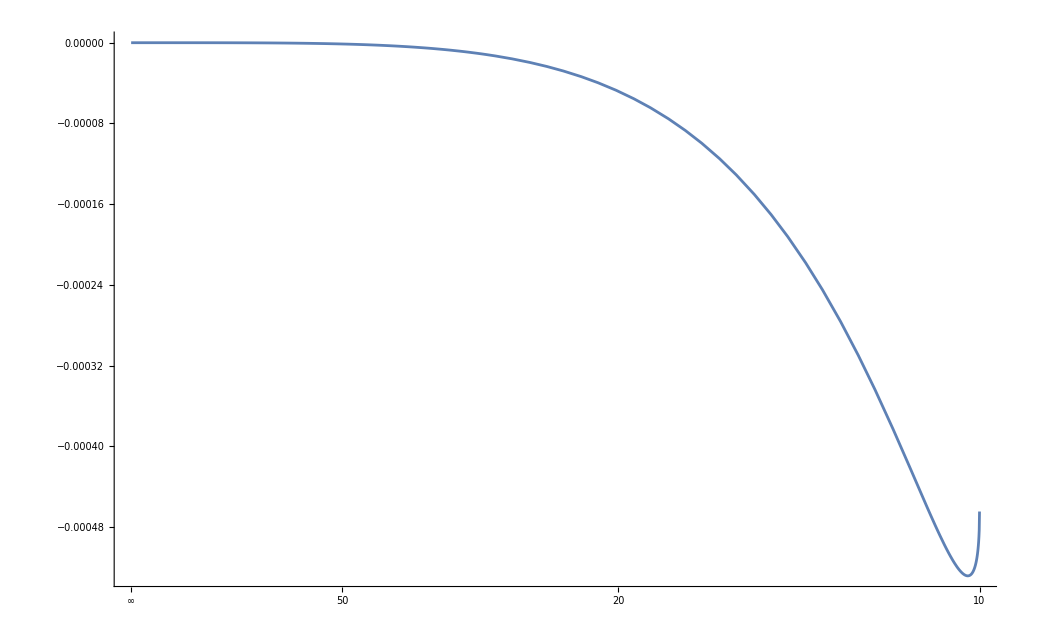

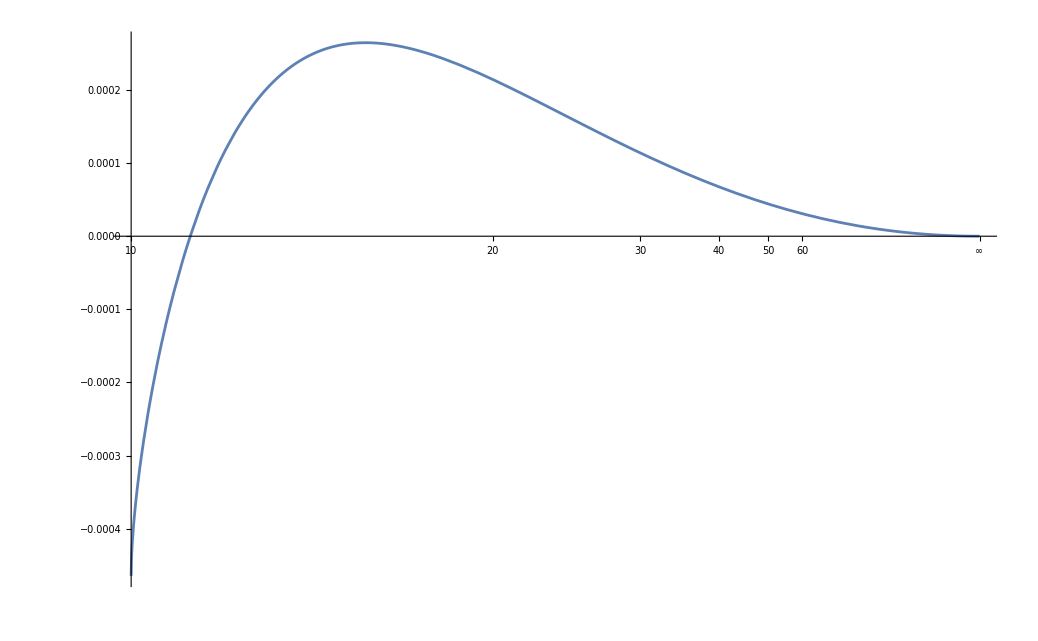

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Plot[Subscript[q, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[q, (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## θ=θ_0+θ_1+θ_2+θ_3+θ_4+θ_5+θ_6+θ_7

```mathematica
Clear[M,σ,ω,b1,l,U,z]
Subscript[θ1, (in)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)+((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ2, (in)] :=(3 l σ)/(16 b1^6 M ω) (1/48 b1 l^2 π (-6+π^2)+(l^4 (900 π^2-5120-27 π^4))/(10368 b1^2)-l^4/(8 z^2)+((8 b1^2 l^4+81 b1^4 l^2 z+160 l^4 z^2)√(-b1^2+z^2))/(324 b1^2 z^3)+(l^2 (-18 b1^3 (-2+π^2)+l^2 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+(l^2 (36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+(l^2 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^4 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ1, (out)] :=(3 l σ)/(8 M ω)(-(36 b1^3 π+l^2 (32-9 π^2))/(144 b1^6)-l^2/(4 b1^4 z^2)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))])/(4 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^2)/(4 b1^6)-((2 l^2 √(-b1^2+z^2))/(9 b1^6 z)+(√(-b1^2+z^2))/(2 b1^2 z^2)+(l^2 √(-b1^2+z^2))/(9 b1^4 z^3))) 
Subscript[θ2, (out)] :=(3 l^3 σ)/(16 b1^6 M ω) (-(-216 b1^3 π (-6+π^2)+l^2 (5120-900 π^2+27 π^4))/(10368 b1^2)-(162 b1^2 z √(-b1^2+z^2)+l^2 (16 √(-b1^2+z^2)+z (81+(320 z √(-b1^2+z^2))/b1^2)))/(648 z^3)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))])/(144 b1^2)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(144 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^3)/(12 b1^2)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^4)/(24 b1^2))
Subscript[θ3, (in)] :=(3 l^5 σ)/(64 b1^8 M ω)(-(1/960 b1 π (120-20 π^2+π^4)+(l^2 (1863680-9 π^2 (28840-750 π^2+9 π^4)))/(933120 b1^2))-l^2/(8 z^2)+(1456 l^2 √(-b1^2+z^2))/(729 b1^2 z)+(b1^2 √(-b1^2+z^2))/(4 z^2)+(8 l^2 √(-b1^2+z^2))/(729 z^3)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(25920 b1^2)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(5184 b1^2)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(216 b1^2)+((-36 b1^3 π+l^2 (-50+9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(432 b1^2)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(60 b1^2)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(180 b1^2))
Subscript[θ3, (out)] :=(3 l^5 σ)/(16 b1^6 M ω) ((-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))/(3732480 b1^4)-l^2/(32 b1^2 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^4 z)-(√(-b1^2+z^2))/(16 z^2)-(2 l^2 √(-b1^2+z^2))/(729 b1^2 z^3)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))])/(103680 b1^4)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(20736 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(864 b1^4)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(1728 b1^4)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^5)/(240 b1^4)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^6)/(720 b1^4))

Subscript[θ4, (in)] :=(3 l^7 σ)/(64 b1^8 M ω) (1/(1881169920 b1^4)(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)-l^2 (3761766400+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))-l^2/(32 b1^2 z^2)+(13120 l^2 √(-b1^2+z^2))/(6561 b1^4 z)+(√(-b1^2+z^2))/(16 z^2)+(8 l^2 √(-b1^2+z^2))/(6561 b1^2 z^3)-1/(13063680 b1^4)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^2)/(1866240 b1^4)-((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(155520 b1^4)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(62208 b1^4)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(4320 b1^4)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(12960 b1^4)-((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(2520 b1^4)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(10080 b1^4))
Subscript[θ4, (out)] :=(3 l^7 σ)/(16 b1^6 M ω) (1/(7524679680 b1^6)(11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))-l^2/(128 b1^4 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^6 z)-(√(-b1^2+z^2))/(64 b1^2 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(6561 b1^6 z^3)+1/(52254720 b1^6)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^2)/(7464960 b1^6)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^3)/(622080 b1^6)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^4)/(248832 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(17280 b1^6)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(51840 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^7)/(10080 b1^6)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^8)/(40320 b1^6))

Subscript[θ5, (in)] :=(3 l^9 σ)/(64 b1^8 M ω)(1/(677221171200 b1^6)(14580 b1^3 π (60480 π^2-362880-3024 π^4+72 π^6-π^8)-l^2 (1354419404800-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(128 b1^4 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^6 z)+(√(-b1^2+z^2))/(64 b1^2 z^2)+(8 l^2 √(-b1^2+z^2))/(59049 b1^4 z^3)+1/(3762339840 b1^6)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(3762339840 b1^6)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(78382080 b1^6)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(22394880 b1^6)(-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1922000+9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(3110400 b1^6)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(1866240 b1^6)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(181440 b1^6)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(725760 b1^6)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(181440 b1^6)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(907200 b1^6))
Subscript[θ5, (out)] :=(3 l^9 σ)/(16 b1^6 M ω)(1/(2708884684800 b1^8)(-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))-l^2/(512 b1^6 z^2)-(364 l^2 √(-b1^2+z^2))/(729 b1^8 z)-(√(-b1^2+z^2))/(256 b1^4 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+20 z^2))/(59049 b1^8 z^3)-1/(15049359360 b1^8)(l^2 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]+1/(15049359360 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^2-1/(313528320 b1^8)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^3-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^4)/(89579520 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^5)/(12441600 b1^8)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^6)/(7464960 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(725760 b1^8)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(2903040 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^9)/(725760 b1^8)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^10)/(3628800 b1^8))
Subscript[θ6, (in)] :=(3 l^11 σ)/(64 b1^8 M ω)(1/(1072718335180800 b1^8)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-l^2 (2145432633344000+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))))-l^2/(512 b1^6 z^2)+(118096 l^2 √(-b1^2+z^2))/(59049 b1^8 z)+(√(-b1^2+z^2))/(256 b1^4 z^2)+(8 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^8 z^3)-1/(14898865766400 b1^8)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(1354442342400 b1^8)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(22574039040 b1^8)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(45148078080 b1^8)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(1567641600 b1^8)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(671846400 b1^8)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(130636800 b1^8)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(104509440 b1^8)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(13063680 b1^8)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(65318400 b1^8)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(19958400 b1^8)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(119750400 b1^8))
Subscript[θ6, (out)] :=(3 l^11 σ)/(16 b1^6 M ω) (1/(4290873340723200 b1^10)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-5629872124800 π^4+47950056000 π^6-231267960 π^8+801900 π^10-2187 π^12))-l^2/(2048 b1^8 z^2)-(29524 l^2 √(-b1^2+z^2))/(59049 b1^10 z)-(√(-b1^2+z^2))/(1024 b1^6 z^2)-(2 l^2 √(-b1^2+z^2) (b1^2+2 z^2))/(531441 b1^10 z^3)+1/(59595463065600 b1^10)(l^2 π (14927712800000-625541347200 π^2+7991676000 π^4-51392880 π^6+222750 π^8-729 π^10)+16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)) ArcCot[b1/(√(-b1^2+z^2))]+1/(5417769369600 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(90296156160 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(180592312320 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(6270566400 b1^10)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^5+((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^6)/(2687385600 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^7)/(522547200 b1^10)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^8)/(418037760 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(52254720 b1^10)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(261273600 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^11)/(79833600 b1^10)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^12)/(479001600 b1^10))
Subscript[θ7, (in)] :=(3 l^13 σ)/(64 b1^8 M ω)(1/(7028450532104601600 b1^10)(551124 b1^3 π (1037836800 π^2-6227020800-51891840 π^4+1235520 π^6-17160 π^8+156 π^10-π^12)-l^2 (14056898125260390400-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6)))))-l^2/(2048 b1^8 z^2)+(9565936 l^2 √(-b1^2+z^2))/(4782969 b1^10 z)+(√(-b1^2+z^2))/(1024 b1^6 z^2)+(8 l^2 √(-b1^2+z^2))/(4782969 b1^8 z^3)+1/(27890676714700800 b1^10)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(2145436670361600 b1^10)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(89393194598400 b1^10)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(16253308108800 b1^10)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(451480780800 b1^10)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1354442342400 b1^10)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(65840947200 b1^10)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(37623398400 b1^10)+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(9405849600 b1^10)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(9405849600 b1^10)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1437004800 b1^10)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(8622028800 b1^10)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(3113510400 b1^10)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(21794572800 b1^10))
 Subscript[θ7, (out)] :=(3 l^13 σ)/(16M b1^6 ω)(1/(28113802128418406400 b1^12)(-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+1757967291861580800 π^2-36677390349600000 π^4+307391018014080 π^6-1402539138000 π^8+4209076872 π^10-9950850 π^12+19683 π^14))-l^2/(8192 b1^10 z^2)-(2391484 l^2 √(-b1^2+z^2))/(4782969 b1^12 z)-(√(-b1^2+z^2))/(4096 b1^8 z^2)-(2 l^2 √(-b1^2+z^2))/(4782969 b1^10 z^3)-1/(111562706858803200 b1^12)(l^2 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]+1/(8581746681446400 b1^12)(-52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(357572778393600 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(65013232435200 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(1805923123200 b1^12)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(5417769369600 b1^12)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^6-1/(263363788800 b1^12)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^7-((972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^8)/(150493593600 b1^12)+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^9)/(37623398400 b1^12)+((-216 b1^3 π (-6+π^2)+l^2 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^10)/(37623398400 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(5748019200 b1^12)-((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(34488115200 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^13)/(12454041600 b1^12)+(l^2 ArcCot[b1/(√(-b1^2+z^2))]^14)/(87178291200 b1^12))
Subscript[θ8, (in)] :=(3 l^15 σ)/(64 b1^8 M ω) (1/(20241937532461252608000 b1^12)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)-l^2 (40483874124458885120000+9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(8192 b1^10 z^2)+(86093440 l^2 √(-b1^2+z^2))/(43046721 b1^12 z)+(√(-b1^2+z^2))/(4096 b1^8 z^2)+(8 l^2 √(-b1^2+z^2))/(43046721 b1^10 z^3)-1/(70284505321046016000 b1^12)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(14056901064209203200 b1^12)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(167344060288204800 b1^12)(-56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(25745240044339200 b1^12)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(1787863891968000 b1^12)(-16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(487599243264000 b1^12)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(18962192793600 b1^12)(-1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7-1/(75848771174400 b1^12)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8-1/(4740548198400 b1^12)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9+1/(3386105856000 b1^12)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10+((-270 b1^3 (24-12 π^2+π^4)+l^2 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(1034643456000 b1^12)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(1241572147200 b1^12)-((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(224172748800 b1^12)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(1569209241600 b1^12)+((-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(653837184000 b1^12)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(5230697472000 b1^12))
Subscript[θ8, (out)] :=(3 l^15 σ)/(16 b1^6 M ω) (1/(80967750129845010432000 b1^14)(1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))-l^2/(32768 b1^12 z^2)-(21523360 l^2 √(-b1^2+z^2))/(43046721 b1^14 z)-(√(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(l^2 π (70293070277830400000-2929945486435968000 π^2+36677390349600000 π^4-219565012867200 π^6+779188410000 π^8-1913216760 π^10+3827250 π^12-6561 π^14)+196830 b1^3 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)(551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)(56862 b1^3 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)+l^2 π (-27904242727961600+3 π^2 (388120532800000-9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3+1/(102980960177356800 b1^14)(52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2146480209843200+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(7151455567872000 b1^14)(16038 b1^3 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^2 π (14927712800000-3 π^2 (208513782400+9 π^2 (-295988000+1903440 π^2-8250 π^4+27 π^6)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)(14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(75848771174400 b1^14)(1458 b1^3 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^2 π (-3791159680+3 π^2 (53816000-9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7-1/(303395084697600 b1^14)(-11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8+1/(18962192793600 b1^14)(l^2 π (13454000-605640 π^2+9450 π^4-81 π^6)+1134 b1^3 (-720+360 π^2-30 π^4+π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9+1/(13544423424000 b1^14)(972 b1^3 π (120-20 π^2+π^4)+l^2 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10+((l^2 π (-28840+1500 π^2-27 π^4)+270 b1^3 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11)/(4138573824000 b1^14)+((216 b1^3 π (-6+π^2)+l^2 (-5768+900 π^2-27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)+((l^2 π (50-3 π^2)+18 b1^3 (-2+π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+((36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+((2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^2 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))




Subscript[θ, (in)]:=(3 l σ)/(16 b1^6 M ω)(1/(80967750129845010432000 b1^14)(7809389480116224000 b1^12 (-5184 b1^5 π+216 b1^3 l^2 π (-6+π^2)+144 b1^2 l^2 (-32+9 π^2)+l^4 (-5120+900 π^2-27 π^4))+21692748555878400 b1^10 l^4 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))+10760291942400 b1^8 l^6 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))+18869760 b1^4 l^10 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))+l^14 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))+29889699840 b1^6 l^8 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+2880 b1^2 l^12 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))))-(l^2 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8))/(32768 b1^12 z^2)+1/(43046721 b1^14 z)4 l^2 (4782969 b1^14+5314410 b1^12 l^2+5373459 b1^10 l^4+5380020 b1^8 l^6+5380749 b1^6 l^8+5380830 b1^4 l^10+5380839 b1^2 l^12+5380840 l^14) √(-b1^2+z^2)+((4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) √(-b1^2+z^2))/(16384 b1^10 z^2)+(2 l^2 (9 b1^2+l^2) (81 b1^4+l^4) (6561 b1^8+l^8) √(-b1^2+z^2))/(43046721 b1^12 z^3)+1/(281138021284184064000 b1^14)(17159303056896000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8)-1793792000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π-8579651528448000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^2+2690688000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^3+714970960704000 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^4-1210809600 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^5-23832365356800 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^6+259459200 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^7+425577952800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^8-32432400 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^9-4728643920 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^10+2653560 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^11+35823060 b1^3 l^12 (4 b1^2+l^2) π^12-153090 l^14 (36 b1^2+25 l^2) π^13-196830 b1^3 l^14 π^14+6561 l^16 π^15) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)l^2 (28113802128418406400 b1^14+14056901064209203200 b1^15 π-585704211008716800 b1^13 l^2 π (-6+π^2)-390469474005811200 b1^12 l^2 (-50+9 π^2)+7321302637608960 b1^11 l^4 π (120-20 π^2+π^4)+2711593569484800 b1^10 l^4 (5768-900 π^2+27 π^4)-43579182366720 b1^9 l^6 π (-5040+840 π^2-42 π^4+π^6)+151316605440 b1^7 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-343901376 b1^5 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+551124 b1^3 l^12 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)-7532204359680 b1^8 l^6 (-1922000+9 π^2 (28840-750 π^2+9 π^4))+3736212480 b1^6 l^8 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))+6552 b1^2 l^12 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))-10378368 b1^4 l^10 (-1357064800000+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))+l^14 (14058614055566080000-9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)l^2 (-111562706858803200 b1^15+55781353429401600 b1^12 l^2 π+13945338357350400 b1^13 l^2 (-2+π^2)-774741019852800 b1^10 l^4 π (-50+3 π^2)-290527882444800 b1^11 l^4 (24-12 π^2+π^4)+1076029194240 b1^8 l^6 π (28840-1500 π^2+27 π^4)+2421065687040 b1^9 l^6 (-720+360 π^2-30 π^4+π^6)-2134978560 b1^6 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)-10808328960 b1^7 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+30023136 b1^5 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)-56862 b1^3 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)-1872 b1^2 l^12 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))+7413120 b1^4 l^10 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))+l^14 π (27904242727961600+3 π^2 (-388120532800000+9 π^2 (542135834240-3298152000 π^2+12372360 π^4-35100 π^6+81 π^8)))) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(102980960177356800 b1^14)l^4 (4290873340723200 b1^12+2145436670361600 b1^13 π-89393194598400 b1^11 l^2 π (-6+π^2)-59595463065600 b1^10 l^2 (-50+9 π^2)+1117414932480 b1^9 l^4 π (120-20 π^2+π^4)+413857382400 b1^8 l^4 (5768-900 π^2+27 π^4)-6651279360 b1^7 l^6 π (-5040+840 π^2-42 π^4+π^6)+23094720 b1^5 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-52488 b1^3 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-1149603840 b1^6 l^6 (-1922000+9 π^2 (28840-750 π^2+9 π^4))+570240 b1^4 l^8 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))+l^12 (2146480209843200+9 π^2 (-29855425600000+3 π^2 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))-1584 b1^2 l^10 (-1357064800000+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^4+1/(7151455567872000 b1^14)l^4 (59595463065600 b1^13-29797731532800 b1^10 l^2 π-7449432883200 b1^11 l^2 (-2+π^2)+413857382400 b1^8 l^4 π (-50+3 π^2)+155196518400 b1^9 l^4 (24-12 π^2+π^4)-574801920 b1^6 l^6 π (28840-1500 π^2+27 π^4)-1293304320 b1^7 l^6 (-720+360 π^2-30 π^4+π^6)+1140480 b1^4 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+5773680 b1^5 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-16038 b1^3 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^12 π (-14927712800000+625541347200 π^2+27 π^4 (-295988000+1903440 π^2-8250 π^4+27 π^6))-3960 b1^2 l^10 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)l^6 (2708884684800 b1^10+1354442342400 b1^11 π-56435097600 b1^9 l^2 π (-6+π^2)-37623398400 b1^8 l^2 (-50+9 π^2)+705438720 b1^7 l^4 π (120-20 π^2+π^4)+261273600 b1^6 l^4 (5768-900 π^2+27 π^4)-4199040 b1^5 l^6 π (-5040+840 π^2-42 π^4+π^6)+14580 b1^3 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)-725760 b1^4 l^6 (-1922000+9 π^2 (28840-750 π^2+9 π^4))+360 b1^2 l^8 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))+l^10 (1357064800000-9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2))))) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(75848771174400 b1^14)l^6 (-15049359360 b1^11+7524679680 b1^8 l^2 π+1881169920 b1^9 l^2 (-2+π^2)-104509440 b1^6 l^4 π (-50+3 π^2)-39191040 b1^7 l^4 (24-12 π^2+π^4)+145152 b1^4 l^6 π (28840-1500 π^2+27 π^4)+326592 b1^5 l^6 (-720+360 π^2-30 π^4+π^6)-288 b1^2 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)-1458 b1^3 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)+l^10 π (3791159680+3 π^2 (-53816000+9 π^2 (80752-600 π^2+3 π^4)))) ArcCot[b1/(√(-b1^2+z^2))]^7-1/(303395084697600 b1^14)l^8 (7524679680 b1^8+3762339840 b1^9 π-156764160 b1^7 l^2 π (-6+π^2)-104509440 b1^6 l^2 (-50+9 π^2)+1959552 b1^5 l^4 π (120-20 π^2+π^4)+725760 b1^4 l^4 (5768-900 π^2+27 π^4)-11664 b1^3 l^6 π (-5040+840 π^2-42 π^4+π^6)-2016 b1^2 l^6 (-1922000+9 π^2 (28840-750 π^2+9 π^4))+l^8 (3791159680+9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6))) ArcCot[b1/(√(-b1^2+z^2))]^8+1/(18962192793600 b1^14)l^8 (52254720 b1^9-26127360 b1^6 l^2 π-6531840 b1^7 l^2 (-2+π^2)+362880 b1^4 l^4 π (-50+3 π^2)+136080 b1^5 l^4 (24-12 π^2+π^4)-504 b1^2 l^6 π (28840-1500 π^2+27 π^4)-1134 b1^3 l^6 (-720+360 π^2-30 π^4+π^6)+l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9+1/(13544423424000 b1^14)l^10 (3732480 b1^6+1866240 b1^7 π-77760 b1^5 l^2 π (-6+π^2)-51840 b1^4 l^2 (-50+9 π^2)+972 b1^3 l^4 π (120-20 π^2+π^4)+360 b1^2 l^4 (5768-900 π^2+27 π^4)+l^6 (1922000-9 π^2 (28840-750 π^2+9 π^4))) ArcCot[b1/(√(-b1^2+z^2))]^10+1/(4138573824000 b1^14)l^10 (-103680 b1^7+51840 b1^4 l^2 π+12960 b1^5 l^2 (-2+π^2)-720 b1^2 l^4 π (-50+3 π^2)-270 b1^3 l^4 (24-12 π^2+π^4)+l^6 π (28840-1500 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11-1/(4966288588800 b1^14)l^12 (10368 b1^4+5184 b1^5 π+144 b1^2 l^2 (50-9 π^2)-216 b1^3 l^2 π (-6+π^2)+l^4 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12+(l^12 (144 b1^5-72 b1^2 l^2 π-18 b1^3 l^2 (-2+π^2)+l^4 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+(l^14 (72 b1^2+36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+(l^14 (-2 b1^3+l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^16 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))






















Subscript[θ, (out)]:=(3 l σ)/(16 b1^6 M ω)(1/(80967750129845010432000 b1^14)(7809389480116224000 b1^12 (-5184 b1^5 π+216 b1^3 l^2 π (-6+π^2)+144 b1^2 l^2 (-32+9 π^2)+l^4 (-5120+900 π^2-27 π^4))+21692748555878400 b1^10 l^4 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))+10760291942400 b1^8 l^6 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))+18869760 b1^4 l^10 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))+l^14 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))+29889699840 b1^6 l^8 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+2880 b1^2 l^12 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))))-(l^2 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8))/(32768 b1^12 z^2)-1/(43046721 b1^14 z)4 l^2 (4782969 b1^14+5314410 b1^12 l^2+5373459 b1^10 l^4+5380020 b1^8 l^6+5380749 b1^6 l^8+5380830 b1^4 l^10+5380839 b1^2 l^12+5380840 l^14) √(-b1^2+z^2)-1/(16384 b1^10 z^2)(16384 b1^14+4096 b1^12 l^2+1024 b1^10 l^4+256 b1^8 l^6+64 b1^6 l^8+16 b1^4 l^10+4 b1^2 l^12+l^14) √(-b1^2+z^2)-1/(43046721 b1^12 z^3)2 l^2 (4782969 b1^14+531441 b1^12 l^2+59049 b1^10 l^4+6561 b1^8 l^6+729 b1^6 l^8+81 b1^4 l^10+9 b1^2 l^12+l^14) √(-b1^2+z^2)-1/(281138021284184064000 b1^14)(281138021284184064000 b1^17-140569010642092032000 b1^14 l^2 π-35142252660523008000 b1^15 l^2 (-2+π^2)+1952347370029056000 b1^12 l^4 π (-50+3 π^2)+732130263760896000 b1^13 l^4 (24-12 π^2+π^4)-2711593569484800 b1^10 l^6 π (28840-1500 π^2+27 π^4)-6101085531340800 b1^11 l^6 (-720+360 π^2-30 π^4+π^6)+5380145971200 b1^8 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+27236988979200 b1^9 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-18681062400 b1^6 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-75658302720 b1^7 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+4717440 b1^4 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+143292240 b1^5 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)-2520 b1^2 l^14 π (27904242727961600-1164361598400000 π^2+14637667524480 π^4-89050104000 π^6+334053720 π^8-947700 π^10+2187 π^12)-196830 b1^3 l^14 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+l^16 π (-70293070277830400000+2929945486435968000 π^2-36677390349600000 π^4+219565012867200 π^6-779188410000 π^8+1913216760 π^10-3827250 π^12+6561 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)l^2 (28113802128418406400 b1^14+14056901064209203200 b1^15 π-585704211008716800 b1^13 l^2 π (-6+π^2)-390469474005811200 b1^12 l^2 (-50+9 π^2)+7321302637608960 b1^11 l^4 π (120-20 π^2+π^4)+2711593569484800 b1^10 l^4 (5768-900 π^2+27 π^4)-43579182366720 b1^9 l^6 π (-5040+840 π^2-42 π^4+π^6)-7532204359680 b1^8 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+151316605440 b1^7 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+3736212480 b1^6 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-343901376 b1^5 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-10378368 b1^4 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+551124 b1^3 l^12 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+6552 b1^2 l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)+l^14 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)l^2 (111562706858803200 b1^15-55781353429401600 b1^12 l^2 π-13945338357350400 b1^13 l^2 (-2+π^2)+774741019852800 b1^10 l^4 π (-50+3 π^2)+290527882444800 b1^11 l^4 (24-12 π^2+π^4)-1076029194240 b1^8 l^6 π (28840-1500 π^2+27 π^4)-2421065687040 b1^9 l^6 (-720+360 π^2-30 π^4+π^6)+2134978560 b1^6 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+10808328960 b1^7 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-7413120 b1^4 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-30023136 b1^5 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+1872 b1^2 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+l^14 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(102980960177356800 b1^14)l^4 (4290873340723200 b1^12+2145436670361600 b1^13 π-89393194598400 b1^11 l^2 π (-6+π^2)-59595463065600 b1^10 l^2 (-50+9 π^2)+1117414932480 b1^9 l^4 π (120-20 π^2+π^4)+413857382400 b1^8 l^4 (5768-900 π^2+27 π^4)-6651279360 b1^7 l^6 π (-5040+840 π^2-42 π^4+π^6)-1149603840 b1^6 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+23094720 b1^5 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+570240 b1^4 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-52488 b1^3 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-1584 b1^2 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(7151455567872000 b1^14)l^4 (59595463065600 b1^13-29797731532800 b1^10 l^2 π-7449432883200 b1^11 l^2 (-2+π^2)+413857382400 b1^8 l^4 π (-50+3 π^2)+155196518400 b1^9 l^4 (24-12 π^2+π^4)-574801920 b1^6 l^6 π (28840-1500 π^2+27 π^4)-1293304320 b1^7 l^6 (-720+360 π^2-30 π^4+π^6)+1140480 b1^4 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+5773680 b1^5 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-3960 b1^2 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-16038 b1^3 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)l^6 (2708884684800 b1^10+1354442342400 b1^11 π-56435097600 b1^9 l^2 π (-6+π^2)-37623398400 b1^8 l^2 (-50+9 π^2)+705438720 b1^7 l^4 π (120-20 π^2+π^4)+261273600 b1^6 l^4 (5768-900 π^2+27 π^4)-4199040 b1^5 l^6 π (-5040+840 π^2-42 π^4+π^6)-725760 b1^4 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+14580 b1^3 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+360 b1^2 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)+l^10 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(75848771174400 b1^14)l^6 (15049359360 b1^11-7524679680 b1^8 l^2 π-1881169920 b1^9 l^2 (-2+π^2)+104509440 b1^6 l^4 π (-50+3 π^2)+39191040 b1^7 l^4 (24-12 π^2+π^4)-145152 b1^4 l^6 π (28840-1500 π^2+27 π^4)-326592 b1^5 l^6 (-720+360 π^2-30 π^4+π^6)+288 b1^2 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+l^10 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]^7-1/(303395084697600 b1^14)l^8 (7524679680 b1^8+3762339840 b1^9 π-156764160 b1^7 l^2 π (-6+π^2)-104509440 b1^6 l^2 (-50+9 π^2)+1959552 b1^5 l^4 π (120-20 π^2+π^4)+725760 b1^4 l^4 (5768-900 π^2+27 π^4)-11664 b1^3 l^6 π (-5040+840 π^2-42 π^4+π^6)-2016 b1^2 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]^8-1/(18962192793600 b1^14)l^8 (52254720 b1^9-26127360 b1^6 l^2 π-6531840 b1^7 l^2 (-2+π^2)+362880 b1^4 l^4 π (-50+3 π^2)+136080 b1^5 l^4 (24-12 π^2+π^4)-504 b1^2 l^6 π (28840-1500 π^2+27 π^4)-1134 b1^3 l^6 (-720+360 π^2-30 π^4+π^6)+l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9+1/(13544423424000 b1^14)l^10 (3732480 b1^6+1866240 b1^7 π-77760 b1^5 l^2 π (-6+π^2)-51840 b1^4 l^2 (-50+9 π^2)+972 b1^3 l^4 π (120-20 π^2+π^4)+360 b1^2 l^4 (5768-900 π^2+27 π^4)+l^6 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^10+1/(4138573824000 b1^14)l^10 (103680 b1^7-51840 b1^4 l^2 π-12960 b1^5 l^2 (-2+π^2)+720 b1^2 l^4 π (-50+3 π^2)+l^6 π (-28840+1500 π^2-27 π^4)+270 b1^3 l^4 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11-1/(4966288588800 b1^14)l^12 (10368 b1^4+5184 b1^5 π-216 b1^3 l^2 π (-6+π^2)-144 b1^2 l^2 (-50+9 π^2)+l^4 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12-(l^12 (144 b1^5-72 b1^2 l^2 π-18 b1^3 l^2 (-2+π^2)+l^4 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+(l^14 (72 b1^2+36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+(l^14 (2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^16 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))
```

```mathematica
FullSimplify[Subscript[θ, (in)]-(Subscript[θ1, (in)]+Subscript[θ2, (in)]+Subscript[θ3, (in)]+Subscript[θ4, (in)]+Subscript[θ5, (in)]+Subscript[θ6, (in)]+Subscript[θ7, (in)]+Subscript[θ8, (in)])]
FullSimplify[Subscript[θ, (out)]-(Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)]+Subscript[θ5, (out)]+Subscript[θ6, (out)]+Subscript[θ7, (out)]+Subscript[θ8, (out)])]
```

0

0

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ1, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)]+Subscript[θ5, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)]+Subscript[θ5, (out)]+Subscript[θ6, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)]+Subscript[θ5, (out)]+Subscript[θ6, (out)]+Subscript[θ7, (out)],z->U]]
N[Limit[Subscript[θ1, (out)]+Subscript[θ2, (out)]+Subscript[θ3, (out)]+Subscript[θ4, (out)]+Subscript[θ5, (out)]+Subscript[θ6, (out)]+Subscript[θ7, (out)]+Subscript[θ8, (out)],z->U]]
Clear[M,σ,ω,b1,l,U]
```

-0.000463512

0.00020895

-0.0000196921

0.0000181588

0.0000143461

0.0000146073

0.0000145943

0.0000145948

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=50
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ1, (out)],z->U]]
N[Limit[Subscript[θ2, (out)],z->U]]
N[Limit[Subscript[θ3, (out)],z->U]]
N[Limit[Subscript[θ4, (out)],z->U]]
N[Limit[Subscript[θ5, (out)],z->U]]
N[Limit[Subscript[θ6, (out)],z->U]]
N[Limit[Subscript[θ7, (out)],z->U]]
N[Limit[Subscript[θ8, (out)],z->U]]
Clear[M,σ,ω,b1,l,U]
```

-0.000463512

0.000672462

-0.000228643

0.0000378509

-3.81278×10^-6

2.61275×10^-7

-1.30389×10^-8

4.96439×10^-10

### Crossing Point

#### Simplifying θ_(out)

θ_(out):=(3 l σ)/(16 b1^6 M ω)(1/(80967750129845010432000 b1^14)(7809389480116224000 b1^12 (-5184 b1^5 π+216 b1^3 l^2 π (-6+π^2)+144 b1^2 l^2 (-32+9 π^2)+l^4 (-5120+900 π^2-27 π^4))+21692748555878400 b1^10 l^4 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))+10760291942400 b1^8 l^6 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))+18869760 b1^4 l^10 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))+l^14 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))+29889699840 b1^6 l^8 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+2880 b1^2 l^12 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))))-(l^2 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8))/(32768 b1^12 z^2)-1/(43046721 b1^14 z)4 l^2 (4782969 b1^14+5314410 b1^12 l^2+5373459 b1^10 l^4+5380020 b1^8 l^6+5380749 b1^6 l^8+5380830 b1^4 l^10+5380839 b1^2 l^12+5380840 l^14) √(-b1^2+z^2)-((16384 b1^14+4096 b1^12 l^2+1024 b1^10 l^4+256 b1^8 l^6+64 b1^6 l^8+16 b1^4 l^10+4 b1^2 l^12+l^14) √(-b1^2+z^2))/(16384 b1^10 z^2)-(2 l^2 (4782969 b1^14+531441 b1^12 l^2+59049 b1^10 l^4+6561 b1^8 l^6+729 b1^6 l^8+81 b1^4 l^10+9 b1^2 l^12+l^14) √(-b1^2+z^2))/(43046721 b1^12 z^3)-1/(281138021284184064000 b1^14)(281138021284184064000 b1^17-140569010642092032000 b1^14 l^2 π-35142252660523008000 b1^15 l^2 (-2+π^2)+1952347370029056000 b1^12 l^4 π (-50+3 π^2)+732130263760896000 b1^13 l^4 (24-12 π^2+π^4)-2711593569484800 b1^10 l^6 π (28840-1500 π^2+27 π^4)-6101085531340800 b1^11 l^6 (-720+360 π^2-30 π^4+π^6)+5380145971200 b1^8 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+27236988979200 b1^9 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-18681062400 b1^6 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-75658302720 b1^7 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+4717440 b1^4 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+143292240 b1^5 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)-2520 b1^2 l^14 π (27904242727961600-1164361598400000 π^2+14637667524480 π^4-89050104000 π^6+334053720 π^8-947700 π^10+2187 π^12)-196830 b1^3 l^14 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+l^16 π (-70293070277830400000+2929945486435968000 π^2-36677390349600000 π^4+219565012867200 π^6-779188410000 π^8+1913216760 π^10-3827250 π^12+6561 π^14)) ArcCot[b1/(√(-b1^2+z^2))]+1/(56227604256836812800 b1^14)l^2 (28113802128418406400 b1^14+14056901064209203200 b1^15 π-585704211008716800 b1^13 l^2 π (-6+π^2)-390469474005811200 b1^12 l^2 (-50+9 π^2)+7321302637608960 b1^11 l^4 π (120-20 π^2+π^4)+2711593569484800 b1^10 l^4 (5768-900 π^2+27 π^4)-43579182366720 b1^9 l^6 π (-5040+840 π^2-42 π^4+π^6)-7532204359680 b1^8 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+151316605440 b1^7 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+3736212480 b1^6 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-343901376 b1^5 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-10378368 b1^4 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+551124 b1^3 l^12 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+6552 b1^2 l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)+l^14 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) ArcCot[b1/(√(-b1^2+z^2))]^2+1/(669376241152819200 b1^14)l^2 (111562706858803200 b1^15-55781353429401600 b1^12 l^2 π-13945338357350400 b1^13 l^2 (-2+π^2)+774741019852800 b1^10 l^4 π (-50+3 π^2)+290527882444800 b1^11 l^4 (24-12 π^2+π^4)-1076029194240 b1^8 l^6 π (28840-1500 π^2+27 π^4)-2421065687040 b1^9 l^6 (-720+360 π^2-30 π^4+π^6)+2134978560 b1^6 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+10808328960 b1^7 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-7413120 b1^4 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-30023136 b1^5 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+1872 b1^2 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+l^14 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) ArcCot[b1/(√(-b1^2+z^2))]^3-1/(102980960177356800 b1^14)l^4 (4290873340723200 b1^12+2145436670361600 b1^13 π-89393194598400 b1^11 l^2 π (-6+π^2)-59595463065600 b1^10 l^2 (-50+9 π^2)+1117414932480 b1^9 l^4 π (120-20 π^2+π^4)+413857382400 b1^8 l^4 (5768-900 π^2+27 π^4)-6651279360 b1^7 l^6 π (-5040+840 π^2-42 π^4+π^6)-1149603840 b1^6 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+23094720 b1^5 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+570240 b1^4 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-52488 b1^3 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-1584 b1^2 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) ArcCot[b1/(√(-b1^2+z^2))]^4-1/(7151455567872000 b1^14)l^4 (59595463065600 b1^13-29797731532800 b1^10 l^2 π-7449432883200 b1^11 l^2 (-2+π^2)+413857382400 b1^8 l^4 π (-50+3 π^2)+155196518400 b1^9 l^4 (24-12 π^2+π^4)-574801920 b1^6 l^6 π (28840-1500 π^2+27 π^4)-1293304320 b1^7 l^6 (-720+360 π^2-30 π^4+π^6)+1140480 b1^4 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+5773680 b1^5 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-3960 b1^2 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-16038 b1^3 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]^5+1/(1950396973056000 b1^14)l^6 (2708884684800 b1^10+1354442342400 b1^11 π-56435097600 b1^9 l^2 π (-6+π^2)-37623398400 b1^8 l^2 (-50+9 π^2)+705438720 b1^7 l^4 π (120-20 π^2+π^4)+261273600 b1^6 l^4 (5768-900 π^2+27 π^4)-4199040 b1^5 l^6 π (-5040+840 π^2-42 π^4+π^6)-725760 b1^4 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+14580 b1^3 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+360 b1^2 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)+l^10 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) ArcCot[b1/(√(-b1^2+z^2))]^6+1/(75848771174400 b1^14)l^6 (15049359360 b1^11-7524679680 b1^8 l^2 π-1881169920 b1^9 l^2 (-2+π^2)+104509440 b1^6 l^4 π (-50+3 π^2)+39191040 b1^7 l^4 (24-12 π^2+π^4)-145152 b1^4 l^6 π (28840-1500 π^2+27 π^4)-326592 b1^5 l^6 (-720+360 π^2-30 π^4+π^6)+288 b1^2 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+l^10 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) ArcCot[b1/(√(-b1^2+z^2))]^7-1/(303395084697600 b1^14)l^8 (7524679680 b1^8+3762339840 b1^9 π-156764160 b1^7 l^2 π (-6+π^2)-104509440 b1^6 l^2 (-50+9 π^2)+1959552 b1^5 l^4 π (120-20 π^2+π^4)+725760 b1^4 l^4 (5768-900 π^2+27 π^4)-11664 b1^3 l^6 π (-5040+840 π^2-42 π^4+π^6)-2016 b1^2 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) ArcCot[b1/(√(-b1^2+z^2))]^8-1/(18962192793600 b1^14)l^8 (52254720 b1^9-26127360 b1^6 l^2 π-6531840 b1^7 l^2 (-2+π^2)+362880 b1^4 l^4 π (-50+3 π^2)+136080 b1^5 l^4 (24-12 π^2+π^4)-504 b1^2 l^6 π (28840-1500 π^2+27 π^4)-1134 b1^3 l^6 (-720+360 π^2-30 π^4+π^6)+l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^9+1/(13544423424000 b1^14)l^10 (3732480 b1^6+1866240 b1^7 π-77760 b1^5 l^2 π (-6+π^2)-51840 b1^4 l^2 (-50+9 π^2)+972 b1^3 l^4 π (120-20 π^2+π^4)+360 b1^2 l^4 (5768-900 π^2+27 π^4)+l^6 (1922000-259560 π^2+6750 π^4-81 π^6)) ArcCot[b1/(√(-b1^2+z^2))]^10+1/(4138573824000 b1^14)l^10 (103680 b1^7-51840 b1^4 l^2 π-12960 b1^5 l^2 (-2+π^2)+720 b1^2 l^4 π (-50+3 π^2)+l^6 π (-28840+1500 π^2-27 π^4)+270 b1^3 l^4 (24-12 π^2+π^4)) ArcCot[b1/(√(-b1^2+z^2))]^11(l^12 (10368 b1^4+5184 b1^5 π-216 b1^3 l^2 π (-6+π^2)-144 b1^2 l^2 (-50+9 π^2)+l^4 (5768-900 π^2+27 π^4)) ArcCot[b1/(√(-b1^2+z^2))]^12)/(4966288588800 b1^14)-(l^12 (144 b1^5-72 b1^2 l^2 π-18 b1^3 l^2 (-2+π^2)+l^4 π (-50+3 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^13)/(896690995200 b1^14)+(l^14 (72 b1^2+36 b1^3 π+l^2 (50-9 π^2)) ArcCot[b1/(√(-b1^2+z^2))]^14)/(6276836966400 b1^14)+(l^14 (2 b1^3-l^2 π) ArcCot[b1/(√(-b1^2+z^2))]^15)/(2615348736000 b1^14)-(l^16 ArcCot[b1/(√(-b1^2+z^2))]^16)/(20922789888000 b1^14))

```mathematica
Simplify[Series[ArcCot[b1/(√(-b1^2+z^2))],{z,∞,5}],Assumptions->{b1>1}]
```

π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5)+O[1/z]^6

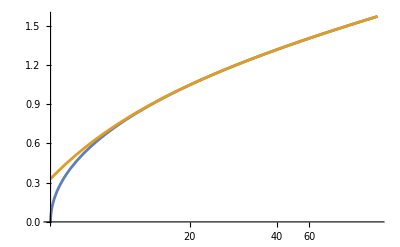

```mathematica
σ=1;
ω=1;
M:=1
b1=10;
b3:=1/2 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))-l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)-ⅈ √3 (-l^(4/3)/(3 (-1/2+√(1/4-l^2/27))^(1/3))+l^(2/3) (-1/2+√(1/4-l^2/27))^(1/3)));
b2=-b1-b3;
l=b1^(3/2)/(√(b1-1));
Plot[{ArcCot[b1/(√(-b1^2+z^2))],(π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))},{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

```mathematica
Subscript[Simb1θ, (out)]:=(3 l σ)/(16 b1^6 M ω)(1/(80967750129845010432000 b1^14)(7809389480116224000 b1^12 (-5184 b1^5 π+216 b1^3 l^2 π (-6+π^2)+144 b1^2 l^2 (-32+9 π^2)+l^4 (-5120+900 π^2-27 π^4))+21692748555878400 b1^10 l^4 (-972 b1^3 π (120-20 π^2+π^4)+l^2 (-1863680+9 π^2 (28840-750 π^2+9 π^4)))+10760291942400 b1^8 l^6 (11664 b1^3 π (-5040+840 π^2-42 π^4+π^6)+l^2 (-3761766400-9 π^2 (-53816000+1211280 π^2-12600 π^4+81 π^6)))+18869760 b1^4 l^10 (52488 b1^3 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)+l^2 (-2145432633344000+268698830400000 π^2-27 π^4 (208513782400-1775928000 π^2+8565480 π^4-29700 π^6+81 π^8)))+l^14 (1889568 b1^3 π (-1307674368000+217945728000 π^2-10897286400 π^4+259459200 π^6-3603600 π^8+32760 π^10-210 π^12+π^14)+l^2 (-40483874124458885120000-9 π^2 (-562344562222643200000+11719781945743872000 π^2-97806374265600000 π^4+81 π^6 (5421358342400-15391376000 π^2+31493280 π^4-54000 π^6+81 π^8))))+29889699840 b1^6 l^8 (-14580 b1^3 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+l^2 (-1354419404800+9 π^2 (18955798400-403620000 π^2+9 π^4 (403760+9 π^2 (-250+π^2)))))+2880 b1^2 l^12 (-551124 b1^3 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+l^2 (-14056898125260390400+9 π^2 (195329699095731200-4075265594400000 π^2+9 π^4 (3794950839680+9 π^2 (-1923922000+5773768 π^2-13650 π^4+27 π^6))))))-1/(43046721 b1^14 z)4 l^2 (4782969 b1^14+5314410 b1^12 l^2+5373459 b1^10 l^4+5380020 b1^8 l^6+5380749 b1^6 l^8+5380830 b1^4 l^10+5380839 b1^2 l^12+5380840 l^14) √(-b1^2+z^2)-((16384 b1^14+4096 b1^12 l^2+1024 b1^10 l^4+256 b1^8 l^6+64 b1^6 l^8+16 b1^4 l^10+4 b1^2 l^12+l^14) √(-b1^2+z^2))/(16384 b1^10 z^2)-1/(281138021284184064000 b1^14)(281138021284184064000 b1^17-140569010642092032000 b1^14 l^2 π-35142252660523008000 b1^15 l^2 (-2+π^2)+1952347370029056000 b1^12 l^4 π (-50+3 π^2)+732130263760896000 b1^13 l^4 (24-12 π^2+π^4)-2711593569484800 b1^10 l^6 π (28840-1500 π^2+27 π^4)-6101085531340800 b1^11 l^6 (-720+360 π^2-30 π^4+π^6)+5380145971200 b1^8 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+27236988979200 b1^9 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-18681062400 b1^6 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-75658302720 b1^7 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+4717440 b1^4 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+143292240 b1^5 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)-2520 b1^2 l^14 π (27904242727961600-1164361598400000 π^2+14637667524480 π^4-89050104000 π^6+334053720 π^8-947700 π^10+2187 π^12)-196830 b1^3 l^14 (-87178291200+43589145600 π^2-3632428800 π^4+121080960 π^6-2162160 π^8+24024 π^10-182 π^12+π^14)+l^16 π (-70293070277830400000+2929945486435968000 π^2-36677390349600000 π^4+219565012867200 π^6-779188410000 π^8+1913216760 π^10-3827250 π^12+6561 π^14)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))+1/(56227604256836812800 b1^14)l^2 (28113802128418406400 b1^14+14056901064209203200 b1^15 π-585704211008716800 b1^13 l^2 π (-6+π^2)-390469474005811200 b1^12 l^2 (-50+9 π^2)+7321302637608960 b1^11 l^4 π (120-20 π^2+π^4)+2711593569484800 b1^10 l^4 (5768-900 π^2+27 π^4)-43579182366720 b1^9 l^6 π (-5040+840 π^2-42 π^4+π^6)-7532204359680 b1^8 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+151316605440 b1^7 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+3736212480 b1^6 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-343901376 b1^5 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-10378368 b1^4 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+551124 b1^3 l^12 π (6227020800-1037836800 π^2+51891840 π^4-1235520 π^6+17160 π^8-156 π^10+π^12)+6552 b1^2 l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)+l^14 (14058614055566080000-1757967291861580800 π^2+36677390349600000 π^4-307391018014080 π^6+1402539138000 π^8-4209076872 π^10+9950850 π^12-19683 π^14)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^2+1/(669376241152819200 b1^14)l^2 (111562706858803200 b1^15-55781353429401600 b1^12 l^2 π-13945338357350400 b1^13 l^2 (-2+π^2)+774741019852800 b1^10 l^4 π (-50+3 π^2)+290527882444800 b1^11 l^4 (24-12 π^2+π^4)-1076029194240 b1^8 l^6 π (28840-1500 π^2+27 π^4)-2421065687040 b1^9 l^6 (-720+360 π^2-30 π^4+π^6)+2134978560 b1^6 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+10808328960 b1^7 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-7413120 b1^4 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-30023136 b1^5 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+1872 b1^2 l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)+l^14 π (-27904242727961600+1164361598400000 π^2-14637667524480 π^4+89050104000 π^6-334053720 π^8+947700 π^10-2187 π^12)+56862 b1^3 l^12 (479001600-239500800 π^2+19958400 π^4-665280 π^6+11880 π^8-132 π^10+π^12)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^3-1/(102980960177356800 b1^14)l^4 (4290873340723200 b1^12+2145436670361600 b1^13 π-89393194598400 b1^11 l^2 π (-6+π^2)-59595463065600 b1^10 l^2 (-50+9 π^2)+1117414932480 b1^9 l^4 π (120-20 π^2+π^4)+413857382400 b1^8 l^4 (5768-900 π^2+27 π^4)-6651279360 b1^7 l^6 π (-5040+840 π^2-42 π^4+π^6)-1149603840 b1^6 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+23094720 b1^5 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+570240 b1^4 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)-52488 b1^3 l^10 π (-39916800+6652800 π^2-332640 π^4+7920 π^6-110 π^8+π^10)-1584 b1^2 l^10 (-1357064800000+170602185600 π^2-3632580000 π^4+32704560 π^6-182250 π^8+729 π^10)+l^12 (2146480209843200-268698830400000 π^2+5629872124800 π^4-47950056000 π^6+231267960 π^8-801900 π^10+2187 π^12)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^4-1/(7151455567872000 b1^14)l^4 (59595463065600 b1^13-29797731532800 b1^10 l^2 π-7449432883200 b1^11 l^2 (-2+π^2)+413857382400 b1^8 l^4 π (-50+3 π^2)+155196518400 b1^9 l^4 (24-12 π^2+π^4)-574801920 b1^6 l^6 π (28840-1500 π^2+27 π^4)-1293304320 b1^7 l^6 (-720+360 π^2-30 π^4+π^6)+1140480 b1^4 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+5773680 b1^5 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)-3960 b1^2 l^10 π (3791159680-161448000 π^2+2180304 π^4-16200 π^6+81 π^8)-16038 b1^3 l^10 (-3628800+1814400 π^2-151200 π^4+5040 π^6-90 π^8+π^10)+l^12 π (-14927712800000+625541347200 π^2-7991676000 π^4+51392880 π^6-222750 π^8+729 π^10)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^5+1/(1950396973056000 b1^14)l^6 (2708884684800 b1^10+1354442342400 b1^11 π-56435097600 b1^9 l^2 π (-6+π^2)-37623398400 b1^8 l^2 (-50+9 π^2)+705438720 b1^7 l^4 π (120-20 π^2+π^4)+261273600 b1^6 l^4 (5768-900 π^2+27 π^4)-4199040 b1^5 l^6 π (-5040+840 π^2-42 π^4+π^6)-725760 b1^4 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+14580 b1^3 l^8 π (362880-60480 π^2+3024 π^4-72 π^6+π^8)+360 b1^2 l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)+l^10 (1357064800000-170602185600 π^2+3632580000 π^4-32704560 π^6+182250 π^8-729 π^10)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^6+1/(75848771174400 b1^14)l^6 (15049359360 b1^11-7524679680 b1^8 l^2 π-1881169920 b1^9 l^2 (-2+π^2)+104509440 b1^6 l^4 π (-50+3 π^2)+39191040 b1^7 l^4 (24-12 π^2+π^4)-145152 b1^4 l^6 π (28840-1500 π^2+27 π^4)-326592 b1^5 l^6 (-720+360 π^2-30 π^4+π^6)+288 b1^2 l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)+l^10 π (-3791159680+161448000 π^2-2180304 π^4+16200 π^6-81 π^8)+1458 b1^3 l^8 (40320-20160 π^2+1680 π^4-56 π^6+π^8)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^7-1/(303395084697600 b1^14)l^8 (7524679680 b1^8+3762339840 b1^9 π-156764160 b1^7 l^2 π (-6+π^2)-104509440 b1^6 l^2 (-50+9 π^2)+1959552 b1^5 l^4 π (120-20 π^2+π^4)+725760 b1^4 l^4 (5768-900 π^2+27 π^4)-11664 b1^3 l^6 π (-5040+840 π^2-42 π^4+π^6)-2016 b1^2 l^6 (-1922000+259560 π^2-6750 π^4+81 π^6)+l^8 (3791159680-484344000 π^2+10901520 π^4-113400 π^6+729 π^8)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^8-1/(18962192793600 b1^14)l^8 (52254720 b1^9-26127360 b1^6 l^2 π-6531840 b1^7 l^2 (-2+π^2)+362880 b1^4 l^4 π (-50+3 π^2)+136080 b1^5 l^4 (24-12 π^2+π^4)-504 b1^2 l^6 π (28840-1500 π^2+27 π^4)-1134 b1^3 l^6 (-720+360 π^2-30 π^4+π^6)+l^8 π (-13454000+605640 π^2-9450 π^4+81 π^6)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^9+1/(13544423424000 b1^14)l^10 (3732480 b1^6+1866240 b1^7 π-77760 b1^5 l^2 π (-6+π^2)-51840 b1^4 l^2 (-50+9 π^2)+972 b1^3 l^4 π (120-20 π^2+π^4)+360 b1^2 l^4 (5768-900 π^2+27 π^4)+l^6 (1922000-259560 π^2+6750 π^4-81 π^6)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^10-(l^12 (10368 b1^4+5184 b1^5 π-216 b1^3 l^2 π (-6+π^2)-144 b1^2 l^2 (-50+9 π^2)+l^4 (5768-900 π^2+27 π^4)) (π/2-b1/z-b1^3/(6 z^3)-(3 b1^5)/(40 z^5))^12)/(4966288588800 b1^14))
```

1.78849×10^-15

1.78488×10^-15

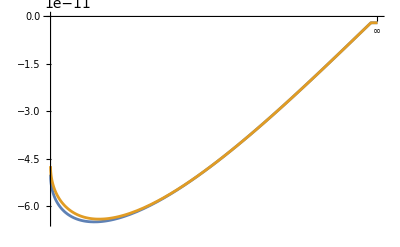

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100000
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ, (out)],z->U]]
N[Limit[Subscript[Simb1θ, (out)],z->U]]
Plot[{Subscript[θ, (out)],Subscript[Simb1θ, (out)]},{z,b1,∞}]
Clear[b1,l,U,M,σ,ω]
```

```mathematica
Simplify[Series[Subscript[Simb1θ, (out)],{z,∞,1}],Assumptions->{M>0,b1>M}]
```

-1/(431828000692506722304000 (b1^20 M ω))l (80967750129845010432000 b1^17 π-6747312510820417536000 b1^15 l^2 π (-3+2 π^2)-4498208340546945024000 b1^14 l^2 (-16+9 π^2)+337365625541020876800 b1^13 l^4 π (15-10 π^2+2 π^4)+124950231681859584000 b1^12 l^4 (640-225 π^2+27 π^4)-4016257446916915200 b1^11 l^6 π (-315+210 π^2-42 π^4+4 π^6)-694167953788108800 b1^10 l^6 (-116480+32445 π^2-3375 π^4+162 π^6)+111562706858803200 b1^9 l^8 π (2835-1890 π^2+378 π^4-36 π^6+2 π^8)+2754634737254400 b1^8 l^8 (29388800-7567875 π^2+681345 π^4-28350 π^6+729 π^8)-15303526318080 b1^6 l^10 (-5290700800+1332829575 π^2-113518125 π^4+4088070 π^6-91125 π^8+1458 π^10)-990435962880 b1^7 l^10 π (-79833600+53222400 π^2-10644480 π^4+1013760 π^6-56320 π^8+2047 π^10)+1587237120 b1^5 l^12 π (12454041600-8302694400 π^2+1660538880 π^4-158146560 π^6+8785920 π^8-319332 π^10+8113 π^12)+75479040 b1^4 l^12 (1072716316672000-268698830400000 π^2+22519488499200 π^4-767200896000 π^6+14801149440 π^8-205286400 π^10+2232927 π^12)-3779136 b1^3 l^14 π (-1307674368000+871782912000 π^2-174356582400 π^4+16605388800 π^6-922521600 π^8+33529860 π^10-851865 π^12+15641 π^14)-2880 b1^2 l^14 (-28113796250520780800+7031869167446323200 π^2-586838245593600000 π^4+19673025152901120 π^6-359050019328000 π^8+4310094716928 π^10-40639271400 π^12+315026415 π^14)+l^16 (80967748248917770240000-20244404240015155200000 π^2+1687648600187117568000 π^4-56336471576985600000 π^6+1011755579292057600 π^8-11489600618496000 π^10+93762926974080 π^12-630052830000 π^14+3570752079 π^16)) σ-1/(1499402780182315008000 (b1^19 M ω) z)l^3 π (281138021284184064000 b1^14+140569010642092032000 b1^15 π-11714084220174336000 b1^13 l^2 π (-3+π^2)-7809389480116224000 b1^12 l^2 (-25+6 π^2)+195234737002905600 b1^11 l^4 π (45-15 π^2+2 π^4)+43385497111756800 b1^10 l^4 (3605-750 π^2+54 π^4)-6972669178675200 b1^9 l^6 π (-315+105 π^2-14 π^4+π^6)-172164671078400 b1^8 l^6 (-840875+151410 π^2-9450 π^4+324 π^6)+4782351974400 b1^6 l^8 (29618435-5045250 π^2+272538 π^4-8100 π^6+162 π^8)+226974908160 b1^7 l^8 π (2419200-806400 π^2+107520 π^4-7680 π^6+341 π^8)-429876720 b1^5 l^10 π (-319334400+106444800 π^2-14192640 π^4+1013760 π^6-45012 π^8+1343 π^10)-4717440 b1^4 l^10 (-29855425600000+5004330777600 π^2-255733632000 π^4+6578288640 π^6-114048000 π^8+1484973 π^10)+196830 b1^3 l^12 π (174356582400-58118860800 π^2+7749181440 π^4-553512960 π^6+24576552 π^8-733278 π^10+15277 π^12)+10080 b1^2 l^12 (13952121363980800-2328723196800000 π^2+117101340195840 π^4-2849603328000 π^6+42758876160 π^8-482616225 π^10+4314951 π^12)+l^14 (140586140555660800000-23439563891487744000 π^2+1173676491187200000 π^4-28104321647001600 π^6+398944465920000 π^8-3897222540120 π^10+30204657000 π^12-191509029 π^14)) σ+O[1/z]^2

```mathematica
Subscript[Simz1θ, (out)]:=-1/(431828000692506722304000 (b1^20 M ω))l (80967750129845010432000 b1^17 π-6747312510820417536000 b1^15 l^2 π (-3+2 π^2)-4498208340546945024000 b1^14 l^2 (-16+9 π^2)+337365625541020876800 b1^13 l^4 π (15-10 π^2+2 π^4)+124950231681859584000 b1^12 l^4 (640-225 π^2+27 π^4)-4016257446916915200 b1^11 l^6 π (-315+210 π^2-42 π^4+4 π^6)-694167953788108800 b1^10 l^6 (-116480+32445 π^2-3375 π^4+162 π^6)+111562706858803200 b1^9 l^8 π (2835-1890 π^2+378 π^4-36 π^6+2 π^8)+2754634737254400 b1^8 l^8 (29388800-7567875 π^2+681345 π^4-28350 π^6+729 π^8)-15303526318080 b1^6 l^10 (-5290700800+1332829575 π^2-113518125 π^4+4088070 π^6-91125 π^8+1458 π^10)-990435962880 b1^7 l^10 π (-79833600+53222400 π^2-10644480 π^4+1013760 π^6-56320 π^8+2047 π^10)+1587237120 b1^5 l^12 π (12454041600-8302694400 π^2+1660538880 π^4-158146560 π^6+8785920 π^8-319332 π^10+8113 π^12)+75479040 b1^4 l^12 (1072716316672000-268698830400000 π^2+22519488499200 π^4-767200896000 π^6+14801149440 π^8-205286400 π^10+2232927 π^12)-3779136 b1^3 l^14 π (-1307674368000+871782912000 π^2-174356582400 π^4+16605388800 π^6-922521600 π^8+33529860 π^10-851865 π^12+15641 π^14)-2880 b1^2 l^14 (-28113796250520780800+7031869167446323200 π^2-586838245593600000 π^4+19673025152901120 π^6-359050019328000 π^8+4310094716928 π^10-40639271400 π^12+315026415 π^14)+l^16 (80967748248917770240000-20244404240015155200000 π^2+1687648600187117568000 π^4-56336471576985600000 π^6+1011755579292057600 π^8-11489600618496000 π^10+93762926974080 π^12-630052830000 π^14+3570752079 π^16)) σ-1/(1499402780182315008000 (b1^19 M ω) z)l^3 π (281138021284184064000 b1^14+140569010642092032000 b1^15 π-11714084220174336000 b1^13 l^2 π (-3+π^2)-7809389480116224000 b1^12 l^2 (-25+6 π^2)+195234737002905600 b1^11 l^4 π (45-15 π^2+2 π^4)+43385497111756800 b1^10 l^4 (3605-750 π^2+54 π^4)-6972669178675200 b1^9 l^6 π (-315+105 π^2-14 π^4+π^6)-172164671078400 b1^8 l^6 (-840875+151410 π^2-9450 π^4+324 π^6)+4782351974400 b1^6 l^8 (29618435-5045250 π^2+272538 π^4-8100 π^6+162 π^8)+226974908160 b1^7 l^8 π (2419200-806400 π^2+107520 π^4-7680 π^6+341 π^8)-429876720 b1^5 l^10 π (-319334400+106444800 π^2-14192640 π^4+1013760 π^6-45012 π^8+1343 π^10)-4717440 b1^4 l^10 (-29855425600000+5004330777600 π^2-255733632000 π^4+6578288640 π^6-114048000 π^8+1484973 π^10)+196830 b1^3 l^12 π (174356582400-58118860800 π^2+7749181440 π^4-553512960 π^6+24576552 π^8-733278 π^10+15277 π^12)+10080 b1^2 l^12 (13952121363980800-2328723196800000 π^2+117101340195840 π^4-2849603328000 π^6+42758876160 π^8-482616225 π^10+4314951 π^12)+l^14 (140586140555660800000-23439563891487744000 π^2+1173676491187200000 π^4-28104321647001600 π^6+398944465920000 π^8-3897222540120 π^10+30204657000 π^12-191509029 π^14)) σ
```

1.78849×10^-15

1.78488×10^-15

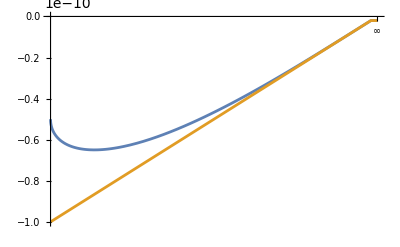

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100000
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ, (out)],z->U]]
N[Limit[Subscript[Simz1θ, (out)],z->U]]
Plot[{Subscript[θ, (out)],Subscript[Simz1θ, (out)]},{z,b1,∞}]
Clear[b1,l,U,M,σ,ω]
```

```mathematica
Subscript[Simb12θ, (out)]:=Simplify[Subscript[Simz1θ, (out)]/.{b1->l-1/2}]
```

```mathematica
Simplify[Series[Subscript[Simb12θ, (out)],{l,∞,4}],Assumptions->{M>0,b1>M}]
```

-(π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12) σ)/(7617755322777600 (M z ω) l)+1/(1499402780182315008000 M z ω l^2)π (-437219041889710080000 π+52027006868508672000 π^3-2251300561064755200 π^5+49244476074393600 π^7-638537160381120 π^9+5195919914640 π^11-24055775280 π^13-9338490 π^12 (7892+5985 z)+6561 π^14 (29189+31282 z)-16605388800 π^8 (129037+61965 z)+55724760 π^10 (282949+165807 z)+33210777600 π^6 (5491573+2237301 z)-38745907200 π^4 (227988253+80601885 z)+21525504000 π^2 (9296497669+2902199301 z)-3587584000 (373860772909+104483957805 z)) σ-1/(431828000692506722304000 (M z ω) l^3)(637621032507645362176000 z+3570752079 π^16 z+102820567449600 π^9 (46285+16767 z)-16061328 π^15 (32623+31282 z)-4723920 π^14 (-6233016+325435 z)+127370880 π^12 (-45362511+2978257 z)+1195587993600 π^8 (-34930764+5491573 z)+22044960 π^13 (8578604+5622309 z)-1146337920 π^11 (32890081+15751665 z)-4782351974400 π^7 (78437095+21605373 z)-1868106240 π^10 (-336340917+33033472 z)-1859803545600 π^6 (-858572460+227988253 z)+5579410636800 π^5 (3003883039+617711589 z)+1549836288000 π^4 (-19155259404+9296497669 z)-3099672576000 π^3 (112414125847+16443315981 z)-516612096000 π^2 (-368307744876+373860772909 z)+516612096000 π (4122110977999+383082336117 z)) σ-1/(215914000346253361152000 (M z ω) l^4)(2089347490986567139328000 z+17853760395 π^16 z-8030664 π^15 (163115+140769 z)-4723920 π^14 (-9349524+1531145 z)+597793996800 π^9 (16669714+4602177 z)-20324995891200 π^7 (36602498+6882489 z)+127370880 π^12 (-62332659+13108619 z)+1195587993600 π^8 (-37660140+20982167 z)+99034538803200 π^5 (319807934+38677095 z)+5511240 π^13 (80956136+46219761 z)-286584480 π^11 (292112590+115456941 z)-1868106240 π^10 (-413900685+135634688 z)-1859803545600 π^6 (-792437580+807967823 z)+1549836288000 π^4 (-14750676396+30427655879 z)-774918144000 π^3 (816251984194+57366398745 z)+129153024000 π (29071431082834+986482573281 z)-516612096000 π^2 (-230711292684+1123992937727 z)) σ+O[1/l]^5

```mathematica
Subscript[Simlθ, (out)]:=-(π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12) σ)/(7617755322777600 (M z ω) l)+1/(1499402780182315008000 M z ω l^2)π (-437219041889710080000 π+52027006868508672000 π^3-2251300561064755200 π^5+49244476074393600 π^7-638537160381120 π^9+5195919914640 π^11-24055775280 π^13-9338490 π^12 (7892+5985 z)+6561 π^14 (29189+31282 z)-16605388800 π^8 (129037+61965 z)+55724760 π^10 (282949+165807 z)+33210777600 π^6 (5491573+2237301 z)-38745907200 π^4 (227988253+80601885 z)+21525504000 π^2 (9296497669+2902199301 z)-3587584000 (373860772909+104483957805 z)) σ-1/(431828000692506722304000 (M z ω) l^3)(637621032507645362176000 z+3570752079 π^16 z+102820567449600 π^9 (46285+16767 z)-16061328 π^15 (32623+31282 z)-4723920 π^14 (-6233016+325435 z)+127370880 π^12 (-45362511+2978257 z)+1195587993600 π^8 (-34930764+5491573 z)+22044960 π^13 (8578604+5622309 z)-1146337920 π^11 (32890081+15751665 z)-4782351974400 π^7 (78437095+21605373 z)-1868106240 π^10 (-336340917+33033472 z)-1859803545600 π^6 (-858572460+227988253 z)+5579410636800 π^5 (3003883039+617711589 z)+1549836288000 π^4 (-19155259404+9296497669 z)-3099672576000 π^3 (112414125847+16443315981 z)-516612096000 π^2 (-368307744876+373860772909 z)+516612096000 π (4122110977999+383082336117 z)) σ-1/(215914000346253361152000 (M z ω) l^4)(2089347490986567139328000 z+17853760395 π^16 z-8030664 π^15 (163115+140769 z)-4723920 π^14 (-9349524+1531145 z)+597793996800 π^9 (16669714+4602177 z)-20324995891200 π^7 (36602498+6882489 z)+127370880 π^12 (-62332659+13108619 z)+1195587993600 π^8 (-37660140+20982167 z)+99034538803200 π^5 (319807934+38677095 z)+5511240 π^13 (80956136+46219761 z)-286584480 π^11 (292112590+115456941 z)-1868106240 π^10 (-413900685+135634688 z)-1859803545600 π^6 (-792437580+807967823 z)+1549836288000 π^4 (-14750676396+30427655879 z)-774918144000 π^3 (816251984194+57366398745 z)+129153024000 π (29071431082834+986482573281 z)-516612096000 π^2 (-230711292684+1123992937727 z)) σ
```

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100000
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ, (out)],z->U]]
N[Limit[Subscript[Simlθ, (out)],z->U]]
Plot[{Subscript[θ, (out)],Subscript[Simlθ, (out)]},{z,b1,∞}]
Clear[b1,l,U,M,σ,ω]
```

1.78849×10^-15

1.78487×10^-15

-Graphics-

```mathematica
Simplify[Series[Subscript[Simlθ, (out)],{z,∞,2}],Assumptions->{M>0,b1>M}]
```

1/(431828000692506722304000 l^4 M ω)(3779136 l^2 π (-28566146568960000+4760806482432000 π^2-237996734976000 π^4+5662437580800 π^6-78414336000 π^8+704127060 π^10-4259325 π^12+15641 π^14)+l (-637621032507645362176000-197904968601979871232000 π+193140997504698507264000 π^2+50968895604808237056000 π^3-14408049438723612672000 π^4-3446466610141229875200 π^5+424013361284549836800 π^6+103324498224198451200 π^7-6565658744777932800 π^8-1723992454427443200 π^9+61710035172065280 π^10+18056730892636800 π^11-379343214956160 π^12-123943577012640 π^13+1537328905200 π^14+502430462496 π^15-3570752079 π^16)-2 (2089347490986567139328000+127407207462542751744000 π-580668347448342945792000 π^2-44454263243439329280000 π^3+47157885240050737152000 π^4+3830368265572552704000 π^5-1502661421946113228800 π^6-139886560646229196800 π^7+25086026944910131200 π^8+2751153782811033600 π^9-253380007013253120 π^10-33088167398875680 π^11+1669656337614720 π^12+254728195613640 π^13-7233006488400 π^14-1130468540616 π^15+17853760395 π^16)) σ-1/(2998805560364630016000 (l^4 M ω) z)π (393660 l^3 π (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12)+l (14788419390893564416000+1321334972593219584000 π-2419770715576101888000 π^2-206163306460919808000 π^3+116388173468747980800 π^4+11088722953211904000 π^5-2604956917635072000 π^6-290019458650521600 π^7+33048958086144000 π^8+4363337262604320 π^9-261827410015080 π^10-40124048229720 π^11+1313298486360 π^12+204474089880 π^13-3638671551 π^14)-2 l^2 (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9+15767265117240 π^10+5195919914640 π^11-73699363080 π^12-24055775280 π^13+191509029 π^14)-5 (-10429620100987793305600-331078456900974182400 π+1757023535077588377600 π^2+63503148752960716800 π^3-87977864581372846080 π^4-4093828391529676800 π^5+2066515615160156160 π^6+125072253392486400 π^7-27680708215480320 π^8-2147806812191040 π^9+232541485296120 π^10+22053793415472 π^11-1239357486024 π^12-122684453928 π^13+3638671551 π^14)) σ+O[1/z]^3

```mathematica
Subscript[Crossingθ, (out)]:=1/(431828000692506722304000 l^4 M ω)(3779136 l^2 π (-28566146568960000+4760806482432000 π^2-237996734976000 π^4+5662437580800 π^6-78414336000 π^8+704127060 π^10-4259325 π^12+15641 π^14)+l (-637621032507645362176000-197904968601979871232000 π+193140997504698507264000 π^2+50968895604808237056000 π^3-14408049438723612672000 π^4-3446466610141229875200 π^5+424013361284549836800 π^6+103324498224198451200 π^7-6565658744777932800 π^8-1723992454427443200 π^9+61710035172065280 π^10+18056730892636800 π^11-379343214956160 π^12-123943577012640 π^13+1537328905200 π^14+502430462496 π^15-3570752079 π^16)-2 (2089347490986567139328000+127407207462542751744000 π-580668347448342945792000 π^2-44454263243439329280000 π^3+47157885240050737152000 π^4+3830368265572552704000 π^5-1502661421946113228800 π^6-139886560646229196800 π^7+25086026944910131200 π^8+2751153782811033600 π^9-253380007013253120 π^10-33088167398875680 π^11+1669656337614720 π^12+254728195613640 π^13-7233006488400 π^14-1130468540616 π^15+17853760395 π^16)) σ-1/(2998805560364630016000 (l^4 M ω) z)π (393660 l^3 π (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12)+l (14788419390893564416000+1321334972593219584000 π-2419770715576101888000 π^2-206163306460919808000 π^3+116388173468747980800 π^4+11088722953211904000 π^5-2604956917635072000 π^6-290019458650521600 π^7+33048958086144000 π^8+4363337262604320 π^9-261827410015080 π^10-40124048229720 π^11+1313298486360 π^12+204474089880 π^13-3638671551 π^14)-2 l^2 (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9+15767265117240 π^10+5195919914640 π^11-73699363080 π^12-24055775280 π^13+191509029 π^14)-5 (-10429620100987793305600-331078456900974182400 π+1757023535077588377600 π^2+63503148752960716800 π^3-87977864581372846080 π^4-4093828391529676800 π^5+2066515615160156160 π^6+125072253392486400 π^7-27680708215480320 π^8-2147806812191040 π^9+232541485296120 π^10+22053793415472 π^11-1239357486024 π^12-122684453928 π^13+3638671551 π^14)) σ
```

1.80471×10^-6

1.79794×10^-6

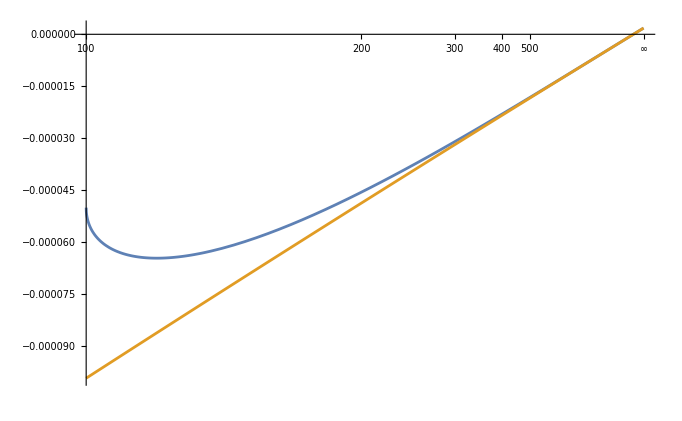

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100
l:=b1^(3/2)/(√(b1-1))
U:=∞
N[Limit[Subscript[θ, (out)],z->U]]
N[Limit[Subscript[Crossingθ, (out)],z->U]]
Plot[{Subscript[θ, (out)],Subscript[Crossingθ, (out)]},{z,b1,∞}]
Clear[b1,l,U,M,σ,ω]
```

#### Crosing

```mathematica
FullSimplify[Solve[Subscript[Crossingθ, (out)]==0,z],Assumptions->{b1>0,l>b1,z>b1}]
```

{{z→(144 π (-3587584000 (14535715541417+l (4122110977999+747721545818 l))-68637212227584000 (24118+l (19251+l (12740+5461 l))) π+21525504000 (408125992097+l (112414125847+18592995338 l)) π^2+22879070742528000 (13878+l (9011+3 l (1516+455 l))) π^3-38745907200 (11353181657+l (3003883039+455976506 l)) π^4-3050542765670400 (6710+l (3635+l (1476+341 l))) π^5+33210777600 (311121233+l (78437095+10983146 l)) π^6+217895911833600 (2870+l (1331+l (452+85 l))) π^7-16605388800 (8334857+l (1990255+258074 l)) π^8-9674805460320 (1110+l (451+3 l (44+7 l))) π^9+5405301720 (215105+l (48439+5834 l)) π^10+288662217480 (382+l (139+l (36+5 l))) π^11-1208186280 (5129+l (1087+122 l)) π^12-6013943820 (102+l (34+l (8+l))) π^13+191509029 (95+l (19+2 l)) π^14))/(60189671686144000 (69425449+10593529 l)+1235469820096512000 (206249+2 l (80093+43690 l)) π-516612096000 (2247985875454+373860772909 l) π^2-823646546731008000 (107945+61882 l+21844 l^2) π^3+1549836288000 (60855311758+9296497669 l) π^4+164729309346201600 (46505+6 l (3487+910 l)) π^5-1859803545600 (1615935646+227988253 l) π^6-15688505652019200 (17833+2 l (3293+682 l)) π^7+1195587993600 (41964334+5491573 l) π^8+871583647334400 (6313+2 l (989+170 l)) π^9-478235197440 (1059646+129037 l) π^10-31678475250240 (2089+6 l (95+14 l)) π^11+130045668480 (25678+2917 l) π^12+804828422160 (633+2 l (77+10 l)) π^13-25202113200 (574+61 l) π^14-14777366544 (153+34 l+4 l^2) π^15+3570752079 (10+l) π^16)}}

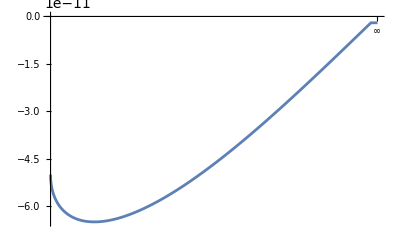

5.6027×10^9

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100000
l:=b1^(3/2)/(√(b1-1))
Plot[{Subscript[θ, (out)]},{z,b1,∞}]
N[(144 π (-3587584000 (14535715541417+l (4122110977999+747721545818 l))-68637212227584000 (24118+l (19251+l (12740+5461 l))) π+21525504000 (408125992097+l (112414125847+18592995338 l)) π^2+22879070742528000 (13878+l (9011+3 l (1516+455 l))) π^3-38745907200 (11353181657+l (3003883039+455976506 l)) π^4-3050542765670400 (6710+l (3635+l (1476+341 l))) π^5+33210777600 (311121233+l (78437095+10983146 l)) π^6+217895911833600 (2870+l (1331+l (452+85 l))) π^7-16605388800 (8334857+l (1990255+258074 l)) π^8-9674805460320 (1110+l (451+3 l (44+7 l))) π^9+5405301720 (215105+l (48439+5834 l)) π^10+288662217480 (382+l (139+l (36+5 l))) π^11-1208186280 (5129+l (1087+122 l)) π^12-6013943820 (102+l (34+l (8+l))) π^13+191509029 (95+l (19+2 l)) π^14))/(60189671686144000 (69425449+10593529 l)+1235469820096512000 (206249+2 l (80093+43690 l)) π-516612096000 (2247985875454+373860772909 l) π^2-823646546731008000 (107945+61882 l+21844 l^2) π^3+1549836288000 (60855311758+9296497669 l) π^4+164729309346201600 (46505+6 l (3487+910 l)) π^5-1859803545600 (1615935646+227988253 l) π^6-15688505652019200 (17833+2 l (3293+682 l)) π^7+1195587993600 (41964334+5491573 l) π^8+871583647334400 (6313+2 l (989+170 l)) π^9-478235197440 (1059646+129037 l) π^10-31678475250240 (2089+6 l (95+14 l)) π^11+130045668480 (25678+2917 l) π^12+804828422160 (633+2 l (77+10 l)) π^13-25202113200 (574+61 l) π^14-14777366544 (153+34 l+4 l^2) π^15+3570752079 (10+l) π^16)]
Clear[b1,b2,b3,l,M,σ,ω]
```

```mathematica
Simplify[Series[(144 π (-3587584000 (14535715541417+l (4122110977999+747721545818 l))-68637212227584000 (24118+l (19251+l (12740+5461 l))) π+21525504000 (408125992097+l (112414125847+18592995338 l)) π^2+22879070742528000 (13878+l (9011+3 l (1516+455 l))) π^3-38745907200 (11353181657+l (3003883039+455976506 l)) π^4-3050542765670400 (6710+l (3635+l (1476+341 l))) π^5+33210777600 (311121233+l (78437095+10983146 l)) π^6+217895911833600 (2870+l (1331+l (452+85 l))) π^7-16605388800 (8334857+l (1990255+258074 l)) π^8-9674805460320 (1110+l (451+3 l (44+7 l))) π^9+5405301720 (215105+l (48439+5834 l)) π^10+288662217480 (382+l (139+l (36+5 l))) π^11-1208186280 (5129+l (1087+122 l)) π^12-6013943820 (102+l (34+l (8+l))) π^13+191509029 (95+l (19+2 l)) π^14)),{l,∞,2}],Assumptions->{M>0,b1>M}]
Simplify[Series[(60189671686144000 (69425449+10593529 l)+1235469820096512000 (206249+2 l (80093+43690 l)) π-516612096000 (2247985875454+373860772909 l) π^2-823646546731008000 (107945+61882 l+21844 l^2) π^3+1549836288000 (60855311758+9296497669 l) π^4+164729309346201600 (46505+6 l (3487+910 l)) π^5-1859803545600 (1615935646+227988253 l) π^6-15688505652019200 (17833+2 l (3293+682 l)) π^7+1195587993600 (41964334+5491573 l) π^8+871583647334400 (6313+2 l (989+170 l)) π^9-478235197440 (1059646+129037 l) π^10-31678475250240 (2089+6 l (95+14 l)) π^11+130045668480 (25678+2917 l) π^12+804828422160 (633+2 l (77+10 l)) π^13-25202113200 (574+61 l) π^14-14777366544 (153+34 l+4 l^2) π^15+3570752079 (10+l) π^16),{l,∞,2}],Assumptions->{M>0,b1>M}]
```

-56687040 (π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12)) l^3+288 π (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9+15767265117240 π^10+5195919914640 π^11-73699363080 π^12-24055775280 π^13+191509029 π^14) l^2+144 π (-14788419390893564416000-1321334972593219584000 π+2419770715576101888000 π^2+206163306460919808000 π^3-116388173468747980800 π^4-11088722953211904000 π^5+2604956917635072000 π^6+290019458650521600 π^7-33048958086144000 π^8-4363337262604320 π^9+261827410015080 π^10+40124048229720 π^11-1313298486360 π^12-204474089880 π^13+3638671551 π^14) l+720 π (-10429620100987793305600-331078456900974182400 π+1757023535077588377600 π^2+63503148752960716800 π^3-87977864581372846080 π^4-4093828391529676800 π^5+2066515615160156160 π^6+125072253392486400 π^7-27680708215480320 π^8-2147806812191040 π^9+232541485296120 π^10+22053793415472 π^11-1239357486024 π^12-122684453928 π^13+3638671551 π^14)+O[1/l]^3

-3779136 (π (-28566146568960000+4760806482432000 π^2-237996734976000 π^4+5662437580800 π^6-78414336000 π^8+704127060 π^10-4259325 π^12+15641 π^14)) l^2+(637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12+123943577012640 π^13-1537328905200 π^14-502430462496 π^15+3570752079 π^16) l+2 (2089347490986567139328000+127407207462542751744000 π-580668347448342945792000 π^2-44454263243439329280000 π^3+47157885240050737152000 π^4+3830368265572552704000 π^5-1502661421946113228800 π^6-139886560646229196800 π^7+25086026944910131200 π^8+2751153782811033600 π^9-253380007013253120 π^10-33088167398875680 π^11+1669656337614720 π^12+254728195613640 π^13-7233006488400 π^14-1130468540616 π^15+17853760395 π^16)+O[1/l]^3

```mathematica
Simplify[Series[(-56687040 (π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12)) l^3+288 π (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9+15767265117240 π^10+5195919914640 π^11-73699363080 π^12-24055775280 π^13+191509029 π^14) l^2)/((637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12+123943577012640 π^13-1537328905200 π^14-502430462496 π^15+3570752079 π^16) l),{l,∞,5}],Assumptions->{M>0,b1>M}]
```

-((56687040 (π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8-3666390 π^10+15277 π^12)) l^2)/(637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12+123943577012640 π^13-1537328905200 π^14-502430462496 π^15+3570752079 π^16))+(288 π (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9+15767265117240 π^10+5195919914640 π^11-73699363080 π^12-24055775280 π^13+191509029 π^14) l)/(637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12+123943577012640 π^13-1537328905200 π^14-502430462496 π^15+3570752079 π^16)+O[1/l]^6

```mathematica
σ:=1
ω:=1
M:=1/2
b1:=100000
l:=b1^(3/2)/(√(b1-1))
N[(210450636 l^2 π^2 (-4403750400+366912000 π^2-12221440 π^4+217600 π^6-2387 π^8))/(10948163332892262400+3398093554292236800 π-3316294600011993600 π^2-875152740467174400 π^3+247390958769292800 π^4+59176967893908480 π^5-7280449197880320 π^6-1774115697530880 π^7+112734525150720 π^8+29601518791680 π^9-1059581647872 π^10-310040022195 π^11+6513448059 π^12) l^2+((82368 l π (-4187240656580800-1364944561344000 π+624724643356800 π^2+162421974489600 π^3-27577459082880 π^4-7028285967360 π^5+569366288640 π^6+153735252480 π^7-6689278080 π^8-1993435191 π^9))/(569304493310397644800+176700864823196313600 π-172447319200623667200 π^2-45507942504293068800 π^3+12864329856003225600 π^4+3077202330483240960 π^5-378583358289776640 π^6-92254016271605760 π^7+5862195307837440 π^8+1539278977167360 π^9-55098245689344 π^10-16122081154140 π^11+338699299068 π^12+110663908047 π^13)) l]
Clear[b1,b2,b3,l,M,σ,ω]
```

5.60105×10^19

zCrossing = A1 l^2+A2 l,  where  
A1 = (210450636 l^2 π^2 (-4403750400+366912000 π^2-12221440 π^4+217600 π^6-2387 π^8))/(10948163332892262400+3398093554292236800 π-3316294600011993600 π^2-875152740467174400 π^3+247390958769292800 π^4+59176967893908480 π^5-7280449197880320 π^6-1774115697530880 π^7+112734525150720 π^8+29601518791680 π^9-1059581647872 π^10-310040022195 π^11+6513448059 π^12)
A2 = ((82368 l π (-4187240656580800-1364944561344000 π+624724643356800 π^2+162421974489600 π^3-27577459082880 π^4-7028285967360 π^5+569366288640 π^6+153735252480 π^7-6689278080 π^8-1993435191 π^9))/(569304493310397644800+176700864823196313600 π-172447319200623667200 π^2-45507942504293068800 π^3+12864329856003225600 π^4+3077202330483240960 π^5-378583358289776640 π^6-92254016271605760 π^7+5862195307837440 π^8+1539278977167360 π^9-55098245689344 π^10-16122081154140 π^11+338699299068 π^12+110663908047 π^13))

```mathematica
N[-((56687040 (π^2 (952161296486400-79332244992000 π^2+2642470871040 π^4-47048601600 π^6+516107592 π^8)) l^2)/(637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12))+(288 π (-1341256927115961856000-437219041889710080000 π+200111797760050176000 π^2+52027006868508672000 π^3-8833611693428121600 π^4-2251300561064755200 π^5+182379409577164800 π^6+49244476074393600 π^7-2142709554585600 π^8-638537160381120 π^9) l)/(637621032507645362176000+197904968601979871232000 π-193140997504698507264000 π^2-50968895604808237056000 π^3+14408049438723612672000 π^4+3446466610141229875200 π^5-424013361284549836800 π^6-103324498224198451200 π^7+6565658744777932800 π^8+1723992454427443200 π^9-61710035172065280 π^10-18056730892636800 π^11+379343214956160 π^12+123943577012640 π^13)]
```

0.918578 l+0.560093 l^2

```mathematica
zCrossing:=0.56 l^2+0.91 l
zfocus:=l^2/2-l/2
```

For large  l   zcrossing and  gravitational focus    zfocus   are the same order of magnitude
Gravitational Focus    rfocus =  (c^2 P^2)/(4 G M)   =P^2/(4 M),   zfocus = rfocus/(2 M),    P=2M b1
zfocus=l^2/2-l/2

```mathematica
Expand[(1/(2 M))P^2/(4 M)/.{P->2M b1}/.{b1->l-1/2}]
```

1/8-l/2+l^2/2

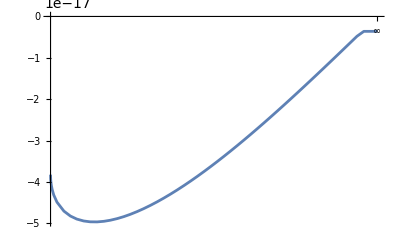

3.1062×10^10

2.77337×10^10

```mathematica
σ=1;
ω=1;
M:=235728/2
b1=235515;
l=b1^(3/2)/(√(b1-1));
Plot[{Subscript[θ, (out)]},{z,b1,∞}]
N[zCrossing]
N[zfocus]
Clear[b1,b2,b3,l,M,σ,ω]
```

```mathematica
3.1062042734065006*^10/(5.0642474847664185*^7)
2.7733657612750004*^10/(5.0642474847664185*^7)
```

613.359

547.636

For the Sun  crossing occurs at    z= 3.04766×10^10,  which is    613.359  AU

### Boundary Behaviour of θ_(in) and θ_(out)

z → b1

```mathematica
Subscript[θatb1, (in)]=FullSimplify[Limit[Subscript[θ, (in)] ,z->b1],Assumptions->{M>0,b1>3M,z>b1}]
Subscript[θatb1, (out)]=FullSimplify[Limit[Subscript[θ, (out)] ,z->b1],Assumptions->{M>0,b1>3M,z>b1}]
Subscript[θatb1, (out)]-Subscript[θatb1, (in)]
```

-1/(431828000692506722304000 b1^20 M ω)l (57401344000 l^2 (1332190789632 b1^14+872889716736 b1^12 l^2+748389860352 b1^10 l^4+716189942016 b1^8 l^6+708020523072 b1^6 l^8+705964897296 b1^4 l^10+705449516292 b1^2 l^12+705320507201 l^14)+2470939640193024000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) π-129153024000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π^2-411823273365504000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^3+96864768000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^4+20591163668275200 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^5-29059430400 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^6-490265801625600 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^7+4670265600 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^8+6809247244800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^9-467026560 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^10-61902247680 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^11+31842720 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^12+396809280 b1^3 l^12 (4 b1^2+l^2) π^13-1574640 l^14 (36 b1^2+25 l^2) π^14-1889568 b1^3 l^14 π^15+59049 l^16 π^16) σ

-1/(431828000692506722304000 b1^20 M ω)l (57401344000 l^2 (1332190789632 b1^14+872889716736 b1^12 l^2+748389860352 b1^10 l^4+716189942016 b1^8 l^6+708020523072 b1^6 l^8+705964897296 b1^4 l^10+705449516292 b1^2 l^12+705320507201 l^14)+2470939640193024000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) π-129153024000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π^2-411823273365504000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^3+96864768000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^4+20591163668275200 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^5-29059430400 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^6-490265801625600 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^7+4670265600 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^8+6809247244800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^9-467026560 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^10-61902247680 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^11+31842720 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^12+396809280 b1^3 l^12 (4 b1^2+l^2) π^13-1574640 l^14 (36 b1^2+25 l^2) π^14-1889568 b1^3 l^14 π^15+59049 l^16 π^16) σ

0

z → ∞

```mathematica
FullSimplify[Limit[Subscript[θ, (in)] ,z->∞],Assumptions->{M>0,b1>3M,z>b1}]
FullSimplify[Limit[Subscript[θ, (out)] ,z->∞],Assumptions->{M>0,b1>3M,z>b1}]
```

0

-1/(6589172373848064000 b1^20 M ω)l (1235469820096512000 b1^17 π-102955818341376000 b1^15 l^2 π (-3+2 π^2)-68637212227584000 b1^14 l^2 (-16+9 π^2)+1906589228544000 b1^12 l^4 (640-225 π^2+27 π^4)-61283225203200 b1^11 l^6 π (-315+210 π^2-42 π^4+4 π^6)+49601160 b1^5 l^12 π (6081075-4054050 π^2+810810 π^4-77220 π^6+4290 π^8-156 π^10+4 π^12)-118098 b1^3 l^14 π (-638512875+425675250 π^2-85135050 π^4+8108100 π^6-450450 π^8+16380 π^10-420 π^12+8 π^14)+5147790917068800 b1^13 l^4 π (15+2 π^2 (-5+π^2))-10592162380800 b1^10 l^6 (-116480+9 π^2 (3605-375 π^2+18 π^4))+1702311811200 b1^9 l^8 π (2835+2 π^2 (-945+189 π^2-18 π^4+π^6))+42032390400 b1^8 l^8 (29388800+9 π^2 (-840875+75705 π^2-3150 π^4+81 π^6))-7737780960 b1^7 l^10 π (-155925+2 π^2 (51975-10395 π^2+990 π^4-55 π^6+2 π^8))+589680 b1^4 l^12 (2095149056000+9 π^2 (-58311378125+4887041775 π^2-166493250 π^4+81 π^6 (39655-550 π^2+6 π^4)))-233513280 b1^6 l^10 (-5290700800+9 π^2 (148092175+3 π^2 (-4204375+151410 π^2-3375 π^4+54 π^6)))+l^16 (1235469791395840000+9 π^2 (-34322788221596875+2861274889097625 π^2-95514037368750 π^4+81 π^6 (21177181025-240490250 π^2+1968330 π^4-13500 π^6+81 π^8)))-180 b1^2 l^14 (-6863719787724800+9 π^2 (190751659273175-15919006228125 π^2+9 π^4 (59296106870+9 π^2 (-120245125+2 π^2 (721721-6825 π^2+54 π^4)))))) σ

#### Scaling of θ_(in)as z->b1

```mathematica
FullSimplify[Series[-1/(431828000692506722304000 b1^20 M ω)l (57401344000 l^2 (1332190789632 b1^14+872889716736 b1^12 l^2+748389860352 b1^10 l^4+716189942016 b1^8 l^6+708020523072 b1^6 l^8+705964897296 b1^4 l^10+705449516292 b1^2 l^12+705320507201 l^14)+2470939640193024000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) π-129153024000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π^2-411823273365504000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^3+96864768000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^4+20591163668275200 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^5-29059430400 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^6-490265801625600 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^7+4670265600 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^8+6809247244800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^9-467026560 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^10-61902247680 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^11+31842720 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^12+396809280 b1^3 l^12 (4 b1^2+l^2) π^13-1574640 l^14 (36 b1^2+25 l^2) π^14-1889568 b1^3 l^14 π^15+59049 l^16 π^16) σ/.{b1->l},{l,Infinity,100}],Assumptions->{M>0,b1>3M}]
```

(π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14) σ)/(228532659683328000 M ω l^2)+1/(431828000692506722304000 M ω l^3)(-372788192693839290368000-9 π^2 (-5365027708463847424000+100055898880025088000 π^2+9 π^4 (-81792700865075200+9 π^2 (35181213267200-82666263680 π^2+127414560 π^4-131760 π^6+81 π^8)))) σ+O[1/l]^101

```mathematica
N[(π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14))/228532659683328000]
N[(1/431828000692506722304000(-372788192693839290368000-9 π^2 (-5365027708463847424000+100055898880025088000 π^2+9 π^4 (-81792700865075200+9 π^2 (35181213267200-82666263680 π^2+127414560 π^4-131760 π^6+81 π^8)))))]
```

-0.25

0.0513689

as z->b1  θ_(in) aproaches
θ_(in)[b1]=1/(228532659683328000 l^2 M ω)π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14) σ
θ_(in)[b1]=𝔹 σ/(l^2 M ω),
where  𝔹=1/228532659683328000 π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14) ≈-0.25

```mathematica
FullSimplify[2(-1/228532659683328000 π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14))]
N[2(-1/228532659683328000 π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14))]
```

-(π (-28566146568960000+1190201620608000 π^2-14874795936000 π^4+88475587200 π^6-306306000 π^8+687960 π^10-1050 π^12+π^14))/114266329841664000

0.5

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=100
l:=b1^(3/2)/(√(b1-1))
N[-1/(431828000692506722304000 b1^20 M ω)l (57401344000 l^2 (1332190789632 b1^14+872889716736 b1^12 l^2+748389860352 b1^10 l^4+716189942016 b1^8 l^6+708020523072 b1^6 l^8+705964897296 b1^4 l^10+705449516292 b1^2 l^12+705320507201 l^14)+2470939640193024000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) π-129153024000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π^2-411823273365504000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^3+96864768000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^4+20591163668275200 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^5-29059430400 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^6-490265801625600 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^7+4670265600 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^8+6809247244800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^9-467026560 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^10-61902247680 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^11+31842720 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^12+396809280 b1^3 l^12 (4 b1^2+l^2) π^13-1574640 l^14 (36 b1^2+25 l^2) π^14-1889568 b1^3 l^14 π^15+59049 l^16 π^16) σ]
N[-σ/(4M ω l^2)]
Clear[M,σ,ω,b1,l]
```

-0.0000500631

-0.0000495

#### Scaling of θ_(out)as z->∞

```mathematica
FullSimplify[Series[-1/(6589172373848064000 b1^20 M ω)l (1235469820096512000 b1^17 π-102955818341376000 b1^15 l^2 π (-3+2 π^2)-68637212227584000 b1^14 l^2 (-16+9 π^2)+1906589228544000 b1^12 l^4 (640-225 π^2+27 π^4)-61283225203200 b1^11 l^6 π (-315+210 π^2-42 π^4+4 π^6)+49601160 b1^5 l^12 π (6081075-4054050 π^2+810810 π^4-77220 π^6+4290 π^8-156 π^10+4 π^12)-118098 b1^3 l^14 π (-638512875+425675250 π^2-85135050 π^4+8108100 π^6-450450 π^8+16380 π^10-420 π^12+8 π^14)+5147790917068800 b1^13 l^4 π (15+2 π^2 (-5+π^2))-10592162380800 b1^10 l^6 (-116480+9 π^2 (3605-375 π^2+18 π^4))+1702311811200 b1^9 l^8 π (2835+2 π^2 (-945+189 π^2-18 π^4+π^6))+42032390400 b1^8 l^8 (29388800+9 π^2 (-840875+75705 π^2-3150 π^4+81 π^6))-7737780960 b1^7 l^10 π (-155925+2 π^2 (51975-10395 π^2+990 π^4-55 π^6+2 π^8))+589680 b1^4 l^12 (2095149056000+9 π^2 (-58311378125+4887041775 π^2-166493250 π^4+81 π^6 (39655-550 π^2+6 π^4)))-233513280 b1^6 l^10 (-5290700800+9 π^2 (148092175+3 π^2 (-4204375+151410 π^2-3375 π^4+54 π^6)))+l^16 (1235469791395840000+9 π^2 (-34322788221596875+2861274889097625 π^2-95514037368750 π^4+81 π^6 (21177181025-240490250 π^2+1968330 π^4-13500 π^6+81 π^8)))-180 b1^2 l^14 (-6863719787724800+9 π^2 (190751659273175-15919006228125 π^2+9 π^4 (59296106870+9 π^2 (-120245125+2 π^2 (721721-6825 π^2+54 π^4)))))) σ/.{b1->l},{l,Infinity,100}],Assumptions->{M>0,b1>3M}]
```

(π (-13948313754375+2324612540250 π^2-116209343250 π^4+2764862100 π^6-38288250 π^8+343980 π^10-2100 π^12+8 π^14) σ)/(55794106368000 M ω l^2)+((-9729324836847616000-9 π^2 (-327455304471670375+24427709687506125 π^2+9 π^4 (-79875684438550+9 π^2 (137426614325-1291660370 π^2+7963410 π^4-32940 π^6+81 π^8)))) σ)/(6589172373848064000 M ω l^3)+O[1/l]^101

```mathematica
N[(1/3689936529354915840(-9729324836847616000-9 π^2 (-327455304471670375+24427709687506125 π^2+9 π^4 (-79875684438550+9 π^2 (137426614325-1291660370 π^2+7963410 π^4-32940 π^6+81 π^8)))))]
N[((π (-13948313754375+2324612540250 π^2-116209343250 π^4+2764862100 π^6-38288250 π^8+343980 π^10-2100 π^12+8 π^14))/55794106368000)]
```

0.892857

1.53443×10^-8

as z->∞  θ_(out) aproaches

θ_(out)[∞]=(π (-13948313754375+2324612540250 π^2-116209343250 π^4+2764862100 π^6-38288250 π^8+343980 π^10-2100 π^12+8 π^14) σ)/(55794106368000 l^2 M ω)+1/(6589172373848064000 l^3 M ω)(-9729324836847616000-9 π^2 (-327455304471670375+24427709687506125 π^2+9 π^4 (-79875684438550+9 π^2 (137426614325-1291660370 π^2+7963410 π^4-32940 π^6+81 π^8)))) σ


θ_(out)[∞]= ℂ_(1)σ/(l^3 M ω) + ℂ_(2)σ/(l^2 M ω),
where 
ℂ_(1)=1/3689936529354915840(-9729324836847616000-9 π^2 (-327455304471670375+24427709687506125 π^2+9 π^4 (-79875684438550+9 π^2 (137426614325-1291660370 π^2+7963410 π^4-32940 π^6+81 π^8))))
≈0.892

ℂ_(2)=(π (-13948313754375+2324612540250 π^2-116209343250 π^4+2764862100 π^6-38288250 π^8+343980 π^10-2100 π^12+8 π^14))/55794106368000 ≈1.53×10^-8

for b1 <10000000 as z->∞
θ_(out)[∞]≈ℂ_(1)σ/(l^3 M ω)

for b1 >10000000 as z->∞
θ_(out)[∞]≈ℂ_(2)σ/(l^2 M ω)

```mathematica
Simplify[2(1/3689936529354915840)]
N[2(1/3689936529354915840(-9729324836847616000-9 π^2 (-327455304471670375+24427709687506125 π^2+9 π^4 (-79875684438550+9 π^2 (137426614325-1291660370 π^2+7963410 π^4-32940 π^6+81 π^8)))))]
```

1/1844968264677457920

1.78571

```mathematica
Clear[M,σ,ω,b1,l,U,z]
M:=1/2
σ:=1
ω:=1
b1:=1000000
l:=b1^(3/2)/(√(b1-1))
N[-1/(6589172373848064000 b1^20 M ω)l (1235469820096512000 b1^17 π-102955818341376000 b1^15 l^2 π (-3+2 π^2)-68637212227584000 b1^14 l^2 (-16+9 π^2)+1906589228544000 b1^12 l^4 (640-225 π^2+27 π^4)-61283225203200 b1^11 l^6 π (-315+210 π^2-42 π^4+4 π^6)+49601160 b1^5 l^12 π (6081075-4054050 π^2+810810 π^4-77220 π^6+4290 π^8-156 π^10+4 π^12)-118098 b1^3 l^14 π (-638512875+425675250 π^2-85135050 π^4+8108100 π^6-450450 π^8+16380 π^10-420 π^12+8 π^14)+5147790917068800 b1^13 l^4 π (15+2 π^2 (-5+π^2))-10592162380800 b1^10 l^6 (-116480+9 π^2 (3605-375 π^2+18 π^4))+1702311811200 b1^9 l^8 π (2835+2 π^2 (-945+189 π^2-18 π^4+π^6))+42032390400 b1^8 l^8 (29388800+9 π^2 (-840875+75705 π^2-3150 π^4+81 π^6))-7737780960 b1^7 l^10 π (-155925+2 π^2 (51975-10395 π^2+990 π^4-55 π^6+2 π^8))+589680 b1^4 l^12 (2095149056000+9 π^2 (-58311378125+4887041775 π^2-166493250 π^4+81 π^6 (39655-550 π^2+6 π^4)))-233513280 b1^6 l^10 (-5290700800+9 π^2 (148092175+3 π^2 (-4204375+151410 π^2-3375 π^4+54 π^6)))+l^16 (1235469791395840000+9 π^2 (-34322788221596875+2861274889097625 π^2-95514037368750 π^4+81 π^6 (21177181025-240490250 π^2+1968330 π^4-13500 π^6+81 π^8)))-180 b1^2 l^14 (-6863719787724800+9 π^2 (190751659273175-15919006228125 π^2+9 π^4 (59296106870+9 π^2 (-120245125+2 π^2 (721721-6825 π^2+54 π^4))))))]
N[(89 σ)/(100M ω l^3)+(15σ)/(M ω l^2)×10^-9]
N[(89 σ)/(100M ω l^3)]
N[(15σ)/(M ω l^2)×10^-9]
Clear[M,σ,ω,b1,l]
```

1.81609×10^-18

1.81×10^-18

1.78×10^-18

3.×10^-20

## Plots of θ_(in) and θ_(out)

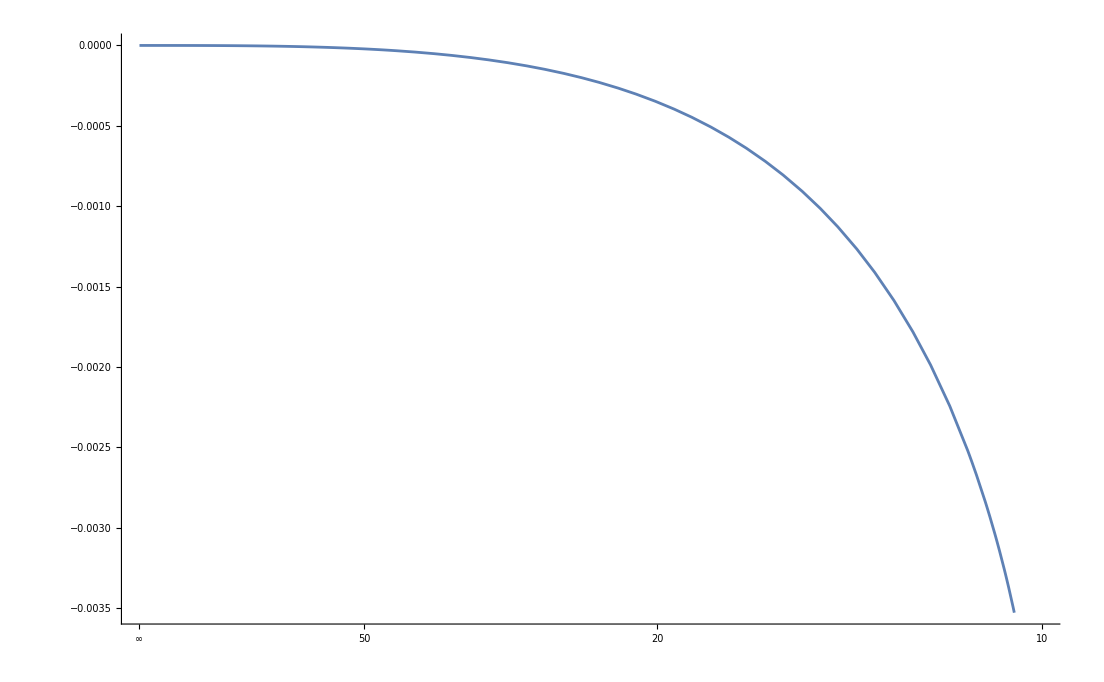

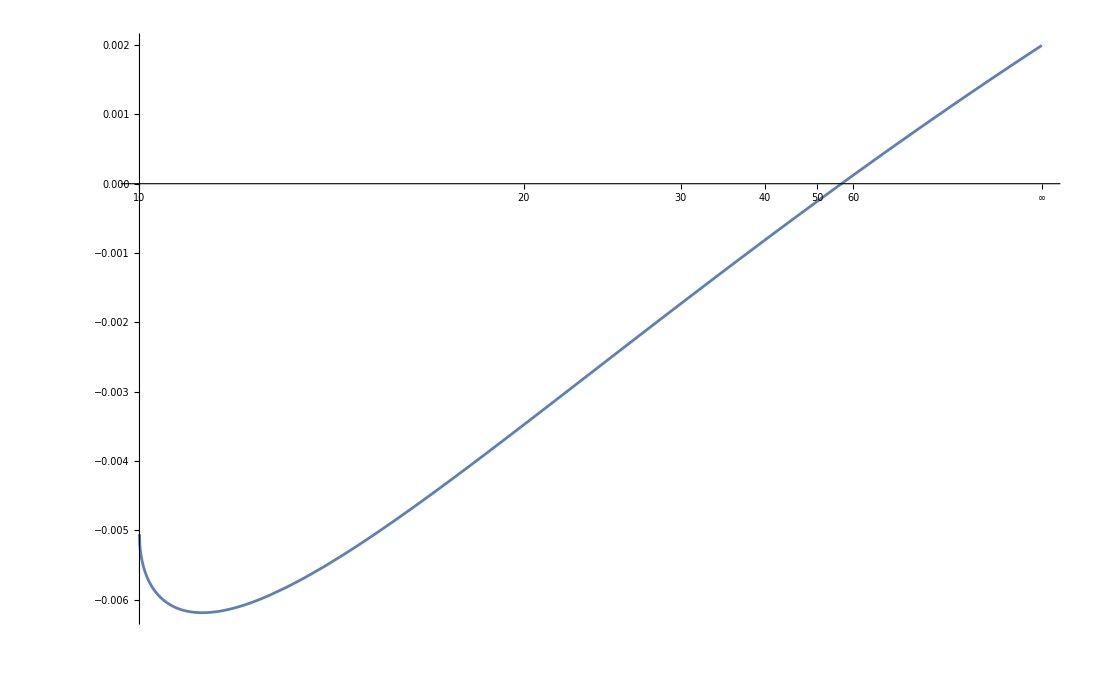

```mathematica
σ=1;
ω=1;
M:=1/2
b1=10;
l=b1^(3/2)/(√(b1-1));
Plot[Subscript[θ, (in)],{z,b1,∞},Axes->{True,False},ScalingFunctions->{"Reverse",Automatic}]
Plot[Subscript[θ, (out)],{z,b1,∞}]
Clear[b1,b2,b3,l,M,σ,ω]
```

## Deviations

c=299792458 m s^-1
G=6.6743×10^-11 m^3 kg^-1 s^-2
Light year =9.46×10^15 m

M from kg to  m   (M → G c^-2 M)
ω from s^-1 to  m^-1   (ω → c^-1 ω )

```mathematica
θatb1:=-1/(431828000692506722304000 b1^20 M ω)l (57401344000 l^2 (1332190789632 b1^14+872889716736 b1^12 l^2+748389860352 b1^10 l^4+716189942016 b1^8 l^6+708020523072 b1^6 l^8+705964897296 b1^4 l^10+705449516292 b1^2 l^12+705320507201 l^14)+2470939640193024000 b1^3 (4 b1^2+l^2) (16 b1^4+l^4) (256 b1^8+l^8) π-129153024000 l^2 (78364164096 b1^14+54419558400 b1^12 l^2+43596112896 b1^10 l^4+40352774400 b1^8 l^6+39482220096 b1^6 l^8+39257946000 b1^4 l^10+39201140196 b1^2 l^12+39186856825 l^14) π^2-411823273365504000 b1^3 l^2 (4096 b1^12+1024 b1^10 l^2+256 b1^8 l^4+64 b1^6 l^6+16 b1^4 l^8+4 b1^2 l^10+l^12) π^3+96864768000 l^4 (2176782336 b1^12+1511654400 b1^10 l^2+1211003136 b1^8 l^4+1120910400 b1^6 l^6+1096728336 b1^4 l^8+1090498500 b1^2 l^10+1088920561 l^12) π^4+20591163668275200 b1^3 l^4 (1024 b1^10+256 b1^8 l^2+64 b1^6 l^4+16 b1^4 l^6+4 b1^2 l^8+l^10) π^5-29059430400 l^6 (60466176 b1^10+41990400 b1^8 l^2+33638976 b1^6 l^4+31136400 b1^4 l^6+30464676 b1^2 l^8+30291625 l^10) π^6-490265801625600 b1^3 l^6 (256 b1^8+64 b1^6 l^2+16 b1^4 l^4+4 b1^2 l^6+l^8) π^7+4670265600 l^8 (1679616 b1^8+1166400 b1^6 l^2+934416 b1^4 l^4+864900 b1^2 l^6+846241 l^8) π^8+6809247244800 b1^3 l^8 (4 b1^2+l^2) (16 b1^4+l^4) π^9-467026560 l^10 (46656 b1^6+32400 b1^4 l^2+25956 b1^2 l^4+24025 l^6) π^10-61902247680 b1^3 l^10 (16 b1^4+4 b1^2 l^2+l^4) π^11+31842720 l^12 (1296 b1^4+900 b1^2 l^2+721 l^4) π^12+396809280 b1^3 l^12 (4 b1^2+l^2) π^13-1574640 l^14 (36 b1^2+25 l^2) π^14-1889568 b1^3 l^14 π^15+59049 l^16 π^16) σ
```

#### Angular Frequency ω

Frequency of visible light  ωred  =2π×400 THz       =8π×10^14 s^-1    ⇒in Geometrized units      Redω  = 8.38338×10^6 m^-1

Frequency of radio waves  ωradio  =2π×50 MHz   =π×10^7 s^-1   ⇒in Geometrized units       Radioω  = 0.104792 m^-1

```mathematica
c=299792458 m s^-1;
ωred= 8π×10^14 s^-1;
ωradio= π×10^7 s^-1;
Redω==N[c^-1 ωred]
Radioω==N[c^-1 ωradio]
Clear[c,ωred,ωradio]
```

Redω==(8.38338×10^6)/m

Radioω==0.104792/m

## Sun

Mass of the sun   M=1.988×10^30 kg   in Geometrized units       M = 1476.32 m
Distance to Earth          z_(S-E) = 149597870700m     =5.06425×10^7 r_g
b1 =235515

```mathematica
M = 1476.32 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.1047922510975841 m^-1;
b1=235515;
l=b1^(3/2)/(√(b1-1));
z=5.0642474847664185*^7;
Subscript[θb1, visible]==N[θatb1/.{ω->Redω}]
Subscript[θb1, Radio]==N[θatb1/.{ω->Radioω}]
Subscript[θ, visible]==N[Subscript[θ, (out)]/.{ω->Redω}]
Subscript[θ, Radio]==N[Subscript[θ, (out)]/.{ω->Radioω}]
Clear[M,Redω,Radioω,b1,l,z]
```

θb1_visible==-3.64169×10^-22 σ

θb1_Radio==-2.91336×10^-14 σ

θ_visible==-3.38162×10^-24 σ

θ_Radio==-2.7053×10^-16 σ

## Proxima Centauri

Mass of Proxima Centauri   M=2.42735×10^29 kg   in Geometrized units       M = 180.35 m
Distance to Earth          z_(PC-E) = 4.017499×10^16 m           =1.11381×10^14
b1= 297422

```mathematica
M = 180.35 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.1047922510975841 m^-1;
b1=297422;
l=b1^(3/2)/(√(b1-1));
z=1.1138062101469366*^14;
Subscript[θ, visible]==N[θatb1/.{ω->Redω}]
Subscript[θ, Radio]==N[θatb1/.{ω->Radioω}]
Subscript[θ, visible]==N[Subscript[θ, (out)]/.{ω->Redω}]
Subscript[θ, Radio]==N[Subscript[θ, (out)]/.{ω->Radioω}]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==-1.86921×10^-21 σ

θ_Radio==-1.49537×10^-13 σ

θ_visible==2.25463×10^-26 σ

θ_Radio==1.8037×10^-18 σ

## RX J1856.5-3754

Mass of RX J1856.5-3754   M=1.7892×10^30 kg   in Geometrized units       M = 1329.3 m
Distance to Earth          z_(RX-E) = 3.784×10^18 m           =1.42331×10^15
b1= 10

```mathematica
M = 1329.3 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.1047922510975841 m^-1;
b1=10;
l=b1^(3/2)/(√(b1-1));
z=1.423305499134883*^15;
Subscript[θ, visible]==N[θatb1/.{ω->Redω}]
Subscript[θ, Radio]==N[θatb1/.{ω->Radioω}]
Subscript[θ, visible]==N[Subscript[θ, (out)]/.{ω->Redω}]
Subscript[θ, Radio]==N[Subscript[θ, (out)]/.{ω->Radioω}]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==-2.26757×10^-13 σ

θ_Radio==-0.0000181405 σ

θ_visible==8.94535×10^-14 σ

θ_Radio==7.15628×10^-6 σ

## Gaia BH1

Mass of Gaia BH1   M=1.91246×10^31 kg   in Geometrized units       M = 14202.2 m
Distance to Earth          D_(GB-E) = 1.47576×10^19 m

```mathematica
c=299792458 m s^-1;
G=6.6743×10^-11 m^3 kg^-1 s^-2;
M=1.9124559999999999*^31 kg;
Mass==N[G c^-2 M]
Clear[c,G,M]
```

Mass==14202.2 m

## Sun to Solar Gravity

Mass of the sun   M=1.988×10^30 kg   in Geometrized units       M = 1476.32 m
Distance to Earth          z_(S-SG) = 542×149597870700m     =542×5.06425×10^7 r_g
b1 =235515

```mathematica
M = 1476.32 m;
Redω  = 8.383380087806727*^6 m^-1;
Radioω  = 0.1047922510975841 m^-1;
b1=235515;
l=b1^(3/2)/(√(b1-1));
z=542×5.0642474847664185*^7;
Subscript[θ, visible]==N[θatb1/.{ω->Redω}]
Subscript[θ, Radio]==N[θatb1/.{ω->Radioω}]
Subscript[θ, visible]==N[Subscript[θ, (out)]/.{ω->Redω}]
Subscript[θ, Radio]==N[Subscript[θ, (out)]/.{ω->Radioω}]
Clear[M,Redω,Radioω,b1,l,z]
```

θ_visible==-3.64169×10^-22 σ

θ_Radio==-1.45668×10^-13 σ

θ_visible==-7.05636×10^-28 σ

θ_Radio==-2.82254×10^-19 σ